## Corrections to the eikonal QNMs

### Computation of δω (compile)

```mathematica
Delta=r^2-2M r+a^2;
Sigma=r^2+(a x)^2;
(*Correction to the potential, expressed in terms of eliptic functions*)
dV=-1/(r^6 (q r^2-a^2 x0^2)^2 (r^2+a^2 x0^2)^3)24 M^2 (44 a^4 r^4 x0^4+44 a^6 r^2 x0^6+15 a^8 x0^8+3 q^2 (19 r^8+22 a^2 r^6 x0^2+8 a^4 r^4 x0^4)-2 q (48 a^2 r^6 x0^2+50 a^4 r^4 x0^4+17 a^6 r^2 x0^6)) σ^2+1/EllipticK[-q](-1/(r^6 (q r^2-a^2 x0^2)^3 (r^2+a^2 x0^2)^3)24 a^2 M^2 x0^2 (44 a^4 r^4 x0^4+44 a^6 r^2 x0^6+15 a^8 x0^8+q^2 (87 r^8+116 a^2 r^6 x0^2+44 a^4 r^4 x0^4)-2 q (58 a^2 r^6 x0^2+65 a^4 r^4 x0^4+22 a^6 r^2 x0^6)) σ^2 EllipticE[-q]+1/(r^8 (q r^2-a^2 x0^2)^3 (r^2+a^2 x0^2)^3)72 M^2 (-a^6 x0^6 (16 r^6+24 a^2 r^4 x0^2+18 a^4 r^2 x0^4+5 a^6 x0^6)+q^3 r^6 (35 r^6+70 a^2 r^4 x0^2+56 a^4 r^2 x0^4+16 a^6 x0^6)+a^4 q r^2 x0^4 (56 r^6+88 a^2 r^4 x0^2+65 a^4 r^2 x0^4+18 a^6 x0^6)-a^2 q^2 r^4 x0^2 (70 r^6+119 a^2 r^4 x0^2+88 a^4 r^2 x0^4+24 a^6 x0^6)) σ^2 EllipticPi[-(a^2 x0^2)/r^2,-q]);
subs={σ->BLk+a w (-2 k+a w),q->(2 x0^2 αh)/(2+αh (-3+2 x0^2+μh)),μh->-((-1+x0^2) (2+(-1+2 x0^2) αh))/(2+(-1+x0^2) αh)};(*Here μh=k^2/L^2, αh=a^2w^2/L^2, L=l+1/2*)
x0sol=FullSimplify[Solve[μ^2==1+2 x0^2 (-1+1/(2+a^2 (-1+x0^2) Ω^2)),x0]];
qsol=q/.subs/.{αh-> a^2Ω^2,μh-> μ^2};
dVev=Simplify[dV/.{σ->BLk+a w (-2 k+a w)}/.{q-> qsol}/.x0sol[[4]]/.{BLk-> L^2(1-a^2Ω^2/2(1-μ^2)) }/.{ Ω-> w/L,k-> μ L}];

Clear[R];
Eqtot=(-4 a k M r w+r (2 BLk M-BLk r+r^3 w^2)+a^2 (-BLk+k^2+r (2 M+r) w^2)) R[r]+(a^2+r (-2 M+r)) (-2 (M-r) R'[r]+(a^2+r (-2 M+r)) R''[r])+ϵ(a^2+r (-2 M+r)) deltaV R[r] ;
R[r_]:=u[r]/√(a^2+r^2);
upsol=Simplify[Solve[{up==Delta/(r^2+a^2)D[u[r],r],upp==Delta/(r^2+a^2)D[Delta/(r^2+a^2)D[u[r],r],r]},{u'[r],u''[r]}]];
Equ=Collect[Simplify[Eqtot/.upsol[[1]]]/(a^2+r^2)^(3/2),{upp,ϵ},Simplify];
Equeikonal=Collect[Normal[Series[Equ/.{upp-> upp e^2, BLk-> BLk e^2, w-> w e, k-> k e, deltaV-> e^4 deltaV[r,ω]},{e,Infinity,-2}]],{upp,ϵ},Simplify]/.{e->1};
V0=Coefficient[Equeikonal,u[r]]/.ϵ->0;
Simplify[(-4 a k M r w+r (2 BLk M-BLk r+r^3 w^2)+a^2 (-BLk+k^2+r (2 M+r) w^2))/((a^2+r^2)^2)/.{k->0}];
Vtot=Coefficient[Equeikonal,u[r]];
Eqs0=Simplify[{V0,D[V0,r]}/.{BLk-> L^2(1-a^2Ω^2/2(1-μ^2)),w-> Ω L, k-> μ L }];
Ωsol2={Ω0->(M-r0)μ a/((r0-3M)r0^2+(r0+M)a^2)};(*Result according to 1207.4253*)
(*The equation for a is the same in both cases, indicating that both solutions for Omega must be equivalent*)
aeq=2 r0^4 (-3 M+r0)^2+a^4 (-1+μ^2) (-2 (M+r0)^2+(M-r0)^2 μ^2)+4 a^2 r0^2 (-2 M r0+3 M^2 (-1+μ^2)-r0^2 (-1+μ^2));
asol=FullSimplify[Solve[aeq==0,a]];
Eqs=Simplify[{(a^2+r^2)^2/(-a^2+(2 M-r) r)Vtot,D[(a^2+r^2)^2/(-a^2+(2 M-r) r)Vtot,r]}/.{BLk-> L^2(1-a^2Ω^2/2(1-μ^2)),w-> Ω L, k-> μ L }];
Simplify[Series[Eqs/.{Ω->Ω0+ϵ dΩ,r->r0+ϵ dr}/.Ωsol2,{ϵ,0,1}]];
dsol=Simplify[Solve[Coefficient[Normal[Simplify[Series[Eqs/.{Ω->Ω0+ϵ dΩ,r->r0+ϵ dr}/.Ωsol2,{ϵ,0,1}]]],ϵ,1]==0,{dΩ,dr}]];
dΩ1=FullSimplify[dΩ/.dsol[[1]]];
dΩ2=Simplify[dΩ1/.{deltaV[r0,ω]-> dVev}/.{σ->BLk+a w (-2 k+a w)}/.{BLk-> L^2(1-a^2Ω^2/2(1-μ^2)),w-> Ω L, k-> μ L ,αh->Ω^2a^2, μh-> μ^2 }/.{r-> r0}];
dV2=Simplify[Series[D[Vtot,{r,2}]/.{BLk-> L^2(1-a^2Ω^2/2(1-μ^2)),w-> Ω L, k-> μ L }/.{Ω->Ω0+ϵ dΩ,r->r0+ϵ dr},{ϵ,0,1}]/.dsol[[1]]/.Ωsol2];
dVsq=Assuming[{a^2+r^2>0,r^2 (-3 M+r)+a^2 (M+r)>0,r>0,L>0},Normal[Simplify[Series[Sqrt[2dV2],{ϵ,0,1}]]]];
dVdw=Simplify[Normal[Series[D[Vtot/.{BLk-> L^2-a^2w^2/2(1-μ^2)},w]+D[Vtot,ω]/.{BLk-> L^2(1-a^2Ω^2/2(1-μ^2)),w-> Ω L, k-> μ L }/.{Ω->Ω0+ϵ dΩ,r->r0+ϵ dr},{ϵ,0,1}]]/.dsol[[1]]/.Ωsol2];
ImW=Normal[Simplify[Series[((-a^2+(2 M-r) r)/(a^2+r^2))dVsq/dVdw/.{r->r0+ϵ dr}/.dsol[[1]],{ϵ,0,1}]]];
ImW0=Coefficient[ImW,ϵ,0];
ImW1=Coefficient[ImW,ϵ,1];
ImW1simp=ImW1/.{deltaV[r0,ω]-> dVev, Derivative[1,0][deltaV][r0,ω]-> D[dVev,r], Derivative[2,0][deltaV][r0,ω]-> D[dVev,{r,2}], Derivative[0,1][deltaV][r0,ω]-> D[dVev,w]}/.{w-> L Ω0}/.Ωsol2;
```

### Plots as a function of χ

List of values of μ for which we want to plot the corrections to the QNMs

```mathematica
μlist=Flatten[{541/727,Table[0.75+10i/1000,{i,0,9,1}]}];
lmu=Length[μlist];
```

Table for the relative corrections to Im(ω)

```mathematica
ind=0;
Monitor[tabImωχ=ParallelTable[
μev=μlist[[ii]];
rev=If[μev>Sqrt[15/2-Sqrt[193]/2],1,Max[r0/.NSolve[{(a/.asol[[2]]/.{M->1}/.{μ->μev})==1,r0>=1,r0<3},r0]]];
ind=ind+1;
Table[Evaluate[{a,ImW1simp/(ImW0)/L^2}/.{Ω->Ω0}/.Ωsol2/.asol[[2]]/.{M->1,μ->μev}/.{L->1,n->0}/.{r->r0}/.{r0->rev(1+1.999Exp[x])}],{x,-7,0,0.02}],{ii,Length[μlist]}];,ii]
```

Table for the relative corrections to Re(ω)

```mathematica
ind=0;
Monitor[tabReωχ=ParallelTable[
μev=μlist[[ii]];
rev=If[μev>Sqrt[15/2-Sqrt[193]/2],1,Max[r0/.NSolve[{(a/.asol[[2]]/.{M->1}/.{μ->μev})==1,r0>=1,r0<3},r0]]];
ind=ind+1;
Table[Evaluate[{a,dΩ2/Ω0/L^2}/.{Ω->Ω0}/.Ωsol2/.asol[[2]]/.{M->1,μ->μev}/.{L->1,n->0}/.{r->r0}/.{r0->rev(1+1.999Exp[x])}],{x,-7,0,0.02}],{ii,Length[μlist]}];,ii]
```

```mathematica
(*Color for the plots*)
colist=Flatten[{{{Black,Dashed}},Table[{ColorData["SunsetColors"][0.9(i-1)/(lmu-1)]},{i,lmu}]},1]
(*Log scale in 1-χ*)
scalinglog={-Log10[1-#1]&,InverseFunction[-Log10[1-#1]&]};
```

{{GrayLevel[0],Dashing[{Small,Small}]},{RGBColor[0., 0., 0.]},{RGBColor[0.20130822000000004, 0.07333200000000002, 0.27351162000000007]},{RGBColor[0.40603252000000006, 0.14572128000000004, 0.487645]},{RGBColor[0.63039928, 0.21268992000000003, 0.3603535]},{RGBColor[0.8188614000000001, 0.29048016000000004, 0.23563478399999993]},{RGBColor[0.92205, 0.39397170000000004, 0.11702642999999999]},{RGBColor[0.9843265200000001, 0.5069600400000001, 0.07000604400000002]},{RGBColor[0.99546294, 0.63181938, 0.11247061800000001]},{RGBColor[1., 0.7465433600000001, 0.2453943600000002]},{RGBColor[1., 0.85429928, 0.44050878000000004]},{RGBColor[1., 0.9293416, 0.6946564000000001]}}

Plot of the relative corrections to Im(ω)

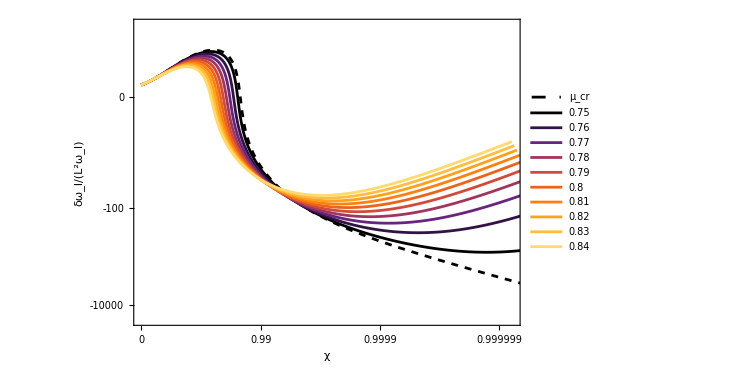

```mathematica
Show[ListPlot[tabImωχ,AspectRatio->0.7,PlotRange->{{0,0.9999994},{-2 10^4,15}},PlotStyle->colist,Frame->True,Joined->True,FrameLabel->{Style["χ",25],Style["δω_I/(L^2ω_I)",25]} ,AspectRatio->0.67,ImageSize->550,FrameStyle->BlackFrame,ScalingFunctions->{scalinglog,{ArcSinh[#1]&,InverseFunction[ArcSinh[#1]&]}},FrameTicks->{{{-10^6,-10^5,-10^4,-10^3,-10^2,-10,0,10,10^2,10^3,10^4,10^5},None},{{0,0.9,0.99,0.999,0.9999,0.99999,0.999999,0.9999999`7,1},None}},PlotLegends->Placed[LineLegend[Table[If[ii==1,"μ_cr",ToString[μlist[[ii]]]],{ii,Length[μlist]}],LegendLayout->{"Column",3}],{0.65,0.78}]]]
```

Plot of the relative corrections to Re(ω)

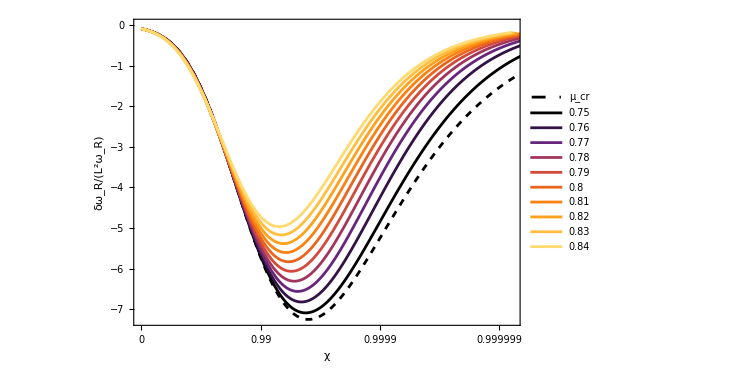

```mathematica
Show[ListPlot[tabReωχ,AspectRatio->0.7,PlotRange->{{0,0.9999994},All},PlotStyle->colist,Frame->True,Joined->True,FrameLabel->{Style["χ",25],Style["δω_R/(L^2ω_R)",25]} ,AspectRatio->0.67,ImageSize->550,FrameStyle->BlackFrame,ScalingFunctions->{scalinglog,Automatic},FrameTicks->{{Automatic,None},{{0,0.9,0.99,0.999,0.9999,0.99999,0.999999,0.9999999`7,1},None}},PlotLegends->Placed[LineLegend[Table[If[ii==1,"μ_cr",ToString[μlist[[ii]]]],{ii,Length[μlist]}],LegendLayout->{"Column",3}],{0.45,0.85}]]]
```

## Phase boundary for low l

### δB_lm values

each element is {l,m,B_lm,δA_lm,7/4 m^2-4-B_lm-α δA_lm,δA_lm/(7/4 m^2-4-B_lm)} where B_lm=A_lm+s where s=-2,2

```mathematica
deltaBTablepos={{{2,0,2.`4.,-80487.6733358141418500344`4.,-6.`4.+80487.6733358141418500344`4. α,13414.6122226356903083391`4.},{2,1,1.1828319135071646099`4.,-12305.2034143747871332688`4.,-3.4328319135071646099`4.+12305.2034143747871332688`4. α,3584.5633355823511500324`4.},{2,2,-1.4563096243079103367`4.,-16678.0793093029291497787`4.,4.4563096243079103367`4.+16678.0793093029291497787`4. α,-3742.5764175650446646535`4.}},{{3,0,8.`4.,-83748.1770174824113621519`4.,-12.`4.+83748.1770174824113621519`4. α,6979.0147514568676135126`4.},{3,1,7.5801358631868177604`4.,-129125.4813928719406298487`4.,-9.8301358631868177604`4.+129125.4813928719406298487`4. α,13135.6761686720914273484`4.},{3,2,6.2511909158047545207`4.,-46103.6114322308658592024`4.,-3.2511909158047545207`4.+46103.6114322308658592024`4. α,14180.5303429309748670335`4.},{3,3,3.6957223523005573435`4.,-45963.3532023513807315494`4.,8.0542776476994426565`4.+45963.3532023513807315494`4. α,-5706.7008629234396096592`4.}},{{4,0,16.`4.,-246793.9367809283034887371`4.,-20.`4.+246793.9367809283034887371`4. α,12339.6968390464151744369`4.},{4,1,15.7115039076871888419`4.,-205157.0330144991794135642`4.,-17.9615039076871888419`4.+205157.0330144991794135642`4. α,11422.04094205584832642`4.},{4,2,14.8569320520415308453`4.,-221297.043058383800276087`4.,-11.8569320520415308453`4.+221297.043058383800276087`4. α,18663.9378624321959773102`4.},{4,3,13.3927803182923684303`4.,-110654.4467135504431355263`4.,-1.6427803182923684303`4.+110654.4467135504431355263`4. α,67358.0304569104787034472`4.},{4,4,11.0423713498405916194`4.,-96083.2703909169866543153`4.,12.9576286501594083806`4.+96083.2703909169866543153`4. α,-7415.1893826448671472378`4.}},{{5,0,26.`4.,-450508.81652307301624615`4.,-30.`4.+450508.81652307301624615`4. α,15016.9605507691005415383`4.},{5,1,25.7702572544527775418`4.,-455841.6696315896685847205`4.,-28.0202572544527775418`4.+455841.6696315896685847205`4. α,16268.289955087781802206`4.},{5,2,25.1055251116839048033`4.,-394267.0628510638260784795`4.,-22.1055251116839048033`4.+394267.0628510638260784795`4. α,17835.6795805168837069553`4.},{5,3,24.0537729767720693068`4.,-365660.895009789261363096`4.,-12.3037729767720693068`4.+365660.895009789261363096`4. α,29719.4117365550955324171`4.},{5,4,22.5992854725607048905`4.,-216330.9538894199851536354`4.,1.4007145274392951095`4.+216330.9538894199851536354`4. α,-154443.2856600007298061318`4.},{5,5,20.5112044279178669379`4.,-175041.5041725793232845076`4.,19.2387955720821330621`4.+175041.5041725793232845076`4. α,-9098.3608364021576521146`4.}},{{6,0,38.`4.,-843796.2704743494946165043`4.,-42.`4.+843796.2704743494946165043`4. α,20090.3873922464165384882`4.},{6,1,37.8018604146861196239`4.,-815891.4394504293951963913`4.,-40.0518604146861196239`4.+815891.4394504293951963913`4. α,20370.8749357185987057493`4.},{6,2,37.2311401434189985849`4.,-771133.7043004279258615569`4.,-34.2311401434189985849`4.+771133.7043004279258615569`4. α,22527.2573764587224400021`4.},{6,3,36.3494315712829963799`4.,-666895.5110469589467535704`4.,-24.5994315712829963799`4.+666895.5110469589467535704`4. α,27110.2000513492620605757`4.},{6,4,35.2242377177092534855`4.,-576617.4308809957971083609`4.,-11.2242377177092534855`4.+576617.4308809957971083609`4. α,51372.5248326865647770953`4.},{6,5,33.8583727909192719624`4.,-375113.1832237777334691774`4.,5.8916272090807280376`4.+375113.1832237777334691774`4. α,-63668.8591982904381018741`4.},{6,6,32.0630233967253405219`4.,-292562.7329395286381032248`4.,26.9369766032746594781`4.+292562.7329395286381032248`4. α,-10861.0085403557329275557`4.}},{{7,0,52.`4.,-1.4271336292045153238214518`4.*^6,-56.`4.+1.4271336292045153238214518`4.*^6 α,25484.5290929377736396688`4.},{7,1,51.8209138290069236548`4.,-1.4056694834169161625888883`4.*^6,-54.0709138290069236548`4.+1.4056694834169161625888883`4.*^6 α,25996.7768967653296784658`4.},{7,2,51.3040783696044953125`4.,-1.326115886887393960728624`4.*^6,-48.3040783696044953125`4.+1.326115886887393960728624`4.*^6 α,27453.4973370252079527421`4.},{7,3,50.506591938865833134`4.,-1.2116265044922366357466897`4.*^6,-38.756591938865833134`4.+1.2116265044922366357466897`4.*^6 α,31262.4625612964431602193`4.},{7,4,49.5089618075149656902`4.,-1.0410603128013312451766658`4.*^6,-25.5089618075149656902`4.+1.0410603128013312451766658`4.*^6 α,40811.5516678782997208834`4.},{7,5,48.38797771299149748`4.,-870532.112318410281713309`4.,-8.63797771299149748`4.+870532.112318410281713309`4. α,100779.620096626563552893`4.},{7,6,47.1601497106623421105`4.,-600670.0477506179933107192`4.,11.8398502893376578895`4.+600670.0477506179933107192`4. α,-50732.9090378405904112557`4.},{7,7,45.6741725673731153337`4.,-460097.8879866756147301613`4.,36.0758274326268846663`4.+460097.8879866756147301613`4. α,-12753.6336857672259344527`4.}},{{8,0,68.`4.,-2.2960525545616854202213702`4.*^6,-72.`4.+2.2960525545616854202213702`4.*^6 α,31889.618813356741947519`4.},{8,1,67.8333255962741002649`4.,-2.2617176032003353156211426`4.*^6,-70.0833255962741002649`4.+2.2617176032003353156211426`4.*^6 α,32271.8361886722016731328`4.},{8,2,67.3504748350231815083`4.,-2.1663359626553568027651852`4.*^6,-64.3504748350231815083`4.+2.1663359626553568027651852`4.*^6 α,33664.6461150324533653131`4.},{8,3,66.6008803548457504692`4.,-2.0062418812948443016483578`4.*^6,-54.8508803548457504692`4.+2.0062418812948443016483578`4.*^6 α,36576.2931846472125362615`4.},{8,4,65.6598711692400469351`4.,-1.7986853687543338851527724`4.*^6,-41.6598711692400469351`4.+1.7986853687543338851527724`4.*^6 α,43175.4904245217624235907`4.},{8,5,64.6168945215121354287`4.,-1.5367612598257501208097981`4.*^6,-24.8668945215121354287`4.+1.5367612598257501208097981`4.*^6 α,61799.4843906347551027867`4.},{8,6,63.5534541984846422721`4.,-1.2654382724904715214279588`4.*^6,-4.5534541984846422721`4.+1.2654382724904715214279588`4.*^6 α,277907.324270792167602035`4.},{8,7,62.4970154540059942074`4.,-908389.7758749067160292053`4.,19.2529845459940057926`4.+908389.7758749067160292053`4. α,-47181.7641418050475648939`4.},{8,8,61.3293390681161381906`4.,-690828.9807663272201623877`4.,46.6706609318838618094`4.+690828.9807663272201623877`4. α,-14802.211217334091003548`4.}},{{9,0,86.`4.,-3.5150399254456288949721158`4.*^6,-90.`4.+3.5150399254456288949721158`4.*^6 α,39055.9991716180988330235`4.},{9,1,85.8418780958611619889`4.,-3.4744671309817743064046967`4.*^6,-88.0918780958611619889`4.+3.4744671309817743064046967`4.*^6 α,39441.4014785889310952883`4.},{9,2,85.3819393373097287579`4.,-3.351673422900909214983665`4.*^6,-82.3819393373097287579`4.+3.351673422900909214983665`4.*^6 α,40684.5656931868209169357`4.},{9,3,84.6623143507350942925`4.,-3.1532720566153869941949264`4.*^6,-72.9123143507350942925`4.+3.1532720566153869941949264`4.*^6 α,43247.4553125139695504414`4.},{9,4,83.7494150987079053859`4.,-2.8826147005683767009532397`4.*^6,-59.7494150987079053859`4.+2.8826147005683767009532397`4.*^6 α,48245.0697769376807802147`4.},{9,5,82.7280456216879568006`4.,-2.5557488452298892112942437`4.*^6,-42.9780456216879568006`4.+2.5557488452298892112942437`4.*^6 α,59466.3812246544990451725`4.},{9,6,81.6917013322663417025`4.,-2.1758314850608814101939942`4.*^6,-22.6917013322663417025`4.+2.1758314850608814101939942`4.*^6 α,95886.66152444768981402`4.},{9,7,80.7245146146615612909`4.,-1.7810163183006396304283485`4.*^6,1.0254853853384387091`4.+1.7810163183006396304283485`4.*^6 α,-1.7367544616082994614516251`4.*^6},{9,8,79.863086083661187574`4.,-1.3153923377889616433996988`4.*^6,28.136913916338812426`4.+1.3153923377889616433996988`4.*^6 α,-46749.7018933951755523423`4.},{9,9,79.0181047080872829867`4.,-999671.3652968661025191768`4.,58.7318952919127170133`4.+999671.3652968661025191768`4. α,-17020.9280720167592571251`4.}},{{10,0,106.`4.,-5.1756979141975207918149039`4.*^6,-110.`4.+5.1756979141975207918149039`4.*^6 α,47051.7992199774617437718`4.},{10,1,105.8480287997618462143`4.,-5.1251118268040528286475654`4.*^6,-108.0980287997618462143`4.+5.1251118268040528286475654`4.*^6 α,47411.7047619590275601934`4.},{10,2,105.4043156278228104351`4.,-4.9754205912009714033243497`4.*^6,-102.4043156278228104351`4.+4.9754205912009714033243497`4.*^6 α,48586.0440616935396969107`4.},{10,3,104.7047768753506615865`4.,-4.7296734909692348358262734`4.*^6,-92.9547768753506615865`4.+4.7296734909692348358262734`4.*^6 α,50881.4463328933967400332`4.},{10,4,103.807037611918215451`4.,-4.396053097316664120880208`4.*^6,-79.807037611918215451`4.+4.396053097316664120880208`4.*^6 α,55083.5268274657369358229`4.},{10,5,102.7871359328926416799`4.,-3.9831636054172655488779489`4.*^6,-63.0371359328926416799`4.+3.9831636054172655488779489`4.*^6 α,63187.5726342899941873109`4.},{10,6,101.7346155597337442222`4.,-3.5081918484249103655576598`4.*^6,-42.7346155597337442222`4.+3.5081918484249103655576598`4.*^6 α,82092.5098418451285727618`4.},{10,7,100.744608023558128883`4.,-2.9818671889009156827913791`4.*^6,-18.994608023558128883`4.+2.9818671889009156827913791`4.*^6 α,156984.928838891778999858`4.},{10,8,99.9028582770791457957`4.,-2.4386094936478041937417048`4.*^6,8.0971417229208542043`4.+2.4386094936478041937417048`4.*^6 α,-301169.1751355604212341526`4.},{10,9,99.2537377596357804489`4.,-1.8405342907946914918923274`4.*^6,38.4962622403642195511`4.+1.8405342907946914918923274`4.*^6 α,-47810.7271636582110498381`4.},{10,10,98.7331092438751446061`4.,-1.4032743572937855619395395`4.*^6,72.2668907561248553939`4.+1.4032743572937855619395395`4.*^6 α,-19417.9428865888141134981`4.}},{{11,0,128.`4.,-7.372376640110153223539561`4.*^6,-132.`4.+7.372376640110153223539561`4.*^6 α,55851.3381826526759359058`4.},{11,1,127.8526038980660915513`4.,-7.311861344736872799500316`4.*^6,-130.1026038980660915513`4.+7.311861344736872799500316`4.*^6 α,56200.7302364650048831985`4.},{11,2,127.4208243642036875837`4.,-7.1313486157557718323737367`4.*^6,-124.4208243642036875837`4.+7.1313486157557718323737367`4.*^6 α,57316.3588346026593260723`4.},{11,3,126.7354546799777177563`4.,-6.8351117065171966883079717`4.*^6,-114.9854546799777177563`4.+6.8351117065171966883079717`4.*^6 α,59443.2724168493170826226`4.},{11,4,125.8464141010385873358`4.,-6.4297550843494525761065392`4.*^6,-101.8464141010385873358`4.+6.4297550843494525761065392`4.*^6 α,63131.8750012219095914535`4.},{11,5,124.8207394425412137613`4.,-5.9261840130930514538694079`4.*^6,-85.0707394425412137613`4.+5.9261840130930514538694079`4.*^6 α,69661.8373359236647325576`4.},{11,6,123.739795978000200141`4.,-5.3375070186748348360757396`4.*^6,-64.739795978000200141`4.+5.3375070186748348360757396`4.*^6 α,82445.5335090740797599117`4.},{11,7,122.6952980275937110278`4.,-4.6832493873081923239655613`4.*^6,-40.9452980275937110278`4.+4.6832493873081923239655613`4.*^6 α,114378.1975686701167095571`4.},{11,8,121.7827975491463260142`4.,-3.9801960027792223570381869`4.*^6,-13.7827975491463260142`4.+3.9801960027792223570381869`4.*^6 α,288779.9801590894233026244`4.},{11,9,121.0891122721361147237`4.,-3.2612414813562308821530985`4.*^6,16.6608877278638852763`4.+3.2612414813562308821530985`4.*^6 α,-195742.3598685013778145032`4.},{11,10,120.6652822781730803082`4.,-2.5044102311717693462505601`4.*^6,50.3347177218269196918`4.+2.5044102311717693462505601`4.*^6 α,-49755.1261737933260128215`4.},{11,11,120.4689952731334890548`4.,-1.9200210067190093773553827`4.*^6,87.2810047268665109452`4.+1.9200210067190093773553827`4.*^6 α,-21998.1542688176196592088`4.}},{{12,0,152.`4.,-1.02115669053633098978712725`4.*^7,-156.`4.+1.02115669053633098978712725`4.*^7 α,65458.7622138673711402005`4.},{12,1,151.8561012403862099923`4.,-1.01398637496527942751591711`4.*^7,-154.1061012403862099923`4.+1.01398637496527942751591711`4.*^7 α,65797.9383557038877294226`4.},{12,2,151.4333667564512466446`4.,-9.9261336328079724395191208`4.*^6,-148.4333667564512466446`4.+9.9261336328079724395191208`4.*^6 α,66872.6570697188638348026`4.},{12,3,150.7583946217865531822`4.,-9.5742867741628809172287456`4.*^6,-139.0083946217865531822`4.+9.5742867741628809172287456`4.*^6 α,68875.6013635907350099543`4.},{12,4,149.8745876897638692127`4.,-9.091397890148031640532884`4.*^6,-125.8745876897638692127`4.+9.091397890148031640532884`4.*^6 α,72225.840473496500595426`4.},{12,5,148.8408478943752446246`4.,-8.4875825505006704785447601`4.*^6,-109.0908478943752446246`4.+8.4875825505006704785447601`4.*^6 α,77802.8836912018599023928`4.},{12,6,147.7298421207360185743`4.,-7.7770238917862179093508944`4.*^6,-88.7298421207360185743`4.+7.7770238917862179093508944`4.*^6 α,87648.3458767333947644138`4.},{12,7,146.6257467688139479995`4.,-6.9769911603140366292125252`4.*^6,-64.8757467688139479995`4.+6.9769911603140366292125252`4.*^6 α,107543.9052004547629983288`4.},{12,8,145.6210300946774685972`4.,-6.1099696822602042813599009`4.*^6,-37.6210300946774685972`4.+6.1099696822602042813599009`4.*^6 α,162408.3568919774969426356`4.},{12,9,144.8110402628229198804`4.,-5.1978635851910786521087292`4.*^6,-7.0610402628229198804`4.+5.1978635851910786521087292`4.*^6 α,736132.8347833318596857031`4.},{12,10,144.2833492134596083712`4.,-4.273630368163383891191437`4.*^6,26.7166507865403916288`4.+4.273630368163383891191437`4.*^6 α,-159961.3066139413115642946`4.},{12,11,144.0947381828961073924`4.,-3.3293527156884383536712132`4.*^6,63.6552618171038926076`4.+3.3293527156884383536712132`4.*^6 α,-52302.8673616083647503109`4.},{12,12,144.2217667652631422653`4.,-2.5700274990541404210999567`4.*^6,103.7782332347368577347`4.+2.5700274990541404210999567`4.*^6 α,-24764.6102554181436748797`4.}},{{13,0,178.`4.,-1.38085194810945797284051677`4.*^7,-182.`4.+1.38085194810945797284051677`4.*^7 α,75870.9861598603281780504`4.},{13,1,177.8588358277077213744`4.,-1.37248104849838271950224065`4.*^7,-180.1088358277077213744`4.+1.37248104849838271950224065`4.*^7 α,76202.8715687940683566676`4.},{13,2,177.4431272709237272758`4.,-1.34749688973576871359265871`4.*^7,-174.4431272709237272758`4.+1.34749688973576871359265871`4.*^7 α,77245.6278912611656626976`4.},{13,3,176.776027922778207984`4.,-1.30630313922082709212612726`4.*^7,-165.026027922778207984`4.+1.30630313922082709212612726`4.*^7 α,79157.4005424219944412289`4.},{13,4,175.8954881074107059049`4.,-1.24959088816649682325636152`4.*^7,-151.8954881074107059049`4.+1.24959088816649682325636152`4.*^7 α,82266.4915025564571605829`4.},{13,5,174.8533626725893214656`4.,-1.17838439317930424719952855`4.*^7,-135.1033626725893214656`4.+1.17838439317930424719952855`4.*^7 α,87220.9521560918775932824`4.},{13,6,173.7142570832605109927`4.,-1.0940543869237722714107988`4.*^7,-114.7142570832605109927`4.+1.0940543869237722714107988`4.*^7 α,95372.1372339707507632996`4.},{13,7,172.5541189458455489776`4.,-9.9837453123713494324912568`4.*^6,-90.8041189458455489776`4.+9.9837453123713494324912568`4.*^6 α,109948.1546462174407340133`4.},{13,8,171.4584441436142401704`4.,-8.9347033059156409047089117`4.*^6,-63.4584441436142401704`4.+8.9347033059156409047089117`4.*^6 α,140796.1292857308600004779`4.},{13,9,170.5196620048793341263`4.,-7.8191843000071461732669441`4.*^6,-32.7696620048793341263`4.+7.8191843000071461732669441`4.*^6 α,238610.4653396451262403603`4.},{13,10,169.8325934248590804278`4.,-6.6636288072030091151671178`4.*^6,1.1674065751409195722`4.+6.6636288072030091151671178`4.*^6 α,-5.7080617405282572583561495`4.*^6},{13,11,169.4853534316268957815`4.,-5.5021988672298407974138137`4.*^6,38.2646465683731042185`4.+5.5021988672298407974138137`4.*^6 α,-143793.2755343303167164595`4.},{13,12,169.5396669196773400866`4.,-4.3394315259901668740823911`4.*^6,78.4603330803226599134`4.+4.3394315259901668740823911`4.*^6 α,-55307.3299032230085430328`4.},{13,13,169.9883813573427630839`4.,-3.3751424399465075416646336`4.*^6,121.7616186426572369161`4.+3.3751424399465075416646336`4.*^6 α,-27719.2638991748778738526`4.}},{{14,0,206.`4.,-1.8288389732860435881593714`4.*^7,-210.`4.+1.8288389732860435881593714`4.*^7 α,87087.5701564782661028272`4.},{14,1,205.8610150919227011219`4.,-1.81917183294713820561671392`4.*^7,-208.1110150919227011219`4.+1.81917183294713820561671392`4.*^7 α,87413.5293676603053523955`4.},{14,2,205.4508766372590083663`4.,-1.7903026069564043662634143`4.*^7,-202.4508766372590083663`4.+1.7903026069564043662634143`4.*^7 α,88431.4573833224649625628`4.},{14,3,204.7898920465029236108`4.,-1.74263244039057340415586477`4.*^7,-193.0398920465029236108`4.+1.74263244039057340415586477`4.*^7 α,90273.1773166748734645003`4.},{14,4,203.9114513822092243759`4.,-1.67685483803040182774363589`4.*^7,-179.9114513822092243759`4.+1.67685483803040182774363589`4.*^7 α,93204.4528098459761775086`4.},{14,5,202.8613933409613196074`4.,-1.59398083106605657450356777`4.*^7,-163.1113933409613196074`4.+1.59398083106605657450356777`4.*^7 α,97723.4513430993064874387`4.},{14,6,201.6971969931435229253`4.,-1.4953758246025043549930974`4.*^7,-142.6971969931435229253`4.+1.4953758246025043549930974`4.*^7 α,104793.6368837263055615553`4.},{14,7,200.487033941650182711`4.,-1.38277838174314248571706684`4.*^7,-118.737033941650182711`4.+1.38277838174314248571706684`4.*^7 α,116457.2110183136446046148`4.},{14,8,199.3086587550916812979`4.,-1.25833097180697023111253851`4.*^7,-91.3086587550916812979`4.+1.25833097180697023111253851`4.*^7 α,137810.6949508555142694953`4.},{14,9,198.2479900074039585064`4.,-1.12454749798550146448169658`4.*^7,-60.4979900074039585064`4.+1.12454749798550146448169658`4.*^7 α,185881.7950559804308725643`4.},{14,10,197.39697096105442648`4.,-9.8434887960097851415341944`4.*^6,-26.39697096105442648`4.+9.8434887960097851415341944`4.*^6 α,372902.2095198981564271219`4.},{14,11,196.8497283228310523014`4.,-8.4079629340721873674849842`4.*^6,10.9002716771689476986`4.+8.4079629340721873674849842`4.*^6 α,-771353.520635912216757555`4.},{14,12,196.6947640820920502195`4.,-6.9750816064754089832800682`4.*^6,51.3052359179079497805`4.+6.9750816064754089832800682`4.*^6 α,-135952.6270892904356539909`4.},{14,13,196.9980533323958771856`4.,-5.5604526945957811114069141`4.*^6,94.7519466676041228144`4.+5.5604526945957811114069141`4.*^6 α,-58684.3108786166061889629`4.},{14,14,197.7664817478904036656`4.,-4.3589461494968038276618426`4.*^6,141.2335182521095963344`4.+4.3589461494968038276618426`4.*^6 α,-30863.3970423072323229692`4.}},{{15,0,236.`4.,-2.37858684618736338464141291`4.*^7,-240.`4.+2.37858684618736338464141291`4.*^7 α,99107.7852578068076933922`4.},{15,1,235.8627802616676919085`4.,-2.36753194566888928787592735`4.*^7,-238.1127802616676919085`4.+2.36753194566888928787592735`4.*^7 α,99429.0160766319713425458`4.},{15,2,235.4571346905468805142`4.,-2.33449909568765269756935689`4.*^7,-232.4571346905468805142`4.+2.33449909568765269756935689`4.*^7 α,100427.078686803912283333`4.},{15,3,234.8010005727829486101`4.,-2.27989101434703547082846798`4.*^7,-223.0510005727829486101`4.+2.27989101434703547082846798`4.*^7 α,102213.888684309786366256`4.},{15,4,233.9239391706309507784`4.,-2.20439843481442307569216581`4.*^7,-209.9239391706309507784`4.+2.20439843481442307569216581`4.*^7 α,105009.3878536948521473055`4.},{15,5,232.8666707768977049068`4.,-2.10902736725990838266661867`4.*^7,-193.1166707768977049068`4.+2.10902736725990838266661867`4.*^7 α,109210.0106518721413245848`4.},{15,6,231.6804858574054748826`4.,-1.99512730913744883628587973`4.*^7,-172.6804858574054748826`4.+1.99512730913744883628587973`4.*^7 α,115538.6666438364649126128`4.},{15,7,230.426570216225775004`4.,-1.86442105480470440727880801`4.*^7,-148.676570216225775004`4.+1.86442105480470440727880801`4.*^7 α,125401.1342939380873778018`4.},{15,8,229.1752586148502111516`4.,-1.71902125225743532646348477`4.*^7,-121.1752586148502111516`4.+1.71902125225743532646348477`4.*^7 α,141862.3959963033801160476`4.},{15,9,228.0051767698040186595`4.,-1.56144513619405398909559091`4.*^7,-90.2551767698040186595`4.+1.56144513619405398909559091`4.*^7 α,173003.3879581802222515558`4.},{15,10,227.0021209592324379412`4.,-1.39458812302150536440643282`4.*^7,-56.0021209592324379412`4.+1.39458812302150536440643282`4.*^7 α,249024.1617878573137236066`4.},{15,11,226.257297214845290611`4.,-1.22172300345127151109407497`4.*^7,-18.507297214845290611`4.+1.22172300345127151109407497`4.*^7 α,660130.4281595957222624134`4.},{15,12,225.8640539812881261431`4.,-1.04630505801672543086806307`4.*^7,22.1359460187118738569`4.+1.04630505801672543086806307`4.*^7 α,-472672.393189008868729519`4.},{15,13,225.9111542868400901114`4.,-8.7221302769369027168508153`4.*^6,65.8388457131599098886`4.+8.7221302769369027168508153`4.*^6 α,-132476.9622319414058554912`4.},{15,14,226.4682168967005166325`4.,-7.0199574926390807696072683`4.*^6,112.5317831032994833675`4.+7.0199574926390807696072683`4.*^6 α,-62381.9982146293068386038`4.},{15,15,227.5542133777259525861`4.,-5.5467500223009333397210985`4.*^6,162.1957866222740474139`4.+5.5467500223009333397210985`4.*^6 α,-34197.8675143908357065295`4.}},{{16,0,268.`4.,-3.04452952886722012563005144`4.*^7,-272.`4.+3.04452952886722012563005144`4.*^7 α,111931.2326789419163834578`4.},{16,1,267.8642302506155239649`4.,-3.03199412861867334049962702`4.*^7,-270.1142302506155239649`4.+3.03199412861867334049962702`4.*^7 α,112248.5892655692163714743`4.},{16,2,267.4622627776731763075`4.,-2.9945204261716525184836988`4.*^7,-264.4622627776731763075`4.+2.9945204261716525184836988`4.*^7 α,113230.5378740962789665446`4.},{16,3,266.8100451314938171133`4.,-2.93251136195062189201116315`4.*^7,-255.0600451314938171133`4.+2.93251136195062189201116315`4.*^7 α,114973.3726597120740047569`4.},{16,4,265.9339054682790746773`4.,-2.84665655639726782671662664`4.*^7,-241.9339054682790746773`4.+2.84665655639726782671662664`4.*^7 α,117662.5719692895377406355`4.},{16,5,264.8702026871384405666`4.,-2.73795577240436137410286802`4.*^7,-225.1202026871384405666`4.+2.73795577240436137410286802`4.*^7 α,121621.9486177988487640069`4.},{16,6,263.6648840396791514024`4.,-2.60774692666481432795347337`4.*^7,-204.6648840396791514024`4.+2.60774692666481432795347337`4.*^7 α,127415.4547274089587366455`4.},{16,7,262.3729839200321099804`4.,-2.45773270115111006232964752`4.*^7,-180.6229839200321099804`4.+2.45773270115111006232964752`4.*^7 α,136069.7651988315763940049`4.},{16,8,261.0580883154445145478`4.,-2.29000376949268813118957986`4.*^7,-153.0580883154445145478`4.+2.29000376949268813118957986`4.*^7 α,149616.6452029057837021652`4.},{16,9,259.7917649478206875943`4.,-2.10705047079304639566091355`4.*^7,-122.0417649478206875943`4.+2.10705047079304639566091355`4.*^7 α,172649.9507520168990813765`4.},{16,10,258.6529098102806870651`4.,-1.91176662945002041687645177`4.*^7,-87.6529098102806870651`4.+1.91176662945002041687645177`4.*^7 α,218106.4648724065502333896`4.},{16,11,257.7268640685617236134`4.,-1.70742385533905099894647077`4.*^7,-49.9768640685617236134`4.+1.70742385533905099894647077`4.*^7 α,341642.8555814723979197026`4.},{16,12,257.1039585503781580084`4.,-1.49764978259145816479497217`4.*^7,-9.1039585503781580084`4.+1.49764978259145816479497217`4.*^7 α,1.6450533845293585542904611`4.*^6},{16,13,256.8767235585197671221`4.,-1.28627913542489457446112528`4.*^7,34.8732764414802328779`4.+1.28627913542489457446112528`4.*^7 α,-368843.7871856863886926603`4.},{16,14,257.1340754990297273402`4.,-1.07749172576100992086849995`4.*^7,81.8659245009702726598`4.+1.07749172576100992086849995`4.*^7 α,-131616.6319905468750810243`4.},{16,15,257.9487446881636282418`4.,-8.7472214713813582624398248`4.*^6,131.8012553118363717582`4.+8.7472214713813582624398248`4.*^6 α,-66366.7538726075903407748`4.},{16,16,259.3500975153175021112`4.,-6.9655959726709614911649835`4.*^6,184.6499024846824978888`4.+6.9655959726709614911649835`4.*^6 α,-37723.2583334225566695263`4.}},{{17,0,302.`4.,-3.84206248607060204240838031`4.*^7,-306.`4.+3.84206248607060204240838031`4.*^7 α,125557.5975840066026930843`4.},{17,1,301.8654360414235852017`4.,-3.82795417533001227985061446`4.*^7,-304.1154360414235852017`4.+3.82795417533001227985061446`4.*^7 α,125871.7487397978170700213`4.},{17,2,301.4665186217120806736`4.,-3.78576201396368737466056391`4.*^7,-298.4665186217120806736`4.+3.78576201396368737466056391`4.*^7 α,126840.4252324833603673778`4.},{17,3,300.8175115562229887958`4.,-3.71588939190165045467195428`4.*^7,-289.0675115562229887958`4.+3.71588939190165045467195428`4.*^7 α,128547.4584084804086774462`4.},{17,4,299.941995328554102471`4.,-3.61902458643666793259517874`4.*^7,-275.941995328554102471`4.+3.61902458643666793259517874`4.*^7 α,131151.6422908962052168762`4.},{17,5,298.872598102965770174`4.,-3.49616237314902020085881975`4.*^7,-259.122598102965770174`4.+3.49616237314902020085881975`4.*^7 α,134923.0981297807970240643`4.},{17,6,297.650655126198740039`4.,-3.34862960256193234451968637`4.*^7,-238.650655126198740039`4.+3.34862960256193234451968637`4.*^7 α,140315.1229897597880696298`4.},{17,7,296.3258243719292641172`4.,-3.17811155265726137149698917`4.*^7,-214.5758243719292641172`4.+3.17811155265726137149698917`4.*^7 α,148111.3523370911880214321`4.},{17,8,294.955683313373872165`4.,-2.9866748217556592261514288`4.*^7,-186.955683313373872165`4.+2.9866748217556592261514288`4.*^7 α,159753.0906161015050011746`4.},{17,9,293.6053206804424373478`4.,-2.77678433937157912430606109`4.*^7,-155.8553206804424373478`4.+2.77678433937157912430606109`4.*^7 α,178164.2312401353222323756`4.},{17,10,292.3469141036375562246`4.,-2.55130957746620007541851132`4.*^7,-121.3469141036375562246`4.+2.55130957746620007541851132`4.*^7 α,210249.2342975634626644769`4.},{17,11,291.2592408686191595417`4.,-2.31352045221101906499153369`4.*^7,-83.5092408686191595417`4.+2.31352045221101906499153369`4.*^7 α,277037.6581258549699080157`4.},{17,12,290.4269845092334275675`4.,-2.06706025454327989049669561`4.*^7,-42.4269845092334275675`4.+2.06706025454327989049669561`4.*^7 α,487204.1410563655486269247`4.},{17,13,289.9395289660183220648`4.,-1.81591193901118352552629726`4.*^7,1.8104710339816779352`4.+1.81591193901118352552629726`4.*^7 α,-1.00300524279448960938297851`4.*^7},{17,14,289.8885700560167231002`4.,-1.56428016730260299989137421`4.*^7,49.1114299439832768998`4.+1.56428016730260299989137421`4.*^7 α,-318516.5182701518079535412`4.},{17,15,290.3630823159123914605`4.,-1.31667381637559440727556406`4.*^7,99.3869176840876085395`4.+1.31667381637559440727556406`4.*^7 α,-132479.5905795960827809605`4.},{17,16,291.4384400163343709367`4.,-1.07732535953742963724749246`4.*^7,152.5615599836656290633`4.+1.07732535953742963724749246`4.*^7 α,-70615.7802563618300780574`4.},{17,17,293.1529409682275726119`4.,-8.64425596625902295237664`4.*^6,208.5970590317724273881`4.+8.64425596625902295237664`4.*^6 α,-41439.9704692978173756217`4.}},{{18,0,338.`4.,-4.78754364124465712572960779`4.*^7,-342.`4.+4.78754364124465712572960779`4.*^7 α,139986.6561767443604014505`4.},{18,1,337.8664496614142281741`4.,-4.77176990955989298915521256`4.*^7,-340.1164496614142281741`4.+4.77176990955989298915521256`4.*^7 α,140298.1218435682183607695`4.},{18,2,337.4700901679241732425`4.,-4.72458178013611038565274566`4.*^7,-334.4700901679241732425`4.+4.72458178013611038565274566`4.*^7 α,141255.7331438540637597391`4.},{18,3,336.8237496795142527001`4.,-4.646382930032712611434961`4.*^7,-325.0737496795142527001`4.+4.646382930032712611434961`4.*^7 α,142933.1939171808784340832`4.},{18,4,335.9486581890226363744`4.,-4.53786055140624664222659761`4.*^7,-311.9486581890226363744`4.+4.53786055140624664222659761`4.*^7 α,145468.1862634128925989859`4.},{18,5,334.8742369115090666713`4.,-4.40000493247270289737391774`4.*^7,-295.1242369115090666713`4.+4.40000493247270289737391774`4.*^7 α,149089.9215367395775103254`4.},{18,6,333.6378307652113067759`4.,-4.23413328267759966180363706`4.*^7,-274.6378307652113067759`4.+4.23413328267759966180363706`4.*^7 α,154171.523671018677660337`4.},{18,7,332.2844062780298713283`4.,-4.0419147309472250276508569`4.*^7,-250.5344062780298713283`4.+4.0419147309472250276508569`4.*^7 α,161331.7224964989927556172`4.},{18,8,330.8662370166140128969`4.,-3.82539357006688614873752811`4.*^7,-222.8662370166140128969`4.+3.82539357006688614873752811`4.*^7 α,171645.271229742819848772`4.},{18,9,329.442593838448169035`4.,-3.58700761942623800447137358`4.*^7,-191.692593838448169035`4.+3.58700761942623800447137358`4.*^7 α,187122.9110942722646211875`4.},{18,10,328.0794463098152279777`4.,-3.32959951599712767733894102`4.*^7,-157.0794463098152279777`4.+3.32959951599712767733894102`4.*^7 α,211969.140089149597029005`4.},{18,11,326.8491609516984317149`4.,-3.05641771754125708229273952`4.*^7,-119.0991609516984317149`4.+3.05641771754125708229273952`4.*^7 α,256627.9806774466258036551`4.},{18,12,325.8301435478273927852`4.,-2.77110642621750682282548892`4.*^7,-77.8301435478273927852`4.+2.77110642621750682282548892`4.*^7 α,356045.3957681106579930089`4.},{18,13,325.1062987543521083055`4.,-2.47767657111905093779310967`4.*^7,-33.3562987543521083055`4.+2.47767657111905093779310967`4.*^7 α,742791.2159456181138133365`4.},{18,14,324.7660310783206945616`4.,-2.18046556874732190113565516`4.*^7,14.2339689216793054384`4.+2.18046556874732190113565516`4.*^7 α,-1.5318746168022919665320504`4.*^6},{18,15,324.9001978677007606124`4.,-1.88404165011997766110256052`4.*^7,64.8498021322992393876`4.+1.88404165011997766110256052`4.*^7 α,-290523.885682236740080303`4.},{18,16,325.5977460327847743427`4.,-1.59326136352221429084854462`4.*^7,118.4022539672152256573`4.+1.59326136352221429084854462`4.*^7 α,-134563.4318721143151311408`4.},{18,17,326.9362825501325907686`4.,-1.31307954781571772772460294`4.*^7,174.8137174498674092314`4.+1.31307954781571772772460294`4.*^7 α,-75113.0727594234143282658`4.},{18,18,328.9617706199474451425`4.,-1.0613231631045018403128515`4.*^7,234.0382293800525548575`4.+1.0613231631045018403128515`4.*^7 α,-45348.282027079806523144`4.}},{{19,0,376.`4.,-5.89829310340501368706647823`4.*^7,-380.`4.+5.89829310340501368706647823`4.*^7 α,155218.2395632898338701705`4.},{19,1,375.867309958931677852`4.,-5.88076145967455985105923743`4.*^7,-378.117309958931677852`4.+5.88076145967455985105923743`4.*^7 α,155527.4330157824544783086`4.},{19,2,375.4731171606627499562`4.,-5.82829982299190447842501045`4.*^7,-372.4731171606627499562`4.+5.82829982299190447842501045`4.*^7 α,156475.7174268209689911352`4.},{19,3,374.829016856674606223`4.,-5.74131212421226254913109442`4.*^7,-363.079016856674606223`4.+5.74131212421226254913109442`4.*^7 α,158128.4474635075028071895`4.},{19,4,373.9542153605228213367`4.,-5.62048457749724497091933365`4.*^7,-349.9542153605228213367`4.+5.62048457749724497091933365`4.*^7 α,160606.283073544976193833`4.},{19,5,372.8753625425894622407`4.,-5.46680357224133765534245827`4.*^7,-333.1253625425894622407`4.+5.46680357224133765534245827`4.*^7 α,164106.4952399839239828117`4.},{19,6,371.6263381890176350002`4.,-5.28157772827849404362099931`4.*^7,-312.6263381890176350002`4.+5.28157772827849404362099931`4.*^7 α,168942.1869850642200227035`4.},{19,7,370.2480099161412289203`4.,-5.06646165753327395107922228`4.*^7,-288.4980099161412289203`4.+5.06646165753327395107922228`4.*^7 α,175615.1336713192884882203`4.},{19,8,368.7879812256822098721`4.,-4.82347878594440985915066263`4.*^7,-260.7879812256822098721`4.+4.82347878594440985915066263`4.*^7 α,184957.8635976417916344307`4.},{19,9,367.3003464520758396888`4.,-4.55504078832942189941056141`4.*^7,-229.5503464520758396888`4.+4.55504078832942189941056141`4.*^7 α,198433.1916170902537941683`4.},{19,10,365.845464109703565144`4.,-4.2639612913409210843266899`4.*^7,-194.845464109703565144`4.+4.2639612913409210843266899`4.*^7 α,218838.1090021263728077534`4.},{19,11,364.489750017524522803`4.,-3.95346203066176657468318023`4.*^7,-156.739750017524522803`4.+3.95346203066176657468318023`4.*^7 α,252230.9771592556338515076`4.},{19,12,363.305473244074374608`4.,-3.62716920153765368989838131`4.*^7,-115.305473244074374608`4.+3.62716920153765368989838131`4.*^7 α,314570.4275338080138528432`4.},{19,13,362.3705041107692740766`4.,-3.28909876408481834929678653`4.*^7,-70.6205041107692740766`4.+3.28909876408481834929678653`4.*^7 α,465742.7478747276768863722`4.},{19,14,361.7678984803840186232`4.,-2.94362555781544423544841677`4.*^7,-22.7678984803840186232`4.+2.94362555781544423544841677`4.*^7 α,1.2928841721389277186719806`4.*^6},{19,15,361.5850720118410461452`4.,-2.59543989933891425947299054`4.*^7,28.1649279881589538548`4.+2.59543989933891425947299054`4.*^7 α,-921514.8359087174762258845`4.},{19,16,361.9120458912595866957`4.,-2.24946909169743763725666135`4.*^7,82.0879541087404133043`4.+2.24946909169743763725666135`4.*^7 α,-274031.5696889712981048834`4.},{19,17,362.837661612594065176`4.,-1.91092905873680712147121024`4.*^7,138.912338387405934824`4.+1.91092905873680712147121024`4.*^7 α,-137563.6664763002578334583`4.},{19,18,364.4413970055109917452`4.,-1.58543207182984848733781437`4.*^7,198.5586029944890082548`4.+1.58543207182984848733781437`4.*^7 α,-79847.0601585493697434307`4.},{19,19,366.7757851638792404401`4.,-1.29047539375743990318770916`4.*^7,260.9742148361207595599`4.+1.29047539375743990318770916`4.*^7 α,-49448.3868671775221650079`4.}},{{20,0,416.`4.,-6.93832614590865*^7,-420.`4.+6.93832614590865*^7 α,165198.24156925356},{20,1,415.8680464223199351181`4.,-6.918943985541083*^7,-418.1180464223199351181`4.+6.918943985541083*^7 α,165478.2433990569},{20,2,415.4757052965521211263`4.,-6.861058727752066*^7,-412.4757052965521211263`4.+6.861058727752066*^7 α,166338.49314396014},{20,3,414.8335059865786610264`4.,-6.765091766759805*^7,-403.0835059865786610264`4.+6.765091766759805*^7 α,167833.50512449548},{20,4,413.9589017415532036023`4.,-6.631756196894768*^7,-389.9589017415532036023`4.+6.631756196894768*^7 α,170062.95194897207},{20,5,412.8761346472546047822`4.,-6.462072084660076*^7,-373.1261346472546047822`4.+6.462072084660076*^7 α,173187.33491475153},{20,6,411.6160625929420583269`4.,-6.257385589310952*^7,-352.6160625929420583269`4.+6.257385589310952*^7 α,177456.05640587173},{20,7,410.2159622177369567051`4.,-6.01939027394007*^7,-328.4659622177369567051`4.+6.01939027394007*^7 α,183257.65730178988},{20,8,408.7193230909079491779`4.,-5.75014863062724*^7,-300.7193230909079491779`4.+5.75014863062724*^7 α,191213.14092905697},{20,9,407.1756479603953942036`4.,-5.452111754324737*^7,-269.4256479603953942036`4.+5.452111754324737*^7 α,202360.53232490242},{20,10,405.6402714768663101214`4.,-5.128135049974147*^7,-234.6402714768663101214`4.+5.128135049974147*^7 α,218553.06498312423},{20,11,404.174204748826596277`4.,-4.781487778538443*^7,-196.424204748826596277`4.+4.781487778538443*^7 α,243426.60746177754},{20,12,402.8440040059394021725`4.,-4.415854094340597*^7,-154.8440040059394021725`4.+4.415854094340597*^7 α,285180.82586983585},{20,13,401.7216454730573949491`4.,-4.035322991400485*^7,-109.9716454730573949491`4.+4.035322991400485*^7 α,366942.1307685282},{20,14,400.8843587509356508782`4.,-3.644364301526405*^7,-61.8843587509356508782`4.+3.644364301526405*^7 α,588899.0974591466},{20,15,400.4143137019524236651`4.,-3.247787659233222*^7,-10.6643137019524236651`4.+3.247787659233222*^7 α,3.0454727327072313*^6},{20,16,400.3979412860524216984`4.,-2.85068128522547*^7,43.6020587139475783016`4.+2.85068128522547*^7 α,-653795.1118151181},{20,17,400.924431847110428612`4.,-2.458327649628878*^7,100.825568152889571388`4.+2.458327649628878*^7 α,-243819.86580042145},{20,18,402.0824507787155429541`4.,-2.0760935880199008*^7,160.9175492212844570459`4.+2.0760935880199008*^7 α,-129015.98353110495},{20,19,403.9530283024744493565`4.,-1.7092930868088197*^7,223.7969716975255506435`4.+1.7092930868088197*^7 α,-76376.95335390988},{20,20,406.5943189808629982732`4.,-1.3630210499423714*^7,289.4056810191370017268`4.+1.3630210499423714*^7 α,-47097.2458157185}},{{21,0,458.`4.,-8.410058279807588*^7,-462.`4.+8.410058279807588*^7 α,182035.89350232875},{21,1,457.8686817655316190212`4.,-8.38872377239562*^7,-460.1186817655316190212`4.+8.38872377239562*^7 α,182316.5219070667},{21,2,457.4779357431707467185`4.,-8.325000074106206*^7,-454.4779357431707467185`4.+8.325000074106206*^7 α,183177.2110233033},{21,3,456.8373640588607713653`4.,-8.219307203477657*^7,-445.0873640588607713653`4.+8.219307203477657*^7 α,184667.27809398543},{21,4,455.9628924469172323697`4.,-8.072355029610215*^7,-431.9628924469172323697`4.+8.072355029610215*^7 α,186876.12224937134},{21,5,454.8766600583259664273`4.,-7.885157412449428*^7,-415.1266600583259664273`4.+7.885157412449428*^7 α,189945.82066450638},{21,6,453.6068776083021685558`4.,-7.659050037709239*^7,-394.6068776083021685558`4.+7.659050037709239*^7 α,194093.17151617986},{21,7,452.1876648956018893044`4.,-7.395710585952586*^7,-370.4376648956018893044`4.+7.395710585952586*^7 α,199647.91075002786},{21,8,450.6588800792797058398`4.,-7.097179544353996*^7,-342.6588800792797058398`4.+7.097179544353996*^7 α,207120.8410741303},{21,9,449.0659533366793045874`4.,-6.765879882345006*^7,-311.3159533366793045874`4.+6.765879882345006*^7 α,217331.61470937854},{21,10,447.4597365180119112107`4.,-6.4046337698890306*^7,-276.4597365180119112107`4.+6.4046337698890306*^7 α,231666.05924446273},{21,11,445.8963779026691350567`4.,-6.016674466392376*^7,-238.1463779026691350567`4.+6.016674466392376*^7 α,252646.06245035573},{21,12,444.4372265551200268569`4.,-5.605651406961975*^7,-196.4372265551200268569`4.+5.605651406961975*^7 α,285366.0431511456},{21,13,443.148762746830110793`4.,-5.1756263428109035*^7,-151.398762746830110793`4.+5.1756263428109035*^7 α,341853.93915441807},{21,14,442.1025366404424015154`4.,-4.731058168771424*^7,-103.1025366404424015154`4.+4.731058168771424*^7 α,458869.230858055},{21,15,441.3750710742516933525`4.,-4.2767738424620435*^7,-51.6250710742516933525`4.+4.2767738424620435*^7 α,828429.6279826547},{21,16,441.0476336473579285877`4.,-3.8179226436763115*^7,2.9523663526420714123`4.+3.8179226436763115*^7 α,-1.293173741890011*^7},{21,17,441.2056825568901212923`4.,-3.359911023574866*^7,60.5443174431098787077`4.+3.359911023574866*^7 α,-554950.6816609153},{21,18,441.9375838996411685037`4.,-2.9083155022417348*^7,121.0624161003588314963`4.+2.9083155022417348*^7 α,-240232.73249649894},{21,19,443.3317628323154632507`4.,-2.4687714300975487*^7,184.4182371676845367493`4.+2.4687714300975487*^7 α,-133868.0744384726},{21,20,445.4705216712713752367`4.,-2.0468356109158017*^7,250.5294783287286247633`4.+2.0468356109158017*^7 α,-81700.3900926212},{21,21,448.4168147392666466953`4.,-1.647819804781693*^7,319.3331852607333533047`4.+1.647819804781693*^7 α,-51601.8967285301}},{{22,0,502.`4.,-1.0103584631989434*^8,-506.`4.+1.0103584631989434*^8 α,199675.5856124394},{22,1,501.869233716073584244`4.,-1.00802043314489*^8,-504.119233716073584244`4.+1.00802043314489*^8 α,199956.74946070794},{22,2,501.4798716839618464292`4.,-1.001036375975428*^8,-498.4798716839618464292`4.+1.001036375975428*^8 α,200817.8128825408},{22,3,500.840704732937240351`4.,-9.894481740301454*^7,-489.090704732937240351`4.+9.894481740301454*^7 α,202303.614535145},{22,4,499.9663202932547700003`4.,-9.733265313736123*^7,-475.9663202932547700003`4.+9.733265313736123*^7 α,204494.8329062278},{22,5,498.8770115270901152834`4.,-9.52772286771555*^7,-459.1270115270901152834`4.+9.52772286771555*^7 α,207518.23849408564},{22,6,497.5986598017732615665`4.,-9.279180785870077*^7,-438.5986598017732615665`4.+9.279180785870077*^7 α,211564.27587042438},{22,7,496.1625992512941649267`4.,-8.989302508206382*^7,-414.4125992512941649267`4.+8.989302508206382*^7 α,216916.72802533186},{22,8,494.6054734439516654642`4.,-8.660108547617519*^7,-386.6054734439516654642`4.+8.660108547617519*^7 α,224003.7749717225},{22,9,492.9690946949463672779`4.,-8.293995921497245*^7,-355.2190946949463672779`4.+8.293995921497245*^7 α,233489.58559279956},{22,10,491.3003162732968043314`4.,-7.893755418020126*^7,-320.3003162732968043314`4.+7.893755418020126*^7 α,246448.56770246726},{22,11,489.6509265519405781208`4.,-7.462585082179502*^7,-281.9009265519405781208`4.+7.462585082179502*^7 α,264723.6805305254},{22,12,488.0775717904555717323`4.,-7.004098240593374*^7,-240.0775717904555717323`4.+7.004098240593374*^7 α,291743.130703883},{22,13,486.6417101437186263535`4.,-6.522324264602262*^7,-194.8917101437186263535`4.+6.522324264602262*^7 α,334664.0172530949},{22,14,485.409592414186620999`4.,-6.021700098556873*^7,-146.409592414186620999`4.+6.021700098556873*^7 α,411291.3641287748},{22,15,484.4522524491221199302`4.,-5.507050380012968*^7,-94.7022524491221199302`4.+5.507050380012968*^7 α,581512.0799763004},{22,16,483.8454667088779921601`4.,-4.983553799644855*^7,-39.8454667088779921601`4.+4.983553799644855*^7 α,1.2507203983971572*^6},{22,17,483.669597677576774236`4.,-4.456693253461126*^7,18.080402322423225764`4.+4.456693253461126*^7 α,-2.464930356076179*^6},{22,18,484.009147006134404584`4.,-3.9321873826386474*^7,78.990852993865595416`4.+3.9321873826386474*^7 α,-497802.87635886396},{22,19,484.9516635312972548893`4.,-3.4159012806222804*^7,142.7983364687027451107`4.+3.4159012806222804*^7 α,-239211.55981890214},{22,20,486.585274156181935878`4.,-2.9137343434927855*^7,209.414725843818064122`4.+2.9137343434927855*^7 α,-139137.0321142485},{22,21,488.9933065872168605614`4.,-2.4314830112738512*^7,278.7566934127831394386`4.+2.4314830112738512*^7 α,-87225.99559872484},{22,22,492.2428023570312634553`4.,-1.9746742817918003*^7,350.7571976429687365447`4.+1.9746742817918003*^7 α,-56297.47001804354}},{{23,0,548.`4.,-1.2040074281856456*^8,-552.`4.+1.2040074281856456*^8 α,218117.28771479087},{23,1,547.869716274967231584`4.,-1.2014554698833399*^8,-550.119716274967231584`4.+1.2014554698833399*^8 α,218398.91106226313},{23,2,547.4815629080040004647`4.,-1.1938318769047071*^8,-544.4815629080040004647`4.+1.1938318769047071*^8 α,219260.29423817567},{23,3,546.8436170551037776022`4.,-1.1811784273193848*^8,-535.0936170551037776022`4.+1.1811784273193848*^8 α,220742.3878124391},{23,4,545.9692875705998603371`4.,-1.1635655758407123*^8,-521.9692875705998603371`4.+1.1635655758407123*^8 α,222918.39837096396},{23,5,544.8772393583132531376`4.,-1.1410936765837857*^8,-505.1272393583132531376`4.+1.1410936765837857*^8 α,225902.22575075744},{23,6,543.5912950855874722774`4.,-1.1138945388937014*^8,-484.5912950855874722774`4.+1.1138945388937014*^8 α,229862.68019877817},{23,7,542.1403212263798251739`4.,-1.082133227299885*^8,-460.3903212263798251739`4.+1.082133227299885*^8 α,235046.9107207374},{23,8,540.5581065359091666804`4.,-1.0460099797664438*^8,-432.5581065359091666804`4.+1.0460099797664438*^8 α,241819.52989929882},{23,9,538.8832416761938399439`4.,-1.0057621100603315*^8,-401.1332416761938399439`4.+1.0057621100603315*^8 α,250730.1827835578},{23,10,537.1590087813537371954`4.,-9.616657561920635*^7,-366.1590087813537371954`4.+9.616657561920635*^7 α,262636.1042959638},{23,11,535.4332892385524756157`4.,-9.140373343242855*^7,-327.6832892385524756157`4.+9.140373343242855*^7 α,278939.25761312444},{23,12,533.7584967682790634278`4.,-8.632345532368673*^7,-285.7584967682790634278`4.+8.632345532368673*^7 α,302085.3493419873},{23,13,532.1915407687284732098`4.,-8.096568362057672*^7,-240.4415407687284732098`4.+8.096568362057672*^7 α,336737.5011893412},{23,14,530.7938212886907050636`4.,-7.537449842853233*^7,-191.7938212886907050636`4.+7.537449842853233*^7 α,392997.5320481133},{23,15,529.6312507598714065579`4.,-6.959798985890873*^7,-139.8812507598714065579`4.+6.959798985890873*^7 α,497550.5257554841},{23,16,528.7742864352600134525`4.,-6.368801621884954*^7,-84.7742864352600134525`4.+6.368801621884954*^7 α,751265.7304109127},{23,17,528.297936698627108403`4.,-5.7699826905380115*^7,-26.547936698627108403`4.+5.7699826905380115*^7 α,2.17342038895113*^6},{23,18,528.2816646017714723209`4.,-5.169152827275493*^7,34.7183353982285276791`4.+5.169152827275493*^7 α,-1.4888826805732294*^6},{23,19,528.8090336178512651478`4.,-4.5723371391637556*^7,98.9409663821487348522`4.+4.5723371391637556*^7 α,-462127.8027044531},{23,20,529.9667822880440835012`4.,-3.985684204552994*^7,166.0332177119559164988`4.+3.985684204552994*^7 α,-240053.42180789332},{23,21,531.8426869885637157616`4.,-3.4153533684510216*^7,235.9073130114362842384`4.+3.4153533684510216*^7 α,-144775.22230459438},{23,22,534.5208836972301270315`4.,-2.8673778166162025*^7,308.4791163027698729685`4.+2.8673778166162025*^7 α,-92952.08865296065},{23,23,538.0718826685600742503`4.,-2.3474983210375533*^7,383.6781173314399257497`4.+2.3474983210375533*^7 α,-61184.0554620338}},{{24,0,596.`4.,-1.4241658539692855*^8,-600.`4.+1.4241658539692855*^8 α,237360.9756615476},{24,1,595.8701406198874792608`4.,-1.4213906141615698*^8,-598.1201406198874792608`4.+1.4213906141615698*^8 α,237642.99471481607},{24,2,595.4830490861256739844`4.,-1.4130996318917075*^8,-592.4830490861256739844`4.+1.4130996318917075*^8 α,238504.65157971022},{24,3,594.8461716165172674664`4.,-1.399334593943692*^8,-583.0961716165172674664`4.+1.399334593943692*^8 α,239983.49878791306},{24,4,593.9718741447120464727`4.,-1.380165734132908*^8,-569.9718741447120464727`4.+1.380165734132908*^8 α,242146.28769252097},{24,5,592.8773788022906501283`4.,-1.3556929755220303*^8,-553.1273788022906501283`4.+1.3556929755220303*^8 α,245095.98104826556},{24,6,591.5846810363955846306`4.,-1.3260473861054549*^8,-532.5846810363955846306`4.+1.3260473861054549*^8 α,248983.38861812584},{24,7,590.1204529415761038543`4.,-1.2913928782188052*^8,-508.3704529415761038543`4.+1.2913928782188052*^8 α,254025.95110444332},{24,8,588.5159393732894737664`4.,-1.251928042385025*^8,-480.5159393732894737664`4.+1.251928042385025*^8 α,260538.29640237242},{24,9,586.8068540316926555229`4.,-1.2078879982393576*^8,-449.0568540316926555229`4.+1.2078879982393576*^8 α,268983.3118890798},{24,10,585.0332829440531098685`4.,-1.1595461412957898*^8,-414.0332829440531098685`4.+1.1595461412957898*^8 α,280061.09389338037},{24,11,583.2396026240106571619`4.,-1.1072156621997608*^8,-375.4896026240106571619`4.+1.1072156621997608*^8 α,294872.52229150274},{24,12,581.4744196145847768691`4.,-1.0512507122607197*^8,-333.4744196145847768691`4.+1.0512507122607197*^8 α,315241.78480487637},{24,13,579.7905370290453642428`4.,-9.920470834686586*^7,-288.0405370290453642428`4.+9.920470834686586*^7 α,344412.31560702954},{24,14,578.2449518443255560617`4.,-9.30042261833698*^7,-239.2449518443255560617`4.+9.30042261833698*^7 α,388740.60023589036},{24,15,576.8988835504173802811`4.,-8.65714699996894*^7,-187.1488835504173802811`4.+8.65714699996894*^7 α,462580.7451123121},{24,16,575.8178292577607398498`4.,-7.995821402978334*^7,-131.8178292577607398498`4.+7.995821402978334*^7 α,606581.1770684718},{24,17,575.0716304235403727367`4.,-7.321988057578479*^7,-73.3216304235403727367`4.+7.321988057578479*^7 α,998612.2806166771},{24,18,574.7345178435883061895`4.,-6.6415126737018235*^7,-11.7345178435883061895`4.+6.6415126737018235*^7 α,5.659808747345098*^6},{24,19,574.8850661701811658299`4.,-5.960527948659813*^7,52.8649338298188341701`4.+5.960527948659813*^7 α,-1.1275012596909248*^6},{24,20,575.6059199355881974505`4.,-5.285360052583465*^7,120.3940800644118025495`4.+5.285360052583465*^7 α,-439004.9784637048},{24,21,576.9830141662635119656`4.,-4.622436324623558*^7,190.7669858337364880344`4.+4.622436324623558*^7 α,-242307.98135334882},{24,22,579.1037278225177975557`4.,-3.978172298045921*^7,263.8962721774822024443`4.+3.978172298045921*^7 α,-150747.57461410522},{24,23,582.0528141055472131224`4.,-3.358835270048598*^7,339.6971858944527868776`4.+3.358835270048598*^7 α,-98877.33574255223},{24,24,585.9037146150242987252`4.,-2.7703784565728564*^7,418.0962853849757012748`4.+2.7703784565728564*^7 α,-66261.73332350802}},{{25,0,646.`4.,-1.6731430946664745*^8,-650.`4.+1.6731430946664745*^8 α,257406.62994868838},{25,1,645.8705157625979443261`4.,-1.6701352157790387*^8,-648.1205157625979443261`4.+1.6701352157790387*^8 α,257688.99072943366},{25,2,645.4843621469723302653`4.,-1.6611489858493686*^8,-642.4843621469723302653`4.+1.6611489858493686*^8 α,258550.8821254968},{25,3,644.8484249789985369716`4.,-1.646226011529083*^8,-633.0984249789985369716`4.+1.646226011529083*^8 α,260026.86890015443},{25,4,643.9741431454802064821`4.,-1.6254363300498685*^8,-619.9741431454802064821`4.+1.6254363300498685*^8 α,262178.08404123253},{25,5,642.8774548479681146045`4.,-1.5988794795511016*^8,-603.1274548479681146045`4.+1.5988794795511016*^8 α,265098.1093132521},{25,6,641.5787271845156494447`4.,-1.5666858628721967*^8,-582.5787271845156494447`4.+1.5666858628721967*^8 α,268922.6004601422},{25,7,640.1026735526178968457`4.,-1.5290183522777775*^8,-558.3526735526178968457`4.+1.5290183522777775*^8 α,273844.5474880826},{25,8,638.4782642146967246173`4.,-1.4860740397897705*^8,-530.4782642146967246173`4.+1.4860740397897705*^8 α,280138.53536293475},{25,9,636.7386359504611206207`4.,-1.4380860300643185*^8,-498.9886359504611206207`4.+1.4380860300643185*^8 α,288200.1565677118},{25,10,634.9210070305591271537`4.,-1.385325168840728*^8,-463.9210070305591271537`4.+1.385325168840728*^8 α,298612.29559485643},{25,11,633.0666037849607999169`4.,-1.3281015980574681*^8,-425.3166037849607999169`4.+1.3281015980574681*^8 α,312261.8741517445},{25,12,631.2206048031846623756`4.,-1.2667660267641585*^8,-383.2206048031846623756`4.+1.2667660267641585*^8 α,330557.91126229946},{25,13,629.4321082571432851224`4.,-1.2017106031957312*^8,-337.6821082571432851224`4.+1.2017106031957312*^8 α,355870.38039949525},{25,14,627.7541268771772439628`4.,-1.1333692666803357*^8,-288.7541268771772439628`4.+1.1333692666803357*^8 α,392503.22720492893},{25,15,626.243613499134336084`4.,-1.062217448191306*^8,-236.493613499134336084`4.+1.062217448191306*^8 α,449152.6990834339},{25,16,624.9615173438435357432`4.,-9.887709761423865*^7,-180.9615173438435357432`4.+9.887709761423865*^7 α,546398.47778444},{25,17,623.9728663233311374109`4.,-9.135840313103369*^7,-122.2228663233311374109`4.+9.135840313103369*^7 α,747473.9046730594},{25,18,623.3468618113954209497`4.,-8.372459841787016*^7,-60.3468618113954209497`4.+8.372459841787016*^7 α,1.387389433431322*^6},{25,19,623.1569557937382296555`4.,-7.60376942347784*^7,4.5930442062617703445`4.+7.60376942347784*^7 α,-1.6554966775872743*^7},{25,20,623.4808488148633984115`4.,-6.836218367845735*^7,72.5191511851366015885`4.+6.836218367845735*^7 α,-942677.6590908132},{25,21,624.4002858099942440099`4.,-6.0764288222901314*^7,143.3497141900057559901`4.+6.0764288222901314*^7 α,-423888.4504670869},{25,22,626.0004048586299971623`4.,-5.331102501521046*^7,216.9995951413700028377`4.+5.331102501521046*^7 α,-245673.38469216778},{25,23,628.3681456467781298378`4.,-4.606907669114321*^7,293.3818543532218701622`4.+4.606907669114321*^7 α,-157027.69618354648},{25,24,631.5887105353853718976`4.,-3.910343325827112*^7,372.4112894646146281024`4.+3.910343325827112*^7 α,-105000.66556652173},{25,25,635.7380051038614413819`4.,-3.247573916982402*^7,454.0119948961385586181`4.+3.247573916982402*^7 α,-71530.5752599186}}}
```

{{{2,0,2.,-80490.,-6.+80490. α,13410.},{2,1,1.183,-12310.,-3.433+12310. α,3585.},{2,2,-1.456,-16680.,4.456+16680. α,-3743.}},{{3,0,8.,-83750.,-12.+83750. α,6979.},{3,1,7.58,-129100.,-9.83+129100. α,13140.},{3,2,6.251,-46100.,-3.251+46100. α,14180.},{3,3,3.696,-45960.,8.054+45960. α,-5707.}},{{4,0,16.,-246800.,-20.+246800. α,12340.},{4,1,15.71,-205200.,-17.96+205200. α,11420.},{4,2,14.86,-221300.,-11.86+221300. α,18660.},{4,3,13.39,-110700.,-1.643+110700. α,67360.},{4,4,11.04,-96080.,12.96+96080. α,-7415.}},{{5,0,26.,-450500.,-30.+450500. α,15020.},{5,1,25.77,-455800.,-28.02+455800. α,16270.},{5,2,25.11,-394300.,-22.11+394300. α,17840.},{5,3,24.05,-365700.,-12.3+365700. α,29720.},{5,4,22.6,-216300.,1.401+216300. α,-154400.},{5,5,20.51,-175000.,19.24+175000. α,-9098.}},{{6,0,38.,-843800.,-42.+843800. α,20090.},{6,1,37.8,-815900.,-40.05+815900. α,20370.},{6,2,37.23,-771100.,-34.23+771100. α,22530.},{6,3,36.35,-666900.,-24.6+666900. α,27110.},{6,4,35.22,-576600.,-11.22+576600. α,51370.},{6,5,33.86,-375100.,5.892+375100. α,-63670.},{6,6,32.06,-292600.,26.94+292600. α,-10860.}},{{7,0,52.,-1.427×10^6,-56.+1.427×10^6 α,25480.},{7,1,51.82,-1.406×10^6,-54.07+1.406×10^6 α,26000.},{7,2,51.3,-1.326×10^6,-48.3+1.326×10^6 α,27450.},{7,3,50.51,-1.212×10^6,-38.76+1.212×10^6 α,31260.},{7,4,49.51,-1.041×10^6,-25.51+1.041×10^6 α,40810.},{7,5,48.39,-870500.,-8.638+870500. α,100800.},{7,6,47.16,-600700.,11.84+600700. α,-50730.},{7,7,45.67,-460100.,36.08+460100. α,-12750.}},{{8,0,68.,-2.296×10^6,-72.+2.296×10^6 α,31890.},{8,1,67.83,-2.262×10^6,-70.08+2.262×10^6 α,32270.},{8,2,67.35,-2.166×10^6,-64.35+2.166×10^6 α,33660.},{8,3,66.6,-2.006×10^6,-54.85+2.006×10^6 α,36580.},{8,4,65.66,-1.799×10^6,-41.66+1.799×10^6 α,43180.},{8,5,64.62,-1.537×10^6,-24.87+1.537×10^6 α,61800.},{8,6,63.55,-1.265×10^6,-4.553+1.265×10^6 α,277900.},{8,7,62.5,-908400.,19.25+908400. α,-47180.},{8,8,61.33,-690800.,46.67+690800. α,-14800.}},{{9,0,86.,-3.515×10^6,-90.+3.515×10^6 α,39060.},{9,1,85.84,-3.474×10^6,-88.09+3.474×10^6 α,39440.},{9,2,85.38,-3.352×10^6,-82.38+3.352×10^6 α,40680.},{9,3,84.66,-3.153×10^6,-72.91+3.153×10^6 α,43250.},{9,4,83.75,-2.883×10^6,-59.75+2.883×10^6 α,48250.},{9,5,82.73,-2.556×10^6,-42.98+2.556×10^6 α,59470.},{9,6,81.69,-2.176×10^6,-22.69+2.176×10^6 α,95890.},{9,7,80.72,-1.781×10^6,1.025+1.781×10^6 α,-1.737×10^6},{9,8,79.86,-1.315×10^6,28.14+1.315×10^6 α,-46750.},{9,9,79.02,-999700.,58.73+999700. α,-17020.}},{{10,0,106.,-5.176×10^6,-110.+5.176×10^6 α,47050.},{10,1,105.8,-5.125×10^6,-108.1+5.125×10^6 α,47410.},{10,2,105.4,-4.975×10^6,-102.4+4.975×10^6 α,48590.},{10,3,104.7,-4.73×10^6,-92.95+4.73×10^6 α,50880.},{10,4,103.8,-4.396×10^6,-79.81+4.396×10^6 α,55080.},{10,5,102.8,-3.983×10^6,-63.04+3.983×10^6 α,63190.},{10,6,101.7,-3.508×10^6,-42.73+3.508×10^6 α,82090.},{10,7,100.7,-2.982×10^6,-18.99+2.982×10^6 α,157000.},{10,8,99.9,-2.439×10^6,8.097+2.439×10^6 α,-301200.},{10,9,99.25,-1.841×10^6,38.5+1.841×10^6 α,-47810.},{10,10,98.73,-1.403×10^6,72.27+1.403×10^6 α,-19420.}},{{11,0,128.,-7.372×10^6,-132.+7.372×10^6 α,55850.},{11,1,127.9,-7.312×10^6,-130.1+7.312×10^6 α,56200.},{11,2,127.4,-7.131×10^6,-124.4+7.131×10^6 α,57320.},{11,3,126.7,-6.835×10^6,-115.+6.835×10^6 α,59440.},{11,4,125.8,-6.43×10^6,-101.8+6.43×10^6 α,63130.},{11,5,124.8,-5.926×10^6,-85.07+5.926×10^6 α,69660.},{11,6,123.7,-5.338×10^6,-64.74+5.338×10^6 α,82450.},{11,7,122.7,-4.683×10^6,-40.95+4.683×10^6 α,114400.},{11,8,121.8,-3.98×10^6,-13.78+3.98×10^6 α,288800.},{11,9,121.1,-3.261×10^6,16.66+3.261×10^6 α,-195700.},{11,10,120.7,-2.504×10^6,50.33+2.504×10^6 α,-49760.},{11,11,120.5,-1.92×10^6,87.28+1.92×10^6 α,-22000.}},{{12,0,152.,-1.021×10^7,-156.+1.021×10^7 α,65460.},{12,1,151.9,-1.014×10^7,-154.1+1.014×10^7 α,65800.},{12,2,151.4,-9.926×10^6,-148.4+9.926×10^6 α,66870.},{12,3,150.8,-9.574×10^6,-139.+9.574×10^6 α,68880.},{12,4,149.9,-9.091×10^6,-125.9+9.091×10^6 α,72230.},{12,5,148.8,-8.488×10^6,-109.1+8.488×10^6 α,77800.},{12,6,147.7,-7.777×10^6,-88.73+7.777×10^6 α,87650.},{12,7,146.6,-6.977×10^6,-64.88+6.977×10^6 α,107500.},{12,8,145.6,-6.11×10^6,-37.62+6.11×10^6 α,162400.},{12,9,144.8,-5.198×10^6,-7.061+5.198×10^6 α,736100.},{12,10,144.3,-4.274×10^6,26.72+4.274×10^6 α,-160000.},{12,11,144.1,-3.329×10^6,63.66+3.329×10^6 α,-52300.},{12,12,144.2,-2.57×10^6,103.8+2.57×10^6 α,-24760.}},{{13,0,178.,-1.381×10^7,-182.+1.381×10^7 α,75870.},{13,1,177.9,-1.372×10^7,-180.1+1.372×10^7 α,76200.},{13,2,177.4,-1.347×10^7,-174.4+1.347×10^7 α,77250.},{13,3,176.8,-1.306×10^7,-165.+1.306×10^7 α,79160.},{13,4,175.9,-1.25×10^7,-151.9+1.25×10^7 α,82270.},{13,5,174.9,-1.178×10^7,-135.1+1.178×10^7 α,87220.},{13,6,173.7,-1.094×10^7,-114.7+1.094×10^7 α,95370.},{13,7,172.6,-9.984×10^6,-90.8+9.984×10^6 α,109900.},{13,8,171.5,-8.935×10^6,-63.46+8.935×10^6 α,140800.},{13,9,170.5,-7.819×10^6,-32.77+7.819×10^6 α,238600.},{13,10,169.8,-6.664×10^6,1.167+6.664×10^6 α,-5.708×10^6},{13,11,169.5,-5.502×10^6,38.26+5.502×10^6 α,-143800.},{13,12,169.5,-4.339×10^6,78.46+4.339×10^6 α,-55310.},{13,13,170.,-3.375×10^6,121.8+3.375×10^6 α,-27720.}},{{14,0,206.,-1.829×10^7,-210.+1.829×10^7 α,87090.},{14,1,205.9,-1.819×10^7,-208.1+1.819×10^7 α,87410.},{14,2,205.5,-1.79×10^7,-202.5+1.79×10^7 α,88430.},{14,3,204.8,-1.743×10^7,-193.+1.743×10^7 α,90270.},{14,4,203.9,-1.677×10^7,-179.9+1.677×10^7 α,93200.},{14,5,202.9,-1.594×10^7,-163.1+1.594×10^7 α,97720.},{14,6,201.7,-1.495×10^7,-142.7+1.495×10^7 α,104800.},{14,7,200.5,-1.383×10^7,-118.7+1.383×10^7 α,116500.},{14,8,199.3,-1.258×10^7,-91.31+1.258×10^7 α,137800.},{14,9,198.2,-1.125×10^7,-60.5+1.125×10^7 α,185900.},{14,10,197.4,-9.843×10^6,-26.4+9.843×10^6 α,372900.},{14,11,196.8,-8.408×10^6,10.9+8.408×10^6 α,-771400.},{14,12,196.7,-6.975×10^6,51.31+6.975×10^6 α,-136000.},{14,13,197.,-5.56×10^6,94.75+5.56×10^6 α,-58680.},{14,14,197.8,-4.359×10^6,141.2+4.359×10^6 α,-30860.}},{{15,0,236.,-2.379×10^7,-240.+2.379×10^7 α,99110.},{15,1,235.9,-2.368×10^7,-238.1+2.368×10^7 α,99430.},{15,2,235.5,-2.334×10^7,-232.5+2.334×10^7 α,100400.},{15,3,234.8,-2.28×10^7,-223.1+2.28×10^7 α,102200.},{15,4,233.9,-2.204×10^7,-209.9+2.204×10^7 α,105000.},{15,5,232.9,-2.109×10^7,-193.1+2.109×10^7 α,109200.},{15,6,231.7,-1.995×10^7,-172.7+1.995×10^7 α,115500.},{15,7,230.4,-1.864×10^7,-148.7+1.864×10^7 α,125400.},{15,8,229.2,-1.719×10^7,-121.2+1.719×10^7 α,141900.},{15,9,228.,-1.561×10^7,-90.26+1.561×10^7 α,173000.},{15,10,227.,-1.395×10^7,-56.+1.395×10^7 α,249000.},{15,11,226.3,-1.222×10^7,-18.51+1.222×10^7 α,660100.},{15,12,225.9,-1.046×10^7,22.14+1.046×10^7 α,-472700.},{15,13,225.9,-8.722×10^6,65.84+8.722×10^6 α,-132500.},{15,14,226.5,-7.02×10^6,112.5+7.02×10^6 α,-62380.},{15,15,227.6,-5.547×10^6,162.2+5.547×10^6 α,-34200.}},{{16,0,268.,-3.045×10^7,-272.+3.045×10^7 α,111900.},{16,1,267.9,-3.032×10^7,-270.1+3.032×10^7 α,112200.},{16,2,267.5,-2.995×10^7,-264.5+2.995×10^7 α,113200.},{16,3,266.8,-2.933×10^7,-255.1+2.933×10^7 α,115000.},{16,4,265.9,-2.847×10^7,-241.9+2.847×10^7 α,117700.},{16,5,264.9,-2.738×10^7,-225.1+2.738×10^7 α,121600.},{16,6,263.7,-2.608×10^7,-204.7+2.608×10^7 α,127400.},{16,7,262.4,-2.458×10^7,-180.6+2.458×10^7 α,136100.},{16,8,261.1,-2.29×10^7,-153.1+2.29×10^7 α,149600.},{16,9,259.8,-2.107×10^7,-122.+2.107×10^7 α,172600.},{16,10,258.7,-1.912×10^7,-87.65+1.912×10^7 α,218100.},{16,11,257.7,-1.707×10^7,-49.98+1.707×10^7 α,341600.},{16,12,257.1,-1.498×10^7,-9.104+1.498×10^7 α,1.645×10^6},{16,13,256.9,-1.286×10^7,34.87+1.286×10^7 α,-368800.},{16,14,257.1,-1.077×10^7,81.87+1.077×10^7 α,-131600.},{16,15,257.9,-8.747×10^6,131.8+8.747×10^6 α,-66370.},{16,16,259.4,-6.966×10^6,184.6+6.966×10^6 α,-37720.}},{{17,0,302.,-3.842×10^7,-306.+3.842×10^7 α,125600.},{17,1,301.9,-3.828×10^7,-304.1+3.828×10^7 α,125900.},{17,2,301.5,-3.786×10^7,-298.5+3.786×10^7 α,126800.},{17,3,300.8,-3.716×10^7,-289.1+3.716×10^7 α,128500.},{17,4,299.9,-3.619×10^7,-275.9+3.619×10^7 α,131200.},{17,5,298.9,-3.496×10^7,-259.1+3.496×10^7 α,134900.},{17,6,297.7,-3.349×10^7,-238.7+3.349×10^7 α,140300.},{17,7,296.3,-3.178×10^7,-214.6+3.178×10^7 α,148100.},{17,8,295.,-2.987×10^7,-187.+2.987×10^7 α,159800.},{17,9,293.6,-2.777×10^7,-155.9+2.777×10^7 α,178200.},{17,10,292.3,-2.551×10^7,-121.3+2.551×10^7 α,210200.},{17,11,291.3,-2.314×10^7,-83.51+2.314×10^7 α,277000.},{17,12,290.4,-2.067×10^7,-42.43+2.067×10^7 α,487200.},{17,13,289.9,-1.816×10^7,1.81+1.816×10^7 α,-1.003×10^7},{17,14,289.9,-1.564×10^7,49.11+1.564×10^7 α,-318500.},{17,15,290.4,-1.317×10^7,99.39+1.317×10^7 α,-132500.},{17,16,291.4,-1.077×10^7,152.6+1.077×10^7 α,-70620.},{17,17,293.2,-8.644×10^6,208.6+8.644×10^6 α,-41440.}},{{18,0,338.,-4.788×10^7,-342.+4.788×10^7 α,140000.},{18,1,337.9,-4.772×10^7,-340.1+4.772×10^7 α,140300.},{18,2,337.5,-4.725×10^7,-334.5+4.725×10^7 α,141300.},{18,3,336.8,-4.646×10^7,-325.1+4.646×10^7 α,142900.},{18,4,335.9,-4.538×10^7,-311.9+4.538×10^7 α,145500.},{18,5,334.9,-4.4×10^7,-295.1+4.4×10^7 α,149100.},{18,6,333.6,-4.234×10^7,-274.6+4.234×10^7 α,154200.},{18,7,332.3,-4.042×10^7,-250.5+4.042×10^7 α,161300.},{18,8,330.9,-3.825×10^7,-222.9+3.825×10^7 α,171600.},{18,9,329.4,-3.587×10^7,-191.7+3.587×10^7 α,187100.},{18,10,328.1,-3.33×10^7,-157.1+3.33×10^7 α,212000.},{18,11,326.8,-3.056×10^7,-119.1+3.056×10^7 α,256600.},{18,12,325.8,-2.771×10^7,-77.83+2.771×10^7 α,356000.},{18,13,325.1,-2.478×10^7,-33.36+2.478×10^7 α,742800.},{18,14,324.8,-2.18×10^7,14.23+2.18×10^7 α,-1.532×10^6},{18,15,324.9,-1.884×10^7,64.85+1.884×10^7 α,-290500.},{18,16,325.6,-1.593×10^7,118.4+1.593×10^7 α,-134600.},{18,17,326.9,-1.313×10^7,174.8+1.313×10^7 α,-75110.},{18,18,329.,-1.061×10^7,234.+1.061×10^7 α,-45350.}},{{19,0,376.,-5.898×10^7,-380.+5.898×10^7 α,155200.},{19,1,375.9,-5.881×10^7,-378.1+5.881×10^7 α,155500.},{19,2,375.5,-5.828×10^7,-372.5+5.828×10^7 α,156500.},{19,3,374.8,-5.741×10^7,-363.1+5.741×10^7 α,158100.},{19,4,374.,-5.62×10^7,-350.+5.62×10^7 α,160600.},{19,5,372.9,-5.467×10^7,-333.1+5.467×10^7 α,164100.},{19,6,371.6,-5.282×10^7,-312.6+5.282×10^7 α,168900.},{19,7,370.2,-5.066×10^7,-288.5+5.066×10^7 α,175600.},{19,8,368.8,-4.823×10^7,-260.8+4.823×10^7 α,185000.},{19,9,367.3,-4.555×10^7,-229.6+4.555×10^7 α,198400.},{19,10,365.8,-4.264×10^7,-194.8+4.264×10^7 α,218800.},{19,11,364.5,-3.953×10^7,-156.7+3.953×10^7 α,252200.},{19,12,363.3,-3.627×10^7,-115.3+3.627×10^7 α,314600.},{19,13,362.4,-3.289×10^7,-70.62+3.289×10^7 α,465700.},{19,14,361.8,-2.944×10^7,-22.77+2.944×10^7 α,1.293×10^6},{19,15,361.6,-2.595×10^7,28.16+2.595×10^7 α,-921500.},{19,16,361.9,-2.249×10^7,82.09+2.249×10^7 α,-274000.},{19,17,362.8,-1.911×10^7,138.9+1.911×10^7 α,-137600.},{19,18,364.4,-1.585×10^7,198.6+1.585×10^7 α,-79850.},{19,19,366.8,-1.29×10^7,261.+1.29×10^7 α,-49450.}},{{20,0,416.,-6.93833×10^7,-420.+6.93833×10^7 α,165198.},{20,1,415.9,-6.91894×10^7,-418.1+6.91894×10^7 α,165478.},{20,2,415.5,-6.86106×10^7,-412.5+6.86106×10^7 α,166338.},{20,3,414.8,-6.76509×10^7,-403.1+6.76509×10^7 α,167834.},{20,4,414.,-6.63176×10^7,-390.+6.63176×10^7 α,170063.},{20,5,412.9,-6.46207×10^7,-373.1+6.46207×10^7 α,173187.},{20,6,411.6,-6.25739×10^7,-352.6+6.25739×10^7 α,177456.},{20,7,410.2,-6.01939×10^7,-328.5+6.01939×10^7 α,183258.},{20,8,408.7,-5.75015×10^7,-300.7+5.75015×10^7 α,191213.},{20,9,407.2,-5.45211×10^7,-269.4+5.45211×10^7 α,202361.},{20,10,405.6,-5.12814×10^7,-234.6+5.12814×10^7 α,218553.},{20,11,404.2,-4.78149×10^7,-196.4+4.78149×10^7 α,243427.},{20,12,402.8,-4.41585×10^7,-154.8+4.41585×10^7 α,285181.},{20,13,401.7,-4.03532×10^7,-110.+4.03532×10^7 α,366942.},{20,14,400.9,-3.64436×10^7,-61.88+3.64436×10^7 α,588899.},{20,15,400.4,-3.24779×10^7,-10.66+3.24779×10^7 α,3.04547×10^6},{20,16,400.4,-2.85068×10^7,43.6+2.85068×10^7 α,-653795.},{20,17,400.9,-2.45833×10^7,100.8+2.45833×10^7 α,-243820.},{20,18,402.1,-2.07609×10^7,160.9+2.07609×10^7 α,-129016.},{20,19,404.,-1.70929×10^7,223.8+1.70929×10^7 α,-76377.},{20,20,406.6,-1.36302×10^7,289.4+1.36302×10^7 α,-47097.2}},{{21,0,458.,-8.41006×10^7,-462.+8.41006×10^7 α,182036.},{21,1,457.9,-8.38872×10^7,-460.1+8.38872×10^7 α,182317.},{21,2,457.5,-8.325×10^7,-454.5+8.325×10^7 α,183177.},{21,3,456.8,-8.21931×10^7,-445.1+8.21931×10^7 α,184667.},{21,4,456.,-8.07236×10^7,-432.+8.07236×10^7 α,186876.},{21,5,454.9,-7.88516×10^7,-415.1+7.88516×10^7 α,189946.},{21,6,453.6,-7.65905×10^7,-394.6+7.65905×10^7 α,194093.},{21,7,452.2,-7.39571×10^7,-370.4+7.39571×10^7 α,199648.},{21,8,450.7,-7.09718×10^7,-342.7+7.09718×10^7 α,207121.},{21,9,449.1,-6.76588×10^7,-311.3+6.76588×10^7 α,217332.},{21,10,447.5,-6.40463×10^7,-276.5+6.40463×10^7 α,231666.},{21,11,445.9,-6.01667×10^7,-238.1+6.01667×10^7 α,252646.},{21,12,444.4,-5.60565×10^7,-196.4+5.60565×10^7 α,285366.},{21,13,443.1,-5.17563×10^7,-151.4+5.17563×10^7 α,341854.},{21,14,442.1,-4.73106×10^7,-103.1+4.73106×10^7 α,458869.},{21,15,441.4,-4.27677×10^7,-51.63+4.27677×10^7 α,828430.},{21,16,441.,-3.81792×10^7,2.952+3.81792×10^7 α,-1.29317×10^7},{21,17,441.2,-3.35991×10^7,60.54+3.35991×10^7 α,-554951.},{21,18,441.9,-2.90832×10^7,121.1+2.90832×10^7 α,-240233.},{21,19,443.3,-2.46877×10^7,184.4+2.46877×10^7 α,-133868.},{21,20,445.5,-2.04684×10^7,250.5+2.04684×10^7 α,-81700.4},{21,21,448.4,-1.64782×10^7,319.3+1.64782×10^7 α,-51601.9}},{{22,0,502.,-1.01036×10^8,-506.+1.01036×10^8 α,199676.},{22,1,501.9,-1.00802×10^8,-504.1+1.00802×10^8 α,199957.},{22,2,501.5,-1.00104×10^8,-498.5+1.00104×10^8 α,200818.},{22,3,500.8,-9.89448×10^7,-489.1+9.89448×10^7 α,202304.},{22,4,500.,-9.73327×10^7,-476.+9.73327×10^7 α,204495.},{22,5,498.9,-9.52772×10^7,-459.1+9.52772×10^7 α,207518.},{22,6,497.6,-9.27918×10^7,-438.6+9.27918×10^7 α,211564.},{22,7,496.2,-8.9893×10^7,-414.4+8.9893×10^7 α,216917.},{22,8,494.6,-8.66011×10^7,-386.6+8.66011×10^7 α,224004.},{22,9,493.,-8.294×10^7,-355.2+8.294×10^7 α,233490.},{22,10,491.3,-7.89376×10^7,-320.3+7.89376×10^7 α,246449.},{22,11,489.7,-7.46259×10^7,-281.9+7.46259×10^7 α,264724.},{22,12,488.1,-7.0041×10^7,-240.1+7.0041×10^7 α,291743.},{22,13,486.6,-6.52232×10^7,-194.9+6.52232×10^7 α,334664.},{22,14,485.4,-6.0217×10^7,-146.4+6.0217×10^7 α,411291.},{22,15,484.5,-5.50705×10^7,-94.7+5.50705×10^7 α,581512.},{22,16,483.8,-4.98355×10^7,-39.85+4.98355×10^7 α,1.25072×10^6},{22,17,483.7,-4.45669×10^7,18.08+4.45669×10^7 α,-2.46493×10^6},{22,18,484.,-3.93219×10^7,78.99+3.93219×10^7 α,-497803.},{22,19,485.,-3.4159×10^7,142.8+3.4159×10^7 α,-239212.},{22,20,486.6,-2.91373×10^7,209.4+2.91373×10^7 α,-139137.},{22,21,489.,-2.43148×10^7,278.8+2.43148×10^7 α,-87226.},{22,22,492.2,-1.97467×10^7,350.8+1.97467×10^7 α,-56297.5}},{{23,0,548.,-1.20401×10^8,-552.+1.20401×10^8 α,218117.},{23,1,547.9,-1.20146×10^8,-550.1+1.20146×10^8 α,218399.},{23,2,547.5,-1.19383×10^8,-544.5+1.19383×10^8 α,219260.},{23,3,546.8,-1.18118×10^8,-535.1+1.18118×10^8 α,220742.},{23,4,546.,-1.16357×10^8,-522.+1.16357×10^8 α,222918.},{23,5,544.9,-1.14109×10^8,-505.1+1.14109×10^8 α,225902.},{23,6,543.6,-1.11389×10^8,-484.6+1.11389×10^8 α,229863.},{23,7,542.1,-1.08213×10^8,-460.4+1.08213×10^8 α,235047.},{23,8,540.6,-1.04601×10^8,-432.6+1.04601×10^8 α,241820.},{23,9,538.9,-1.00576×10^8,-401.1+1.00576×10^8 α,250730.},{23,10,537.2,-9.61666×10^7,-366.2+9.61666×10^7 α,262636.},{23,11,535.4,-9.14037×10^7,-327.7+9.14037×10^7 α,278939.},{23,12,533.8,-8.63235×10^7,-285.8+8.63235×10^7 α,302085.},{23,13,532.2,-8.09657×10^7,-240.4+8.09657×10^7 α,336738.},{23,14,530.8,-7.53745×10^7,-191.8+7.53745×10^7 α,392998.},{23,15,529.6,-6.9598×10^7,-139.9+6.9598×10^7 α,497551.},{23,16,528.8,-6.3688×10^7,-84.77+6.3688×10^7 α,751266.},{23,17,528.3,-5.76998×10^7,-26.55+5.76998×10^7 α,2.17342×10^6},{23,18,528.3,-5.16915×10^7,34.72+5.16915×10^7 α,-1.48888×10^6},{23,19,528.8,-4.57234×10^7,98.94+4.57234×10^7 α,-462128.},{23,20,530.,-3.98568×10^7,166.+3.98568×10^7 α,-240053.},{23,21,531.8,-3.41535×10^7,235.9+3.41535×10^7 α,-144775.},{23,22,534.5,-2.86738×10^7,308.5+2.86738×10^7 α,-92952.1},{23,23,538.1,-2.3475×10^7,383.7+2.3475×10^7 α,-61184.1}},{{24,0,596.,-1.42417×10^8,-600.+1.42417×10^8 α,237361.},{24,1,595.9,-1.42139×10^8,-598.1+1.42139×10^8 α,237643.},{24,2,595.5,-1.4131×10^8,-592.5+1.4131×10^8 α,238505.},{24,3,594.8,-1.39933×10^8,-583.1+1.39933×10^8 α,239983.},{24,4,594.,-1.38017×10^8,-570.+1.38017×10^8 α,242146.},{24,5,592.9,-1.35569×10^8,-553.1+1.35569×10^8 α,245096.},{24,6,591.6,-1.32605×10^8,-532.6+1.32605×10^8 α,248983.},{24,7,590.1,-1.29139×10^8,-508.4+1.29139×10^8 α,254026.},{24,8,588.5,-1.25193×10^8,-480.5+1.25193×10^8 α,260538.},{24,9,586.8,-1.20789×10^8,-449.1+1.20789×10^8 α,268983.},{24,10,585.,-1.15955×10^8,-414.+1.15955×10^8 α,280061.},{24,11,583.2,-1.10722×10^8,-375.5+1.10722×10^8 α,294873.},{24,12,581.5,-1.05125×10^8,-333.5+1.05125×10^8 α,315242.},{24,13,579.8,-9.92047×10^7,-288.+9.92047×10^7 α,344412.},{24,14,578.2,-9.30042×10^7,-239.2+9.30042×10^7 α,388741.},{24,15,576.9,-8.65715×10^7,-187.1+8.65715×10^7 α,462581.},{24,16,575.8,-7.99582×10^7,-131.8+7.99582×10^7 α,606581.},{24,17,575.1,-7.32199×10^7,-73.32+7.32199×10^7 α,998612.},{24,18,574.7,-6.64151×10^7,-11.73+6.64151×10^7 α,5.65981×10^6},{24,19,574.9,-5.96053×10^7,52.86+5.96053×10^7 α,-1.1275×10^6},{24,20,575.6,-5.28536×10^7,120.4+5.28536×10^7 α,-439005.},{24,21,577.,-4.62244×10^7,190.8+4.62244×10^7 α,-242308.},{24,22,579.1,-3.97817×10^7,263.9+3.97817×10^7 α,-150748.},{24,23,582.1,-3.35884×10^7,339.7+3.35884×10^7 α,-98877.3},{24,24,585.9,-2.77038×10^7,418.1+2.77038×10^7 α,-66261.7}},{{25,0,646.,-1.67314×10^8,-650.+1.67314×10^8 α,257407.},{25,1,645.9,-1.67014×10^8,-648.1+1.67014×10^8 α,257689.},{25,2,645.5,-1.66115×10^8,-642.5+1.66115×10^8 α,258551.},{25,3,644.8,-1.64623×10^8,-633.1+1.64623×10^8 α,260027.},{25,4,644.,-1.62544×10^8,-620.+1.62544×10^8 α,262178.},{25,5,642.9,-1.59888×10^8,-603.1+1.59888×10^8 α,265098.},{25,6,641.6,-1.56669×10^8,-582.6+1.56669×10^8 α,268923.},{25,7,640.1,-1.52902×10^8,-558.4+1.52902×10^8 α,273845.},{25,8,638.5,-1.48607×10^8,-530.5+1.48607×10^8 α,280139.},{25,9,636.7,-1.43809×10^8,-499.+1.43809×10^8 α,288200.},{25,10,634.9,-1.38533×10^8,-463.9+1.38533×10^8 α,298612.},{25,11,633.1,-1.3281×10^8,-425.3+1.3281×10^8 α,312262.},{25,12,631.2,-1.26677×10^8,-383.2+1.26677×10^8 α,330558.},{25,13,629.4,-1.20171×10^8,-337.7+1.20171×10^8 α,355870.},{25,14,627.8,-1.13337×10^8,-288.8+1.13337×10^8 α,392503.},{25,15,626.2,-1.06222×10^8,-236.5+1.06222×10^8 α,449153.},{25,16,625.,-9.88771×10^7,-181.+9.88771×10^7 α,546398.},{25,17,624.,-9.13584×10^7,-122.2+9.13584×10^7 α,747474.},{25,18,623.3,-8.37246×10^7,-60.35+8.37246×10^7 α,1.38739×10^6},{25,19,623.2,-7.60377×10^7,4.593+7.60377×10^7 α,-1.6555×10^7},{25,20,623.5,-6.83622×10^7,72.52+6.83622×10^7 α,-942678.},{25,21,624.4,-6.07643×10^7,143.3+6.07643×10^7 α,-423888.},{25,22,626.,-5.3311×10^7,217.+5.3311×10^7 α,-245673.},{25,23,628.4,-4.60691×10^7,293.4+4.60691×10^7 α,-157028.},{25,24,631.6,-3.91034×10^7,372.4+3.91034×10^7 α,-105001.},{25,25,635.7,-3.24757×10^7,454.+3.24757×10^7 α,-71530.6}}}

```mathematica
deltaBTableneg={{{2,0,2.`4.,-8817.6101152847092206944`4.,-6.`4.+8817.6101152847092206944`4. α,1469.6016858807848701158`4.},{2,1,1.1828319135071646099`4.,-49089.0221006238627447167`4.,-3.4328319135071646099`4.+49089.0221006238627447167`4. α,14299.8618451061570779476`4.},{2,2,-1.4563096243079103367`4.,-12567.7494600550538221317`4.,4.4563096243079103367`4.+12567.7494600550538221317`4. α,-2820.2145989815272753851`4.}},{{3,0,8.`4.,-101598.6195611884397675317`4.,-12.`4.+101598.6195611884397675317`4. α,8466.5516300990366472943`4.},{3,1,7.5801358631868177604`4.,-60705.673245522744406064`4.,-9.8301358631868177604`4.+60705.673245522744406064`4. α,6175.4663506596396686293`4.},{3,2,6.2511909158047545207`4.,-105548.4553115162705605004`4.,-3.2511909158047545207`4.+105548.4553115162705605004`4. α,32464.5516196609684122629`4.},{3,3,3.6957223523005573435`4.,-36694.3884438637342064814`4.,8.0542776476994426565`4.+36694.3884438637342064814`4. α,-4555.8881936910650512376`4.}},{{4,0,16.`4.,-195845.0338389836070208919`4.,-20.`4.+195845.0338389836070208919`4. α,9792.2516919491803510446`4.},{4,1,15.7115039076871888419`4.,-216476.7835720488005705641`4.,-17.9615039076871888419`4.+216476.7835720488005705641`4. α,12052.2638129093840894417`4.},{4,2,14.8569320520415308453`4.,-158525.1445900401013369603`4.,-11.8569320520415308453`4.+158525.1445900401013369603`4. α,13369.8282063398672051438`4.},{4,3,13.3927803182923684303`4.,-187501.7163320445688579409`4.,-1.6427803182923684303`4.+187501.7163320445688579409`4. α,114136.8168611541442095128`4.},{4,4,11.0423713498405916194`4.,-81001.4914277757597284648`4.,12.9576286501594083806`4.+81001.4914277757597284648`4. α,-6251.2589004299993324797`4.}},{{5,0,26.`4.,-446476.9834374883950866686`4.,-30.`4.+446476.9834374883950866686`4. α,14882.566114582946502889`4.},{5,1,25.7702572544527775418`4.,-416370.5197186843145658373`4.,-28.0202572544527775418`4.+416370.5197186843145658373`4. α,14859.6251610972525732027`4.},{5,2,25.1055251116839048033`4.,-399540.4951017977543109146`4.,-22.1055251116839048033`4.+399540.4951017977543109146`4. α,18074.2367839350756854648`4.},{5,3,24.0537729767720693068`4.,-312041.2481543732321553312`4.,-12.3037729767720693068`4.+312041.2481543732321553312`4. α,25361.4276485324230102019`4.},{5,4,22.5992854725607048905`4.,-306756.3696570338346511363`4.,1.4007145274392951095`4.+306756.3696570338346511363`4. α,-218999.9201463470227525827`4.},{5,5,20.5112044279178669379`4.,-153734.7579696016869165786`4.,19.2387955720821330621`4.+153734.7579696016869165786`4. α,-7990.8722660731317067691`4.}},{{6,0,38.`4.,-814617.1033150903887033303`4.,-42.`4.+814617.1033150903887033303`4. α,19395.6453170259616357936`4.},{6,1,37.8018604146861196239`4.,-804513.8233219881191074767`4.,-40.0518604146861196239`4.+804513.8233219881191074767`4. α,20086.8028349312565218909`4.},{6,2,37.2311401434189985849`4.,-739556.9176321044850155958`4.,-34.2311401434189985849`4.+739556.9176321044850155958`4. α,21604.7994467483637335678`4.},{6,3,36.3494315712829963799`4.,-667733.7792066734486510493`4.,-24.5994315712829963799`4.+667733.7792066734486510493`4. α,27144.2767802072200405257`4.},{6,4,35.2242377177092534855`4.,-534164.469430554293619153`4.,-11.2242377177092534855`4.+534164.469430554293619153`4. α,47590.2669619840813372363`4.},{6,5,33.8583727909192719624`4.,-476025.609207943021667961`4.,5.8916272090807280376`4.+476025.609207943021667961`4. α,-80796.9670033174770532647`4.},{6,6,32.0630233967253405219`4.,-264793.7976193582121679448`4.,26.9369766032746594781`4.+264793.7976193582121679448`4. α,-9830.1231618981287671862`4.}},{{7,0,52.`4.,-1.4102883744600198055879418`4.*^6,-56.`4.+1.4102883744600198055879418`4.*^6 α,25183.7209725003536712132`4.},{7,1,51.8209138290069236548`4.,-1.3812681521984957569036152`4.*^6,-54.0709138290069236548`4.+1.3812681521984957569036152`4.*^6 α,25545.4930272974153237992`4.},{7,2,51.3040783696044953125`4.,-1.3112621001548541736689371`4.*^6,-48.3040783696044953125`4.+1.3112621001548541736689371`4.*^6 α,27145.9914858860092676175`4.},{7,3,50.506591938865833134`4.,-1.1857448388334100734253533`4.*^6,-38.756591938865833134`4.+1.1857448388334100734253533`4.*^6 α,30594.6622113675335092603`4.},{7,4,49.5089618075149656902`4.,-1.0393969254174872538681955`4.*^6,-25.5089618075149656902`4.+1.0393969254174872538681955`4.*^6 α,40746.3437069900617793586`4.},{7,5,48.38797771299149748`4.,-840137.8383732721392148242`4.,-8.63797771299149748`4.+840137.8383732721392148242`4. α,97260.9407303409538576251`4.},{7,6,47.1601497106623421105`4.,-709509.7306183693292933226`4.,11.8398502893376578895`4.+709509.7306183693292933226`4. α,-59925.5660569725459922352`4.},{7,7,45.6741725673731153337`4.,-425758.5686279535613616531`4.,36.0758274326268846663`4.+425758.5686279535613616531`4. α,-11801.7686336668363507137`4.}},{{8,0,68.`4.,-2.2741728794331493817503047`4.*^6,-72.`4.+2.2741728794331493817503047`4.*^6 α,31585.7344365715191909765`4.},{8,1,67.8333255962741002649`4.,-2.2429809535709889864682799`4.*^6,-70.0833255962741002649`4.+2.2429809535709889864682799`4.*^6 α,32004.4880074902510028252`4.},{8,2,67.3504748350231815083`4.,-2.1444477403005956928705141`4.*^6,-64.3504748350231815083`4.+2.1444477403005956928705141`4.*^6 α,33324.5053093759845070632`4.},{8,3,66.6008803548457504692`4.,-1.9900218551746750252265633`4.*^6,-54.8508803548457504692`4.+1.9900218551746750252265633`4.*^6 α,36280.5818667023159022713`4.},{8,4,65.6598711692400469351`4.,-1.7772148002985490310647924`4.*^6,-41.6598711692400469351`4.+1.7772148002985490310647924`4.*^6 α,42660.1127276354156445136`4.},{8,5,64.6168945215121354287`4.,-1.5344156754597162761823898`4.*^6,-24.8668945215121354287`4.+1.5344156754597162761823898`4.*^6 α,61705.1588059098631435429`4.},{8,6,63.5534541984846422721`4.,-1.2472603850496838549615132`4.*^6,-4.5534541984846422721`4.+1.2472603850496838549615132`4.*^6 α,273915.2148416829124039996`4.},{8,7,62.4970154540059942074`4.,-1.0230242071393849474892721`4.*^6,19.2529845459940057926`4.+1.0230242071393849474892721`4.*^6 α,-53135.8763985632014933555`4.},{8,8,61.3293390681161381906`4.,-649905.80439362500593567`4.,46.6706609318838618094`4.+649905.80439362500593567`4. α,-13925.361060177974000961`4.}},{{9,0,86.`4.,-3.4952549926066510669077498`4.*^6,-90.`4.+3.4952549926066510669077498`4.*^6 α,38836.1665845183451878639`4.},{9,1,85.8418780958611619889`4.,-3.4536485863978977109448876`4.*^6,-88.0918780958611619889`4.+3.4536485863978977109448876`4.*^6 α,39205.0738507317754737071`4.},{9,2,85.3819393373097287579`4.,-3.3324127843120967866359276`4.*^6,-82.3819393373097287579`4.+3.3324127843120967866359276`4.*^6 α,40450.7688349949971784023`4.},{9,3,84.6623143507350942925`4.,-3.132982443197204154397249`4.*^6,-72.9123143507350942925`4.+3.132982443197204154397249`4.*^6 α,42969.1811471846079808483`4.},{9,4,83.7494150987079053859`4.,-2.8662678509276814785011932`4.*^6,-59.7494150987079053859`4.+2.8662678509276814785011932`4.*^6 α,47971.4796570396078905868`4.},{9,5,82.7280456216879568006`4.,-2.5379996794329659730266605`4.*^6,-42.9780456216879568006`4.+2.5379996794329659730266605`4.*^6 α,59053.399072018724020963`4.},{9,6,81.6917013322663417025`4.,-2.1743496140845526045213006`4.*^6,-22.6917013322663417025`4.+2.1743496140845526045213006`4.*^6 α,95821.3569906610729740208`4.},{9,7,80.7245146146615612909`4.,-1.7747511295056273953552025`4.*^6,1.0254853853384387091`4.+1.7747511295056273953552025`4.*^6 α,-1.7306449754229409558739731`4.*^6},{9,8,79.863086083661187574`4.,-1.4340427153441284383021781`4.*^6,28.136913916338812426`4.+1.4340427153441284383021781`4.*^6 α,-50966.595683096389310975`4.},{9,9,79.0181047080872829867`4.,-952219.5776933841736054046`4.,58.7318952919127170133`4.+952219.5776933841736054046`4. α,-16212.9890915422782967789`4.}},{{10,0,106.`4.,-5.1552548887173650553904276`4.*^6,-110.`4.+5.1552548887173650553904276`4.*^6 α,46865.9535337942277762766`4.},{10,1,105.8480287997618462143`4.,-5.1051137173440846299343156`4.*^6,-108.0980287997618462143`4.+5.1051137173440846299343156`4.*^6 α,47226.7050012602250940877`4.},{10,2,105.4043156278228104351`4.,-4.9552113523406712525278308`4.*^6,-102.4043156278228104351`4.+4.9552113523406712525278308`4.*^6 α,48388.6965306212321559025`4.},{10,3,104.7047768753506615865`4.,-4.7105049098422290619058242`4.*^6,-92.9547768753506615865`4.+4.7105049098422290619058242`4.*^6 α,50675.2322815949872028196`4.},{10,4,103.807037611918215451`4.,-4.3770340505102371704832226`4.*^6,-79.807037611918215451`4.+4.3770340505102371704832226`4.*^6 α,54845.2139245496827522095`4.},{10,5,102.7871359328926416799`4.,-3.9674753703056785452992409`4.*^6,-63.0371359328926416799`4.+3.9674753703056785452992409`4.*^6 α,62938.6997297803697849935`4.},{10,6,101.7346155597337442222`4.,-3.4938457674018259280894361`4.*^6,-42.7346155597337442222`4.+3.4938457674018259280894361`4.*^6 α,81756.8081902640649528562`4.},{10,7,100.744608023558128883`4.,-2.9824871439328482577931515`4.*^6,-18.994608023558128883`4.+2.9824871439328482577931515`4.*^6 α,157017.5673135138229825548`4.},{10,8,99.9028582770791457957`4.,-2.4436737352076814085696882`4.*^6,8.0971417229208542043`4.+2.4436737352076814085696882`4.*^6 α,-301794.6108427732138877411`4.},{10,9,99.2537377596357804489`4.,-1.9617169945185874668936411`4.*^6,38.4962622403642195511`4.+1.9617169945185874668936411`4.*^6 α,-50958.6354714116093249624`4.},{10,10,98.7331092438751446061`4.,-1.3493982402122984477588283`4.*^6,72.2668907561248553939`4.+1.3493982402122984477588283`4.*^6 α,-18672.4269730385838233376`4.}},{{11,0,128.`4.,-7.3522263164727530273276844`4.*^6,-132.`4.+7.3522263164727530273276844`4.*^6 α,55698.6842157026744494522`4.},{11,1,127.8526038980660915513`4.,-7.2916403593980030895559263`4.*^6,-130.1026038980660915513`4.+7.2916403593980030895559263`4.*^6 α,56045.3068649642113889672`4.},{11,2,127.4208243642036875837`4.,-7.1114455147268171715817222`4.*^6,-124.4208243642036875837`4.+7.1114455147268171715817222`4.*^6 α,57156.3928391138779999897`4.},{11,3,126.7354546799777177563`4.,-6.8154054886615173298359625`4.*^6,-114.9854546799777177563`4.+6.8154054886615173298359625`4.*^6 α,59271.8923243800147104644`4.},{11,4,125.8464141010385873358`4.,-6.4110146457892079596888358`4.*^6,-101.8464141010385873358`4.+6.4110146457892079596888358`4.*^6 α,62947.8681441748581015349`4.},{11,5,124.8207394425412137613`4.,-5.9083726779965958074471018`4.*^6,-85.0707394425412137613`4.+5.9083726779965958074471018`4.*^6 α,69452.4664615998810215357`4.},{11,6,123.739795978000200141`4.,-5.3230160424627204402337726`4.*^6,-64.739795978000200141`4.+5.3230160424627204402337726`4.*^6 α,82221.6993743937866368604`4.},{11,7,122.6952980275937110278`4.,-4.672209263936953489769751`4.*^6,-40.9452980275937110278`4.+4.672209263936953489769751`4.*^6 α,114108.5665266931181995119`4.},{11,8,121.7827975491463260142`4.,-3.9838659474402676760634273`4.*^6,-13.7827975491463260142`4.+3.9838659474402676760634273`4.*^6 α,289046.2500979722320938825`4.},{11,9,121.0891122721361147237`4.,-3.2768921118243847338266254`4.*^6,16.6608877278638852763`4.+3.2768921118243847338266254`4.*^6 α,-196681.7234080551276290854`4.},{11,10,120.6652822781730803082`4.,-2.6268885085982236858748443`4.*^6,50.3347177218269196918`4.+2.6268885085982236858748443`4.*^6 α,-52188.4025080985328638659`4.},{11,11,120.4689952731334890548`4.,-1.8598590449759970468384126`4.*^6,87.2810047268665109452`4.+1.8598590449759970468384126`4.*^6 α,-21308.8638335014746161152`4.}},{{12,0,152.`4.,-1.01913748698963069317118844`4.*^7,-156.`4.+1.01913748698963069317118844`4.*^7 α,65329.3260890788905878967`4.},{12,1,151.8561012403862099923`4.,-1.01197543303250988031374337`4.*^7,-154.1061012403862099923`4.+1.01197543303250988031374337`4.*^7 α,65667.4476148063077083805`4.},{12,2,151.4333667564512466446`4.,-9.9061291658855280819824597`4.*^6,-148.4333667564512466446`4.+9.9061291658855280819824597`4.*^6 α,66737.8863819713603336093`4.},{12,3,150.7583946217865531822`4.,-9.554634156195834338497958`4.*^6,-139.0083946217865531822`4.+9.554634156195834338497958`4.*^6 α,68734.2241610087086667194`4.},{12,4,149.8745876897638692127`4.,-9.0722163892714452394848923`4.*^6,-125.8745876897638692127`4.+9.0722163892714452394848923`4.*^6 α,72073.4546645049193493652`4.},{12,5,148.8408478943752446246`4.,-8.4694946656102458647750068`4.*^6,-109.0908478943752446246`4.+8.4694946656102458647750068`4.*^6 α,77637.0779866945688714515`4.},{12,6,147.7298421207360185743`4.,-7.7604798736987208665795207`4.*^6,-88.7298421207360185743`4.+7.7604798736987208665795207`4.*^6 α,87461.8920558758601506019`4.},{12,7,146.6257467688139479995`4.,-6.9640949529156666277678749`4.*^6,-64.8757467688139479995`4.+6.9640949529156666277678749`4.*^6 α,107345.1220181304669779638`4.},{12,8,145.6210300946774685972`4.,-6.1022610365805909290160147`4.*^6,-37.6210300946774685972`4.+6.1022610365805909290160147`4.*^6 α,162203.4543239134727548202`4.},{12,9,144.8110402628229198804`4.,-5.2052785234172157103193789`4.*^6,-7.0610402628229198804`4.+5.2052785234172157103193789`4.*^6 α,737182.9545886497030561944`4.},{12,10,144.2833492134596083712`4.,-4.2990432301458664032873818`4.*^6,26.7166507865403916288`4.+4.2990432301458664032873818`4.*^6 α,-160912.5060058682848132838`4.},{12,11,144.0947381828961073924`4.,-3.4520964296892096860574605`4.*^6,63.6552618171038926076`4.+3.4520964296892096860574605`4.*^6 α,-54231.1245157999861741536`4.},{12,12,144.2217667652631422653`4.,-2.5037412555433622984681434`4.*^6,103.7782332347368577347`4.+2.5037412555433622984681434`4.*^6 α,-24125.8805194739528398461`4.}},{{13,0,178.`4.,-1.37883803851221303147420724`4.*^7,-182.`4.+1.37883803851221303147420724`4.*^7 α,75760.3317863853313996817`4.},{13,1,177.8588358277077213744`4.,-1.37046979507399328357209944`4.*^7,-180.1088358277077213744`4.+1.37046979507399328357209944`4.*^7 α,76091.2027872405968316692`4.},{13,2,177.4431272709237272758`4.,-1.34549931080797412213377156`4.*^7,-174.4431272709237272758`4.+1.34549931080797412213377156`4.*^7 α,77131.1161326699431943316`4.},{13,3,176.776027922778207984`4.,-1.30432845415021955553932043`4.*^7,-165.026027922778207984`4.+1.30432845415021955553932043`4.*^7 α,79037.7415349633913119402`4.},{13,4,175.8954881074107059049`4.,-1.24766155799847054320493585`4.*^7,-151.8954881074107059049`4.+1.24766155799847054320493585`4.*^7 α,82139.4745521476351407415`4.},{13,5,174.8533626725893214656`4.,-1.17652593430496166594595222`4.*^7,-135.1033626725893214656`4.+1.17652593430496166594595222`4.*^7 α,87083.3938572028716363172`4.},{13,6,173.7142570832605109927`4.,-1.09232852364960400716266374`4.*^7,-114.7142570832605109927`4.+1.09232852364960400716266374`4.*^7 α,95221.6883431309993368335`4.},{13,7,172.5541189458455489776`4.,-9.9685838701832152405543282`4.*^6,-90.8041189458455489776`4.+9.9685838701832152405543282`4.*^6 α,109781.1859848379245896864`4.},{13,8,171.4584441436142401704`4.,-8.9237128266744878128928631`4.*^6,-63.4584441436142401704`4.+8.9237128266744878128928631`4.*^6 α,140622.9375318284118144559`4.},{13,9,170.5196620048793341263`4.,-7.8148921285807090053432742`4.*^6,-32.7696620048793341263`4.+7.8148921285807090053432742`4.*^6 α,238479.4853061678791275747`4.},{13,10,169.8325934248590804278`4.,-6.675271530393686126001908`4.*^6,1.1674065751409195722`4.+6.675271530393686126001908`4.*^6 α,-5.7180348925034134703426486`4.*^6},{13,11,169.4853534316268957815`4.,-5.5365200440115248509544172`4.*^6,38.2646465683731042185`4.+5.5365200440115248509544172`4.*^6 α,-144690.2177475651189801403`4.},{13,12,169.5396669196773400866`4.,-4.4615835789358982923356361`4.*^6,78.4603330803226599134`4.+4.4615835789358982923356361`4.*^6 α,-56864.1937113422014103664`4.},{13,13,169.9883813573427630839`4.,-3.3029082517419017339611269`4.*^6,121.7616186426572369161`4.+3.3029082517419017339611269`4.*^6 α,-27126.0212254174208222732`4.}},{{14,0,206.`4.,-1.82682665331790031643511494`4.*^7,-210.`4.+1.82682665331790031643511494`4.*^7 α,86991.745396090491258815`4.},{14,1,205.8610150919227011219`4.,-1.81716311074152071513854479`4.*^7,-208.1110150919227011219`4.+1.81716311074152071513854479`4.*^7 α,87317.0077008600046933812`4.},{14,2,205.4508766372590083663`4.,-1.78830412132686040687203315`4.*^7,-202.4508766372590083663`4.+1.78830412132686040687203315`4.*^7 α,88332.7427883185251969956`4.},{14,3,204.7898920465029236108`4.,-1.74065482245058872726258333`4.*^7,-193.0398920465029236108`4.+1.74065482245058872726258333`4.*^7 α,90170.7312409431136948729`4.},{14,4,203.9114513822092243759`4.,-1.6749117393629063724432504`4.*^7,-179.9114513822092243759`4.+1.6749117393629063724432504`4.*^7 α,93096.4497531996552688254`4.},{14,5,202.8613933409613196074`4.,-1.59209686491070577972778017`4.*^7,-163.1113933409613196074`4.+1.59209686491070577972778017`4.*^7 α,97607.9495307021412116453`4.},{14,6,201.6971969931435229253`4.,-1.49358633649544104349136886`4.*^7,-142.6971969931435229253`4.+1.49358633649544104349136886`4.*^7 α,104668.2323106323228633683`4.},{14,7,200.487033941650182711`4.,-1.38115085404459948327097509`4.*^7,-118.737033941650182711`4.+1.38115085404459948327097509`4.*^7 α,116320.1410878534645915357`4.},{14,8,199.3086587550916812979`4.,-1.25696689009871847676785202`4.*^7,-91.3086587550916812979`4.+1.25696689009871847676785202`4.*^7 α,137661.3025792174095196307`4.},{14,9,198.2479900074039585064`4.,-1.1236643091244411855063973`4.*^7,-60.4979900074039585064`4.+1.1236643091244411855063973`4.*^7 α,185735.8085759416409571921`4.},{14,10,197.39697096105442648`4.,-9.8427181230813227007611091`4.*^6,-26.39697096105442648`4.+9.8427181230813227007611091`4.*^6 α,372873.0140137319574149347`4.},{14,11,196.8497283228310523014`4.,-8.4241428100275412325146029`4.*^6,10.9002716771689476986`4.+8.4241428100275412325146029`4.*^6 α,-772837.8759285645327865262`4.},{14,12,196.6947640820920502195`4.,-7.0174605758184105665656219`4.*^6,51.3052359179079497805`4.+7.0174605758184105665656219`4.*^6 α,-136778.6435491077332098784`4.},{14,13,196.9980533323958771856`4.,-5.6813010362704599431199072`4.*^6,94.7519466676041228144`4.+5.6813010362704599431199072`4.*^6 α,-59959.7289140752604410766`4.},{14,14,197.7664817478904036656`4.,-4.2809489620789545959268092`4.*^6,141.2335182521095963344`4.+4.2809489620789545959268092`4.*^6 α,-30311.1401249470065214251`4.}},{{15,0,236.`4.,-2.3765765943066198213266874`4.*^7,-240.`4.+2.3765765943066198213266874`4.*^7 α,99024.024762775825888612`4.},{15,1,235.8627802616676919085`4.,-2.36552445841661008236661679`4.*^7,-238.1127802616676919085`4.+2.36552445841661008236661679`4.*^7 α,99344.7078236237484780712`4.},{15,2,235.4571346905468805142`4.,-2.33250086408103177844279644`4.*^7,-232.4571346905468805142`4.+2.33250086408103177844279644`4.*^7 α,100341.1173929386575910765`4.},{15,3,234.8010005727829486101`4.,-2.27791001254847609544060133`4.*^7,-223.0510005727829486101`4.+2.27791001254847609544060133`4.*^7 α,102125.0748348550755812311`4.},{15,4,233.9239391706309507784`4.,-2.20244672051643368363856713`4.*^7,-209.9239391706309507784`4.+2.20244672051643368363856713`4.*^7 α,104916.4154034969262072701`4.},{15,5,232.8666707768977049068`4.,-2.1071224102669207046520499`4.*^7,-193.1166707768977049068`4.+2.1071224102669207046520499`4.*^7 α,109111.367847741139003497`4.},{15,6,231.6804858574054748826`4.,-1.99329768035060286615652671`4.*^7,-172.6804858574054748826`4.+1.99329768035060286615652671`4.*^7 α,115432.7120666437168917836`4.},{15,7,230.426570216225775004`4.,-1.86271062061376617107645855`4.*^7,-148.676570216225775004`4.+1.86271062061376617107645855`4.*^7 α,125286.0903304910769183352`4.},{15,8,229.1752586148502111516`4.,-1.71750619355081726950756268`4.*^7,-121.1752586148502111516`4.+1.71750619355081726950756268`4.*^7 α,141737.3656292188254295049`4.},{15,9,228.0051767698040186595`4.,-1.56024750598023366127275916`4.*^7,-90.2551767698040186595`4.+1.56024750598023366127275916`4.*^7 α,172870.6941608067058588894`4.},{15,10,227.0021209592324379412`4.,-1.39394177222192919746710338`4.*^7,-56.0021209592324379412`4.+1.39394177222192919746710338`4.*^7 α,248908.7463734935099944423`4.},{15,11,226.257297214845290611`4.,-1.2220082151956078460353081`4.*^7,-18.507297214845290611`4.+1.2220082151956078460353081`4.*^7 α,660284.5358831738347633796`4.},{15,12,225.8640539812881261431`4.,-1.0483937798746960743057394`4.*^7,22.1359460187118738569`4.+1.0483937798746960743057394`4.*^7 α,-473615.9814396329952095118`4.},{15,13,225.9111542868400901114`4.,-8.7717408664179526657110816`4.*^6,65.8388457131599098886`4.+8.7717408664179526657110816`4.*^6 α,-133230.4777127137814415599`4.},{15,14,226.4682168967005166325`4.,-7.1389117924350355174884772`4.*^6,112.5317831032994833675`4.+7.1389117924350355174884772`4.*^6 α,-63439.0711278591599731868`4.},{15,15,227.5542133777259525861`4.,-5.4631788399908162257757727`4.*^6,162.1957866222740474139`4.+5.4631788399908162257757727`4.*^6 α,-33682.6187274125404390603`4.}},{{16,0,268.`4.,-3.04252075432725091836177188`4.*^7,-272.`4.+3.04252075432725091836177188`4.*^7 α,111857.3806737959896456534`4.},{16,1,267.8642302506155239649`4.,-3.02998789144156936839847972`4.*^7,-270.1142302506155239649`4.+3.02998789144156936839847972`4.*^7 α,112174.315608263469875005`4.},{16,2,267.4622627776731763075`4.,-2.99252215898883134320001665`4.*^7,-264.4622627776731763075`4.+2.99252215898883134320001665`4.*^7 α,113154.9782399226475993275`4.},{16,3,266.8100451314938171133`4.,-2.9305280609877413553363875`4.*^7,-255.0600451314938171133`4.+2.9305280609877413553363875`4.*^7 α,114895.6144611726648063857`4.},{16,4,265.9339054682790746773`4.,-2.84469779867766182115721191`4.*^7,-241.9339054682790746773`4.+2.84469779867766182115721191`4.*^7 α,117581.6094553411640950364`4.},{16,5,264.8702026871384405666`4.,-2.73603581115385722764324329`4.*^7,-225.1202026871384405666`4.+2.73603581115385722764324329`4.*^7 α,121536.6625693861961212739`4.},{16,6,263.6648840396791514024`4.,-2.6058870071570398377846208`4.*^7,-204.6648840396791514024`4.+2.6058870071570398377846208`4.*^7 α,127324.5783899023300678324`4.},{16,7,262.3729839200321099804`4.,-2.45596620724691800836046654`4.*^7,-180.6229839200321099804`4.+2.45596620724691800836046654`4.*^7 α,135971.9651367434569534536`4.},{16,8,261.0580883154445145478`4.,-2.28838269254910834332720455`4.*^7,-153.0580883154445145478`4.+2.28838269254910834332720455`4.*^7 α,149510.7326724788496359387`4.},{16,9,259.7917649478206875943`4.,-2.10566109704975336377881485`4.*^7,-122.0417649478206875943`4.+2.10566109704975336377881485`4.*^7 α,172536.1066312040722039021`4.},{16,10,258.6529098102806870651`4.,-1.91074951167708699547128966`4.*^7,-87.6529098102806870651`4.+1.91074951167708699547128966`4.*^7 α,217990.4256245213505242883`4.},{16,11,257.7268640685617236134`4.,-1.70703183084606978630124505`4.*^7,-49.9768640685617236134`4.+1.70703183084606978630124505`4.*^7 α,341564.4143866740595738915`4.},{16,12,257.1039585503781580084`4.,-1.49830567887503204732956328`4.*^7,-9.1039585503781580084`4.+1.49830567887503204732956328`4.*^7 α,1.6457738362756449409687472`4.*^6},{16,13,256.8767235585197671221`4.,-1.288844605416902996190368`4.*^7,34.8732764414802328779`4.+1.288844605416902996190368`4.*^7 α,-369579.4421782172618997584`4.},{16,14,257.1340754990297273402`4.,-1.0830970398874638916073393`4.*^7,81.8659245009702726598`4.+1.0830970398874638916073393`4.*^7 α,-132301.3264053015190247015`4.},{16,15,257.9487446881636282418`4.,-8.8637936738844456305305592`4.*^6,131.8012553118363717582`4.+8.8637936738844456305305592`4.*^6 α,-67251.2082901871673450094`4.},{16,16,259.3500975153175021112`4.,-6.8766405285952559297062858`4.*^6,184.6499024846824978888`4.+6.8766405285952559297062858`4.*^6 α,-37241.5064186979615811018`4.}},{{17,0,302.`4.,-3.84005500262561575088742523`4.*^7,-306.`4.+3.84005500262561575088742523`4.*^7 α,125491.99354985672388521`4.},{17,1,301.8654360414235852017`4.,-3.82594891462092126539456127`4.*^7,-304.1154360414235852017`4.+3.82594891462092126539456127`4.*^7 α,125805.8112545062819914778`4.},{17,2,301.4665186217120806736`4.,-3.78376380798698420184899909`4.*^7,-298.4665186217120806736`4.+3.78376380798698420184899909`4.*^7 α,126773.4761493523383666351`4.},{17,3,300.8175115562229887958`4.,-3.71390418005793119237848806`4.*^7,-289.0675115562229887958`4.+3.71390418005793119237848806`4.*^7 α,128478.7820002243690498219`4.},{17,4,299.941995328554102471`4.,-3.61706043651165269859285022`4.*^7,-275.941995328554102471`4.+3.61706043651165269859285022`4.*^7 α,131080.4624792594664127775`4.},{17,5,298.872598102965770174`4.,-3.49423071589709425382241882`4.*^7,-259.122598102965770174`4.+3.49423071589709425382241882`4.*^7 α,134848.5520552173435641575`4.},{17,6,297.650655126198740039`4.,-3.34674728641657211813993961`4.*^7,-238.650655126198740039`4.+3.34674728641657211813993961`4.*^7 α,140236.2497034340138770535`4.},{17,7,296.3258243719292641172`4.,-3.17630371816099539010047295`4.*^7,-214.5758243719292641172`4.+3.17630371816099539010047295`4.*^7 α,148027.1007909742116820233`4.},{17,8,294.955683313373872165`4.,-2.98498013371963716265066511`4.*^7,-186.955683313373872165`4.+2.98498013371963716265066511`4.*^7 α,159662.4441053355584697141`4.},{17,9,293.6053206804424373478`4.,-2.77526283852815348764944131`4.*^7,-155.8553206804424373478`4.+2.77526283852815348764944131`4.*^7 α,178066.6085964691979257451`4.},{17,10,292.3469141036375562246`4.,-2.55005829120125626918106536`4.*^7,-121.3469141036375562246`4.+2.55005829120125626918106536`4.*^7 α,210146.1178504591603186421`4.},{17,11,291.2592408686191595417`4.,-2.31269707345149652096844718`4.*^7,-83.5092408686191595417`4.+2.31269707345149652096844718`4.*^7 α,276939.0608028571565355619`4.},{17,12,290.4269845092334275675`4.,-2.06693702616626387659830663`4.*^7,-42.4269845092334275675`4.+2.06693702616626387659830663`4.*^7 α,487175.0962448048317482568`4.},{17,13,289.9395289660183220648`4.,-1.81694451295588120335966897`4.*^7,1.8104710339816779352`4.+1.81694451295588120335966897`4.*^7 α,-1.00357557721316671456861226`4.*^7},{17,14,289.8885700560167231002`4.,-1.56731981734120047825996299`4.*^7,49.1114299439832768998`4.+1.56731981734120047825996299`4.*^7 α,-319135.4475177963007318982`4.},{17,15,290.3630823159123914605`4.,-1.32284891309920922453526312`4.*^7,99.3869176840876085395`4.+1.32284891309920922453526312`4.*^7 α,-133100.9094480655779533006`4.},{17,16,291.4384400163343709367`4.,-1.08870417002709047132994831`4.*^7,152.5615599836656290633`4.+1.08870417002709047132994831`4.*^7 α,-71361.6306849284450129599`4.},{17,17,293.1529409682275726119`4.,-8.550104311357863318785395`4.*^6,208.5970590317724273881`4.+8.550104311357863318785395`4.*^6 α,-40988.6138905513311201905`4.}},{{18,0,338.`4.,-4.78553722703333098491386027`4.*^7,-342.`4.+4.78553722703333098491386027`4.*^7 α,139927.9890945418416641479`4.},{18,1,337.8664496614142281741`4.,-4.76976548815177831144253326`4.*^7,-340.1164496614142281741`4.+4.76976548815177831144253326`4.*^7 α,140239.188457367401601745`4.},{18,2,337.4700901679241732425`4.,-4.72258361757466228072475215`4.*^7,-334.4700901679241732425`4.+4.72258361757466228072475215`4.*^7 α,141195.9920004697657282811`4.},{18,3,336.8237496795142527001`4.,-4.64439620108188420355748012`4.*^7,-325.0737496795142527001`4.+4.64439620108188420355748012`4.*^7 α,142872.0776642448263327702`4.},{18,4,335.9486581890226363744`4.,-4.53589206554790959308474445`4.*^7,-311.9486581890226363744`4.+4.53589206554790959308474445`4.*^7 α,145405.0833839273760471713`4.},{18,5,334.8742369115090666713`4.,-4.39806414309869849593945271`4.*^7,-295.1242369115090666713`4.+4.39806414309869849593945271`4.*^7 α,149024.1597614846927845606`4.},{18,6,333.6378307652113067759`4.,-4.23223367599814788985013588`4.*^7,-274.6378307652113067759`4.+4.23223367599814788985013588`4.*^7 α,154102.3559720837209784905`4.},{18,7,332.2844062780298713283`4.,-4.04007600212217258990050276`4.*^7,-250.5344062780298713283`4.+4.04007600212217258990050276`4.*^7 α,161258.3302286516810585664`4.},{18,8,330.8662370166140128969`4.,-3.82364490798356471254984274`4.*^7,-222.8662370166140128969`4.+3.82364490798356471254984274`4.*^7 α,171566.8088252651475018524`4.},{18,9,329.442593838448169035`4.,-3.5853932545902781899083625`4.*^7,-191.692593838448169035`4.+3.5853932545902781899083625`4.*^7 α,187038.6947558298757133373`4.},{18,10,328.0794463098152279777`4.,-3.32818754567048708450793755`4.*^7,-157.0794463098152279777`4.+3.32818754567048708450793755`4.*^7 α,211879.2511597058493782667`4.},{18,11,326.8491609516984317149`4.,-3.05531611133998180552053178`4.*^7,-119.0991609516984317149`4.+3.05531611133998180552053178`4.*^7 α,256535.4858023801220585437`4.},{18,12,325.8301435478273927852`4.,-2.7704888951523718352650835`4.*^7,-77.8301435478273927852`4.+2.7704888951523718352650835`4.*^7 α,355966.0523367631995863818`4.},{18,13,325.1062987543521083055`4.,-2.47783389533279954324405653`4.*^7,-33.3562987543521083055`4.+2.47783389533279954324405653`4.*^7 α,742838.3807149791265763309`4.},{18,14,324.7660310783206945616`4.,-2.18187813202076809724370901`4.*^7,14.2339689216793054384`4.+2.18187813202076809724370901`4.*^7 α,-1.5328670057004402306500003`4.*^6},{18,15,324.9001978677007606124`4.,-1.88754631764368596497318784`4.*^7,64.8498021322992393876`4.+1.88754631764368596497318784`4.*^7 α,-291064.3140888737375466136`4.},{18,16,325.5977460327847743427`4.,-1.59993655862235779549935039`4.*^7,118.4022539672152256573`4.+1.59993655862235779549935039`4.*^7 α,-135127.2045095838535506383`4.},{18,17,326.9362825501325907686`4.,-1.32414699928605397894734135`4.*^7,174.8137174498674092314`4.+1.32414699928605397894734135`4.*^7 α,-75746.1724744678097496802`4.},{18,18,328.9617706199474451425`4.,-1.05140684148801028418548681`4.*^7,234.0382293800525548575`4.+1.05140684148801028418548681`4.*^7 α,-44924.5768211927575518845`4.}},{{19,0,376.`4.,-5.89628760149872853063658216`4.*^7,-380.`4.+5.89628760149872853063658216`4.*^7 α,155165.4631973349613325416`4.},{19,1,375.867309958931677852`4.,-5.87875774679356055417343828`4.*^7,-378.117309958931677852`4.+5.87875774679356055417343828`4.*^7 α,155474.4411841940798163052`4.},{19,2,375.4731171606627499562`4.,-5.82630171081253344477361723`4.*^7,-372.4731171606627499562`4.+5.82630171081253344477361723`4.*^7 α,156422.0729599503795924738`4.},{19,3,374.829016856674606223`4.,-5.7393241469822113748880277`4.*^7,-363.079016856674606223`4.+5.7393241469822113748880277`4.*^7 α,158073.6941691072392967505`4.},{19,4,373.9542153605228213367`4.,-5.61851258072070568501792161`4.*^7,-349.9542153605228213367`4.+5.61851258072070568501792161`4.*^7 α,160549.932937156199310947`4.},{19,5,372.8753625425894622407`4.,-5.4648554673748591186615402`4.*^7,-333.1253625425894622407`4.+5.4648554673748591186615402`4.*^7 α,164048.0156078235394647358`4.},{19,6,371.6263381890176350002`4.,-5.27966455569567616420746917`4.*^7,-312.6263381890176350002`4.+5.27966455569567616420746917`4.*^7 α,168880.9902031839565525327`4.},{19,7,370.2480099161412289203`4.,-5.06459912027333875563336145`4.*^7,-288.4980099161412289203`4.+5.06459912027333875563336145`4.*^7 α,175550.5738755523580348949`4.},{19,8,368.7879812256822098721`4.,-4.82168960709786698210277513`4.*^7,-260.7879812256822098721`4.+4.82168960709786698210277513`4.*^7 α,184889.2569525757927101609`4.},{19,9,367.3003464520758396888`4.,-4.55335834812289374766065662`4.*^7,-229.5503464520758396888`4.+4.55335834812289374766065662`4.*^7 α,198359.898754215860283248`4.},{19,10,365.845464109703565144`4.,-4.26243556422324542246000662`4.*^7,-194.845464109703565144`4.+4.26243556422324542246000662`4.*^7 α,218759.8045301876966324207`4.},{19,11,364.489750017524522803`4.,-3.95216916269253059663906061`4.*^7,-156.739750017524522803`4.+3.95216916269253059663906061`4.*^7 α,252148.4921502460222499841`4.},{19,12,363.305473244074374608`4.,-3.62622802811607300489168979`4.*^7,-115.305473244074374608`4.+3.62622802811607300489168979`4.*^7 α,314488.8031845814646666076`4.},{19,13,362.3705041107692740766`4.,-3.28869791810844277938360698`4.*^7,-70.6205041107692740766`4.+3.28869791810844277938360698`4.*^7 α,465685.9873090218816902293`4.},{19,14,361.7678984803840186232`4.,-2.94407270569708715598581056`4.*^7,-22.7678984803840186232`4.+2.94407270569708715598581056`4.*^7 α,1.2930805661460549757862138`4.*^6},{19,15,361.5850720118410461452`4.,-2.59723307233802839469541259`4.*^7,28.1649279881589538548`4.+2.59723307233802839469541259`4.*^7 α,-922151.5046762953722702252`4.},{19,16,361.9120458912595866957`4.,-2.253424633873105319395769`4.*^7,82.0879541087404133043`4.+2.253424633873105319395769`4.*^7 α,-274513.4360259527080295391`4.},{19,17,362.837661612594065176`4.,-1.91803956464639876713472689`4.*^7,138.912338387405934824`4.+1.91803956464639876713472689`4.*^7 α,-138075.536479507712160044`4.},{19,18,364.4413970055109917452`4.,-1.5961613324811238961047378`4.*^7,198.5586029944890082548`4.+1.5961613324811238961047378`4.*^7 α,-80387.4175386611344939636`4.},{19,19,366.7757851638792404401`4.,-1.28007592091814689993195944`4.*^7,260.9742148361207595599`4.+1.28007592091814689993195944`4.*^7 α,-49049.9002639771496132003`4.}},{{20,0,416.`4.,-6.93832614590865*^7,-420.`4.+6.93832614590865*^7 α,165198.24156925356},{20,1,415.868046422320048805`4.,-6.918943985541086*^7,-418.118046422320048805`4.+6.918943985541086*^7 α,165478.24339905693},{20,2,415.4757052965525758736`4.,-6.86105872775208*^7,-412.4757052965525758736`4.+6.86105872775208*^7 α,166338.4931439603},{20,3,414.8335059865787570743`4.,-6.765091766759808*^7,-403.0835059865787570743`4.+6.765091766759808*^7 α,167833.5051244955},{20,4,413.9589017415532036023`4.,-6.631756196894768*^7,-389.9589017415532036023`4.+6.631756196894768*^7 α,170062.95194897207},{20,5,412.8761346472546047822`4.,-6.462072084660076*^7,-373.1261346472546047822`4.+6.462072084660076*^7 α,173187.33491475153},{20,6,411.6160625929420583269`4.,-6.257385589310952*^7,-352.6160625929420583269`4.+6.257385589310952*^7 α,177456.05640587173},{20,7,410.2159622177369567051`4.,-6.01939027394007*^7,-328.4659622177369567051`4.+6.01939027394007*^7 α,183257.65730178988},{20,8,408.7193230909079491779`4.,-5.75014863062724*^7,-300.7193230909079491779`4.+5.75014863062724*^7 α,191213.14092905697},{20,9,407.1756479603953942036`4.,-5.452111754324737*^7,-269.4256479603953942036`4.+5.452111754324737*^7 α,202360.53232490242},{20,10,405.6402714768663101214`4.,-5.128135049974147*^7,-234.6402714768663101214`4.+5.128135049974147*^7 α,218553.06498312423},{20,11,404.174204748826596277`4.,-4.781487778538443*^7,-196.424204748826596277`4.+4.781487778538443*^7 α,243426.60746177754},{20,12,402.8440040059394021725`4.,-4.415854094340597*^7,-154.8440040059394021725`4.+4.415854094340597*^7 α,285180.82586983585},{20,13,401.7216454730573949491`4.,-4.035322991400485*^7,-109.9716454730573949491`4.+4.035322991400485*^7 α,366942.1307685282},{20,14,400.8843587509356508782`4.,-3.644364301526405*^7,-61.8843587509356508782`4.+3.644364301526405*^7 α,588899.0974591466},{20,15,400.4143137019524236651`4.,-3.247787659233222*^7,-10.6643137019524236651`4.+3.247787659233222*^7 α,3.0454727327072313*^6},{20,16,400.3979412860524216984`4.,-2.85068128522547*^7,43.6020587139475783016`4.+2.85068128522547*^7 α,-653795.1118151181},{20,17,400.924431847110428612`4.,-2.458327649628878*^7,100.825568152889571388`4.+2.458327649628878*^7 α,-243819.86580042145},{20,18,402.0824507787155429541`4.,-2.0760935880199008*^7,160.9175492212844570459`4.+2.0760935880199008*^7 α,-129015.98353110495},{20,19,403.9530283024744493565`4.,-1.7092930868088197*^7,223.7969716975255506435`4.+1.7092930868088197*^7 α,-76376.95335390988},{20,20,406.5943189808629982732`4.,-1.3630210499423714*^7,289.4056810191370017268`4.+1.3630210499423714*^7 α,-47097.2458157185}},{{21,0,458.`4.,-8.410058279807588*^7,-462.`4.+8.410058279807588*^7 α,182035.89350232875},{21,1,457.8686817655315621778`4.,-8.388723772395618*^7,-460.1186817655315621778`4.+8.388723772395618*^7 α,182316.5219070667},{21,2,457.4779357431708119078`4.,-8.325000074106209*^7,-454.4779357431708119078`4.+8.325000074106209*^7 α,183177.21102330333},{21,3,456.8373640588605439916`4.,-8.219307203477648*^7,-445.0873640588605439916`4.+8.219307203477648*^7 α,184667.27809398528},{21,4,455.9628924469168964606`4.,-8.072355029610205*^7,-431.9628924469168964606`4.+8.072355029610205*^7 α,186876.12224937126},{21,5,454.8766600583259664273`4.,-7.885157412449428*^7,-415.1266600583259664273`4.+7.885157412449428*^7 α,189945.82066450638},{21,6,453.6068776083021685558`4.,-7.659050037709239*^7,-394.6068776083021685558`4.+7.659050037709239*^7 α,194093.17151617986},{21,7,452.1876648956018893044`4.,-7.395710585952586*^7,-370.4376648956018893044`4.+7.395710585952586*^7 α,199647.91075002786},{21,8,450.6588800792797058398`4.,-7.097179544353996*^7,-342.6588800792797058398`4.+7.097179544353996*^7 α,207120.8410741303},{21,9,449.0659533366793045874`4.,-6.765879882345006*^7,-311.3159533366793045874`4.+6.765879882345006*^7 α,217331.61470937854},{21,10,447.4597365180119112107`4.,-6.4046337698890306*^7,-276.4597365180119112107`4.+6.4046337698890306*^7 α,231666.05924446273},{21,11,445.8963779026691350567`4.,-6.016674466392376*^7,-238.1463779026691350567`4.+6.016674466392376*^7 α,252646.06245035573},{21,12,444.4372265551200268569`4.,-5.605651406961975*^7,-196.4372265551200268569`4.+5.605651406961975*^7 α,285366.0431511456},{21,13,443.148762746830110793`4.,-5.1756263428109035*^7,-151.398762746830110793`4.+5.1756263428109035*^7 α,341853.93915441807},{21,14,442.1025366404424015154`4.,-4.731058168771424*^7,-103.1025366404424015154`4.+4.731058168771424*^7 α,458869.230858055},{21,15,441.3750710742516933525`4.,-4.2767738424620435*^7,-51.6250710742516933525`4.+4.2767738424620435*^7 α,828429.6279826547},{21,16,441.0476336473579285877`4.,-3.8179226436763115*^7,2.9523663526420714123`4.+3.8179226436763115*^7 α,-1.293173741890011*^7},{21,17,441.2056825568901212923`4.,-3.359911023574866*^7,60.5443174431098787077`4.+3.359911023574866*^7 α,-554950.6816609153},{21,18,441.9375838996411685037`4.,-2.9083155022417348*^7,121.0624161003588314963`4.+2.9083155022417348*^7 α,-240232.73249649894},{21,19,443.3317628323154632507`4.,-2.4687714300975487*^7,184.4182371676845367493`4.+2.4687714300975487*^7 α,-133868.0744384726},{21,20,445.4705216712713752367`4.,-2.0468356109158017*^7,250.5294783287286247633`4.+2.0468356109158017*^7 α,-81700.3900926212},{21,21,448.4168147392666466953`4.,-1.647819804781693*^7,319.3331852607333533047`4.+1.647819804781693*^7 α,-51601.8967285301}},{{22,0,502.`4.,-1.0103584631989434*^8,-506.`4.+1.0103584631989434*^8 α,199675.5856124394},{22,1,501.869233716073584244`4.,-1.00802043314489*^8,-504.119233716073584244`4.+1.00802043314489*^8 α,199956.74946070794},{22,2,501.4798716839617327423`4.,-1.0010363759754273*^8,-498.4798716839617327423`4.+1.0010363759754273*^8 α,200817.81288254075},{22,3,500.840704732937240351`4.,-9.894481740301454*^7,-489.090704732937240351`4.+9.894481740301454*^7 α,202303.614535145},{22,4,499.9663202932547700003`4.,-9.733265313736123*^7,-475.9663202932547700003`4.+9.733265313736123*^7 α,204494.8329062278},{22,5,498.8770115270897917981`4.,-9.527722867715536*^7,-459.1270115270897917981`4.+9.527722867715536*^7 α,207518.23849408553},{22,6,497.5986598017732615665`4.,-9.279180785870077*^7,-438.5986598017732615665`4.+9.279180785870077*^7 α,211564.27587042438},{22,7,496.1625992512941649267`4.,-8.989302508206382*^7,-414.4125992512941649267`4.+8.989302508206382*^7 α,216916.72802533186},{22,8,494.6054734439516654642`4.,-8.660108547617519*^7,-386.6054734439516654642`4.+8.660108547617519*^7 α,224003.7749717225},{22,9,492.9690946949463672779`4.,-8.293995921497245*^7,-355.2190946949463672779`4.+8.293995921497245*^7 α,233489.58559279956},{22,10,491.3003162732968043314`4.,-7.893755418020126*^7,-320.3003162732968043314`4.+7.893755418020126*^7 α,246448.56770246726},{22,11,489.6509265519405781208`4.,-7.462585082179502*^7,-281.9009265519405781208`4.+7.462585082179502*^7 α,264723.6805305254},{22,12,488.0775717904555717323`4.,-7.004098240593374*^7,-240.0775717904555717323`4.+7.004098240593374*^7 α,291743.130703883},{22,13,486.6417101437186263535`4.,-6.522324264602262*^7,-194.8917101437186263535`4.+6.522324264602262*^7 α,334664.0172530949},{22,14,485.409592414186620999`4.,-6.021700098556873*^7,-146.409592414186620999`4.+6.021700098556873*^7 α,411291.3641287748},{22,15,484.4522524491221199302`4.,-5.507050380012968*^7,-94.7022524491221199302`4.+5.507050380012968*^7 α,581512.0799763004},{22,16,483.8454667088779921601`4.,-4.983553799644855*^7,-39.8454667088779921601`4.+4.983553799644855*^7 α,1.2507203983971572*^6},{22,17,483.669597677576774236`4.,-4.456693253461126*^7,18.080402322423225764`4.+4.456693253461126*^7 α,-2.464930356076179*^6},{22,18,484.009147006134404584`4.,-3.9321873826386474*^7,78.990852993865595416`4.+3.9321873826386474*^7 α,-497802.87635886396},{22,19,484.9516635312972548893`4.,-3.4159012806222804*^7,142.7983364687027451107`4.+3.4159012806222804*^7 α,-239211.55981890214},{22,20,486.585274156181935878`4.,-2.9137343434927855*^7,209.414725843818064122`4.+2.9137343434927855*^7 α,-139137.0321142485},{22,21,488.9933065872168605614`4.,-2.4314830112738512*^7,278.7566934127831394386`4.+2.4314830112738512*^7 α,-87225.99559872484},{22,22,492.2428023570312634553`4.,-1.9746742817918003*^7,350.7571976429687365447`4.+1.9746742817918003*^7 α,-56297.47001804354}},{{23,0,548.`4.,-1.2040074281856456*^8,-552.`4.+1.2040074281856456*^8 α,218117.28771479087},{23,1,547.869716274967231584`4.,-1.2014554698833399*^8,-550.119716274967231584`4.+1.2014554698833399*^8 α,218398.91106226313},{23,2,547.4815629080040004647`4.,-1.1938318769047071*^8,-544.4815629080040004647`4.+1.1938318769047071*^8 α,219260.29423817567},{23,3,546.843617055103517287`4.,-1.1811784273193838*^8,-535.093617055103517287`4.+1.1811784273193838*^8 α,220742.387812439},{23,4,545.9692875706001586877`4.,-1.1635655758407135*^8,-521.9692875706001586877`4.+1.1635655758407135*^8 α,222918.39837096407},{23,5,544.8772393583132531376`4.,-1.1410936765837857*^8,-505.1272393583132531376`4.+1.1410936765837857*^8 α,225902.22575075744},{23,6,543.5912950855874722774`4.,-1.1138945388937014*^8,-484.5912950855874722774`4.+1.1138945388937014*^8 α,229862.68019877817},{23,7,542.1403212263798251739`4.,-1.082133227299885*^8,-460.3903212263798251739`4.+1.082133227299885*^8 α,235046.9107207374},{23,8,540.5581065359091666804`4.,-1.0460099797664438*^8,-432.5581065359091666804`4.+1.0460099797664438*^8 α,241819.52989929882},{23,9,538.8832416761938399439`4.,-1.0057621100603315*^8,-401.1332416761938399439`4.+1.0057621100603315*^8 α,250730.1827835578},{23,10,537.1590087813537371954`4.,-9.616657561920635*^7,-366.1590087813537371954`4.+9.616657561920635*^7 α,262636.1042959638},{23,11,535.4332892385524756157`4.,-9.140373343242855*^7,-327.6832892385524756157`4.+9.140373343242855*^7 α,278939.25761312444},{23,12,533.7584967682790634278`4.,-8.632345532368673*^7,-285.7584967682790634278`4.+8.632345532368673*^7 α,302085.3493419873},{23,13,532.1915407687284732098`4.,-8.096568362057672*^7,-240.4415407687284732098`4.+8.096568362057672*^7 α,336737.5011893412},{23,14,530.7938212886907050636`4.,-7.537449842853233*^7,-191.7938212886907050636`4.+7.537449842853233*^7 α,392997.5320481133},{23,15,529.6312507598714065579`4.,-6.959798985890873*^7,-139.8812507598714065579`4.+6.959798985890873*^7 α,497550.5257554841},{23,16,528.7742864352600134525`4.,-6.368801621884954*^7,-84.7742864352600134525`4.+6.368801621884954*^7 α,751265.7304109127},{23,17,528.297936698627108403`4.,-5.7699826905380115*^7,-26.547936698627108403`4.+5.7699826905380115*^7 α,2.17342038895113*^6},{23,18,528.2816646017714723209`4.,-5.169152827275493*^7,34.7183353982285276791`4.+5.169152827275493*^7 α,-1.4888826805732294*^6},{23,19,528.8090336178512651478`4.,-4.5723371391637556*^7,98.9409663821487348522`4.+4.5723371391637556*^7 α,-462127.8027044531},{23,20,529.9667822880440835012`4.,-3.985684204552994*^7,166.0332177119559164988`4.+3.985684204552994*^7 α,-240053.42180789332},{23,21,531.8426869885637157616`4.,-3.4153533684510216*^7,235.9073130114362842384`4.+3.4153533684510216*^7 α,-144775.22230459438},{23,22,534.5208836972301270315`4.,-2.8673778166162025*^7,308.4791163027698729685`4.+2.8673778166162025*^7 α,-92952.08865296065},{23,23,538.0718826685600742503`4.,-2.3474983210375533*^7,383.6781173314399257497`4.+2.3474983210375533*^7 α,-61184.0554620338}},{{24,0,596.`4.,-1.4241658539692855*^8,-600.`4.+1.4241658539692855*^8 α,237360.9756615476},{24,1,595.870140619887365574`4.,-1.4213906141615692*^8,-598.120140619887365574`4.+1.4213906141615692*^8 α,237642.99471481604},{24,2,595.4830490861252201285`4.,-1.4130996318917054*^8,-592.4830490861252201285`4.+1.4130996318917054*^8 α,238504.65157971004},{24,3,594.8461716165167571308`4.,-1.3993345939436898*^8,-583.0961716165167571308`4.+1.3993345939436898*^8 α,239983.49878791286},{24,4,593.9718741447125012201`4.,-1.38016573413291*^8,-569.9718741447125012201`4.+1.38016573413291*^8 α,242146.28769252115},{24,5,592.8773788022905364414`4.,-1.3556929755220297*^8,-553.1273788022905364414`4.+1.3556929755220297*^8 α,245095.9810482655},{24,6,591.5846810363955846306`4.,-1.3260473861054549*^8,-532.5846810363955846306`4.+1.3260473861054549*^8 α,248983.38861812584},{24,7,590.1204529415761038543`4.,-1.2913928782188052*^8,-508.3704529415761038543`4.+1.2913928782188052*^8 α,254025.95110444332},{24,8,588.5159393732894737664`4.,-1.251928042385025*^8,-480.5159393732894737664`4.+1.251928042385025*^8 α,260538.29640237242},{24,9,586.8068540316926555229`4.,-1.2078879982393576*^8,-449.0568540316926555229`4.+1.2078879982393576*^8 α,268983.3118890798},{24,10,585.0332829440531098685`4.,-1.1595461412957898*^8,-414.0332829440531098685`4.+1.1595461412957898*^8 α,280061.09389338037},{24,11,583.2396026240106571619`4.,-1.1072156621997608*^8,-375.4896026240106571619`4.+1.1072156621997608*^8 α,294872.52229150274},{24,12,581.4744196145847768691`4.,-1.0512507122607197*^8,-333.4744196145847768691`4.+1.0512507122607197*^8 α,315241.78480487637},{24,13,579.7905370290453642428`4.,-9.920470834686586*^7,-288.0405370290453642428`4.+9.920470834686586*^7 α,344412.31560702954},{24,14,578.2449518443255560617`4.,-9.30042261833698*^7,-239.2449518443255560617`4.+9.30042261833698*^7 α,388740.60023589036},{24,15,576.8988835504173802811`4.,-8.65714699996894*^7,-187.1488835504173802811`4.+8.65714699996894*^7 α,462580.7451123121},{24,16,575.8178292577607398498`4.,-7.995821402978334*^7,-131.8178292577607398498`4.+7.995821402978334*^7 α,606581.1770684718},{24,17,575.0716304235403727367`4.,-7.321988057578479*^7,-73.3216304235403727367`4.+7.321988057578479*^7 α,998612.2806166771},{24,18,574.7345178435883061895`4.,-6.6415126737018235*^7,-11.7345178435883061895`4.+6.6415126737018235*^7 α,5.659808747345098*^6},{24,19,574.8850661701811658299`4.,-5.960527948659813*^7,52.8649338298188341701`4.+5.960527948659813*^7 α,-1.1275012596909248*^6},{24,20,575.6059199355881974505`4.,-5.285360052583465*^7,120.3940800644118025495`4.+5.285360052583465*^7 α,-439004.9784637048},{24,21,576.9830141662635119656`4.,-4.622436324623558*^7,190.7669858337364880344`4.+4.622436324623558*^7 α,-242307.98135334882},{24,22,579.1037278225177975557`4.,-3.978172298045921*^7,263.8962721774822024443`4.+3.978172298045921*^7 α,-150747.57461410522},{24,23,582.0528141055472131224`4.,-3.358835270048598*^7,339.6971858944527868776`4.+3.358835270048598*^7 α,-98877.33574255223},{24,24,585.9037146150242987252`4.,-2.7703784565728564*^7,418.0962853849757012748`4.+2.7703784565728564*^7 α,-66261.73332350802}},{{25,0,646.`4.,-1.6731430946664745*^8,-650.`4.+1.6731430946664745*^8 α,257406.62994868838},{25,1,645.8705157625981883029`4.,-1.67013521577904*^8,-648.1205157625981883029`4.+1.67013521577904*^8 α,257688.99072943375},{25,2,645.4843621469723302653`4.,-1.6611489858493686*^8,-642.4843621469723302653`4.+1.6611489858493686*^8 α,258550.8821254968},{25,3,644.8484249789974001033`4.,-1.6462260115290773*^8,-633.0984249789974001033`4.+1.6462260115290773*^8 α,260026.868900154},{25,4,643.9741431454812072843`4.,-1.6254363300498733*^8,-619.9741431454812072843`4.+1.6254363300498733*^8 α,262178.0840412329},{25,5,642.8774548479681146045`4.,-1.5988794795511016*^8,-603.1274548479681146045`4.+1.5988794795511016*^8 α,265098.1093132521},{25,6,641.5787271845156494447`4.,-1.5666858628721967*^8,-582.5787271845156494447`4.+1.5666858628721967*^8 α,268922.6004601422},{25,7,640.1026735526178968457`4.,-1.5290183522777775*^8,-558.3526735526178968457`4.+1.5290183522777775*^8 α,273844.5474880826},{25,8,638.4782642146967246173`4.,-1.4860740397897705*^8,-530.4782642146967246173`4.+1.4860740397897705*^8 α,280138.53536293475},{25,9,636.7386359504611206207`4.,-1.4380860300643185*^8,-498.9886359504611206207`4.+1.4380860300643185*^8 α,288200.1565677118},{25,10,634.9210070305591271537`4.,-1.385325168840728*^8,-463.9210070305591271537`4.+1.385325168840728*^8 α,298612.29559485643},{25,11,633.0666037849607999169`4.,-1.3281015980574681*^8,-425.3166037849607999169`4.+1.3281015980574681*^8 α,312261.8741517445},{25,12,631.2206048031846623756`4.,-1.2667660267641585*^8,-383.2206048031846623756`4.+1.2667660267641585*^8 α,330557.91126229946},{25,13,629.4321082571432851224`4.,-1.2017106031957312*^8,-337.6821082571432851224`4.+1.2017106031957312*^8 α,355870.38039949525},{25,14,627.7541268771772439628`4.,-1.1333692666803357*^8,-288.7541268771772439628`4.+1.1333692666803357*^8 α,392503.22720492893},{25,15,626.243613499134336084`4.,-1.062217448191306*^8,-236.493613499134336084`4.+1.062217448191306*^8 α,449152.6990834339},{25,16,624.9615173438435357432`4.,-9.887709761423865*^7,-180.9615173438435357432`4.+9.887709761423865*^7 α,546398.47778444},{25,17,623.9728663233311374109`4.,-9.135840313103369*^7,-122.2228663233311374109`4.+9.135840313103369*^7 α,747473.9046730594},{25,18,623.3468618113954209497`4.,-8.372459841787016*^7,-60.3468618113954209497`4.+8.372459841787016*^7 α,1.387389433431322*^6},{25,19,623.1569557937382296555`4.,-7.60376942347784*^7,4.5930442062617703445`4.+7.60376942347784*^7 α,-1.6554966775872743*^7},{25,20,623.4808488148633984115`4.,-6.836218367845735*^7,72.5191511851366015885`4.+6.836218367845735*^7 α,-942677.6590908132},{25,21,624.4002858099942440099`4.,-6.0764288222901314*^7,143.3497141900057559901`4.+6.0764288222901314*^7 α,-423888.4504670869},{25,22,626.0004048586299971623`4.,-5.331102501521046*^7,216.9995951413700028377`4.+5.331102501521046*^7 α,-245673.38469216778},{25,23,628.3681456467781298378`4.,-4.606907669114321*^7,293.3818543532218701622`4.+4.606907669114321*^7 α,-157027.69618354648},{25,24,631.5887105353853718976`4.,-3.910343325827112*^7,372.4112894646146281024`4.+3.910343325827112*^7 α,-105000.66556652173},{25,25,635.7380051038614413819`4.,-3.247573916982402*^7,454.0119948961385586181`4.+3.247573916982402*^7 α,-71530.5752599186}}}
```

{{{2,0,2.,-8818.,-6.+8818. α,1470.},{2,1,1.183,-49090.,-3.433+49090. α,14300.},{2,2,-1.456,-12570.,4.456+12570. α,-2820.}},{{3,0,8.,-101600.,-12.+101600. α,8467.},{3,1,7.58,-60710.,-9.83+60710. α,6175.},{3,2,6.251,-105500.,-3.251+105500. α,32460.},{3,3,3.696,-36690.,8.054+36690. α,-4556.}},{{4,0,16.,-195800.,-20.+195800. α,9792.},{4,1,15.71,-216500.,-17.96+216500. α,12050.},{4,2,14.86,-158500.,-11.86+158500. α,13370.},{4,3,13.39,-187500.,-1.643+187500. α,114100.},{4,4,11.04,-81000.,12.96+81000. α,-6251.}},{{5,0,26.,-446500.,-30.+446500. α,14880.},{5,1,25.77,-416400.,-28.02+416400. α,14860.},{5,2,25.11,-399500.,-22.11+399500. α,18070.},{5,3,24.05,-312000.,-12.3+312000. α,25360.},{5,4,22.6,-306800.,1.401+306800. α,-219000.},{5,5,20.51,-153700.,19.24+153700. α,-7991.}},{{6,0,38.,-814600.,-42.+814600. α,19400.},{6,1,37.8,-804500.,-40.05+804500. α,20090.},{6,2,37.23,-739600.,-34.23+739600. α,21600.},{6,3,36.35,-667700.,-24.6+667700. α,27140.},{6,4,35.22,-534200.,-11.22+534200. α,47590.},{6,5,33.86,-476000.,5.892+476000. α,-80800.},{6,6,32.06,-264800.,26.94+264800. α,-9830.}},{{7,0,52.,-1.41×10^6,-56.+1.41×10^6 α,25180.},{7,1,51.82,-1.381×10^6,-54.07+1.381×10^6 α,25550.},{7,2,51.3,-1.311×10^6,-48.3+1.311×10^6 α,27150.},{7,3,50.51,-1.186×10^6,-38.76+1.186×10^6 α,30590.},{7,4,49.51,-1.039×10^6,-25.51+1.039×10^6 α,40750.},{7,5,48.39,-840100.,-8.638+840100. α,97260.},{7,6,47.16,-709500.,11.84+709500. α,-59930.},{7,7,45.67,-425800.,36.08+425800. α,-11800.}},{{8,0,68.,-2.274×10^6,-72.+2.274×10^6 α,31590.},{8,1,67.83,-2.243×10^6,-70.08+2.243×10^6 α,32000.},{8,2,67.35,-2.144×10^6,-64.35+2.144×10^6 α,33320.},{8,3,66.6,-1.99×10^6,-54.85+1.99×10^6 α,36280.},{8,4,65.66,-1.777×10^6,-41.66+1.777×10^6 α,42660.},{8,5,64.62,-1.534×10^6,-24.87+1.534×10^6 α,61710.},{8,6,63.55,-1.247×10^6,-4.553+1.247×10^6 α,273900.},{8,7,62.5,-1.023×10^6,19.25+1.023×10^6 α,-53140.},{8,8,61.33,-649900.,46.67+649900. α,-13930.}},{{9,0,86.,-3.495×10^6,-90.+3.495×10^6 α,38840.},{9,1,85.84,-3.454×10^6,-88.09+3.454×10^6 α,39210.},{9,2,85.38,-3.332×10^6,-82.38+3.332×10^6 α,40450.},{9,3,84.66,-3.133×10^6,-72.91+3.133×10^6 α,42970.},{9,4,83.75,-2.866×10^6,-59.75+2.866×10^6 α,47970.},{9,5,82.73,-2.538×10^6,-42.98+2.538×10^6 α,59050.},{9,6,81.69,-2.174×10^6,-22.69+2.174×10^6 α,95820.},{9,7,80.72,-1.775×10^6,1.025+1.775×10^6 α,-1.731×10^6},{9,8,79.86,-1.434×10^6,28.14+1.434×10^6 α,-50970.},{9,9,79.02,-952200.,58.73+952200. α,-16210.}},{{10,0,106.,-5.155×10^6,-110.+5.155×10^6 α,46870.},{10,1,105.8,-5.105×10^6,-108.1+5.105×10^6 α,47230.},{10,2,105.4,-4.955×10^6,-102.4+4.955×10^6 α,48390.},{10,3,104.7,-4.711×10^6,-92.95+4.711×10^6 α,50680.},{10,4,103.8,-4.377×10^6,-79.81+4.377×10^6 α,54850.},{10,5,102.8,-3.967×10^6,-63.04+3.967×10^6 α,62940.},{10,6,101.7,-3.494×10^6,-42.73+3.494×10^6 α,81760.},{10,7,100.7,-2.982×10^6,-18.99+2.982×10^6 α,157000.},{10,8,99.9,-2.444×10^6,8.097+2.444×10^6 α,-301800.},{10,9,99.25,-1.962×10^6,38.5+1.962×10^6 α,-50960.},{10,10,98.73,-1.349×10^6,72.27+1.349×10^6 α,-18670.}},{{11,0,128.,-7.352×10^6,-132.+7.352×10^6 α,55700.},{11,1,127.9,-7.292×10^6,-130.1+7.292×10^6 α,56050.},{11,2,127.4,-7.111×10^6,-124.4+7.111×10^6 α,57160.},{11,3,126.7,-6.815×10^6,-115.+6.815×10^6 α,59270.},{11,4,125.8,-6.411×10^6,-101.8+6.411×10^6 α,62950.},{11,5,124.8,-5.908×10^6,-85.07+5.908×10^6 α,69450.},{11,6,123.7,-5.323×10^6,-64.74+5.323×10^6 α,82220.},{11,7,122.7,-4.672×10^6,-40.95+4.672×10^6 α,114100.},{11,8,121.8,-3.984×10^6,-13.78+3.984×10^6 α,289000.},{11,9,121.1,-3.277×10^6,16.66+3.277×10^6 α,-196700.},{11,10,120.7,-2.627×10^6,50.33+2.627×10^6 α,-52190.},{11,11,120.5,-1.86×10^6,87.28+1.86×10^6 α,-21310.}},{{12,0,152.,-1.019×10^7,-156.+1.019×10^7 α,65330.},{12,1,151.9,-1.012×10^7,-154.1+1.012×10^7 α,65670.},{12,2,151.4,-9.906×10^6,-148.4+9.906×10^6 α,66740.},{12,3,150.8,-9.555×10^6,-139.+9.555×10^6 α,68730.},{12,4,149.9,-9.072×10^6,-125.9+9.072×10^6 α,72070.},{12,5,148.8,-8.469×10^6,-109.1+8.469×10^6 α,77640.},{12,6,147.7,-7.76×10^6,-88.73+7.76×10^6 α,87460.},{12,7,146.6,-6.964×10^6,-64.88+6.964×10^6 α,107300.},{12,8,145.6,-6.102×10^6,-37.62+6.102×10^6 α,162200.},{12,9,144.8,-5.205×10^6,-7.061+5.205×10^6 α,737200.},{12,10,144.3,-4.299×10^6,26.72+4.299×10^6 α,-160900.},{12,11,144.1,-3.452×10^6,63.66+3.452×10^6 α,-54230.},{12,12,144.2,-2.504×10^6,103.8+2.504×10^6 α,-24130.}},{{13,0,178.,-1.379×10^7,-182.+1.379×10^7 α,75760.},{13,1,177.9,-1.37×10^7,-180.1+1.37×10^7 α,76090.},{13,2,177.4,-1.345×10^7,-174.4+1.345×10^7 α,77130.},{13,3,176.8,-1.304×10^7,-165.+1.304×10^7 α,79040.},{13,4,175.9,-1.248×10^7,-151.9+1.248×10^7 α,82140.},{13,5,174.9,-1.177×10^7,-135.1+1.177×10^7 α,87080.},{13,6,173.7,-1.092×10^7,-114.7+1.092×10^7 α,95220.},{13,7,172.6,-9.969×10^6,-90.8+9.969×10^6 α,109800.},{13,8,171.5,-8.924×10^6,-63.46+8.924×10^6 α,140600.},{13,9,170.5,-7.815×10^6,-32.77+7.815×10^6 α,238500.},{13,10,169.8,-6.675×10^6,1.167+6.675×10^6 α,-5.718×10^6},{13,11,169.5,-5.537×10^6,38.26+5.537×10^6 α,-144700.},{13,12,169.5,-4.462×10^6,78.46+4.462×10^6 α,-56860.},{13,13,170.,-3.303×10^6,121.8+3.303×10^6 α,-27130.}},{{14,0,206.,-1.827×10^7,-210.+1.827×10^7 α,86990.},{14,1,205.9,-1.817×10^7,-208.1+1.817×10^7 α,87320.},{14,2,205.5,-1.788×10^7,-202.5+1.788×10^7 α,88330.},{14,3,204.8,-1.741×10^7,-193.+1.741×10^7 α,90170.},{14,4,203.9,-1.675×10^7,-179.9+1.675×10^7 α,93100.},{14,5,202.9,-1.592×10^7,-163.1+1.592×10^7 α,97610.},{14,6,201.7,-1.494×10^7,-142.7+1.494×10^7 α,104700.},{14,7,200.5,-1.381×10^7,-118.7+1.381×10^7 α,116300.},{14,8,199.3,-1.257×10^7,-91.31+1.257×10^7 α,137700.},{14,9,198.2,-1.124×10^7,-60.5+1.124×10^7 α,185700.},{14,10,197.4,-9.843×10^6,-26.4+9.843×10^6 α,372900.},{14,11,196.8,-8.424×10^6,10.9+8.424×10^6 α,-772800.},{14,12,196.7,-7.017×10^6,51.31+7.017×10^6 α,-136800.},{14,13,197.,-5.681×10^6,94.75+5.681×10^6 α,-59960.},{14,14,197.8,-4.281×10^6,141.2+4.281×10^6 α,-30310.}},{{15,0,236.,-2.377×10^7,-240.+2.377×10^7 α,99020.},{15,1,235.9,-2.366×10^7,-238.1+2.366×10^7 α,99340.},{15,2,235.5,-2.333×10^7,-232.5+2.333×10^7 α,100300.},{15,3,234.8,-2.278×10^7,-223.1+2.278×10^7 α,102100.},{15,4,233.9,-2.202×10^7,-209.9+2.202×10^7 α,104900.},{15,5,232.9,-2.107×10^7,-193.1+2.107×10^7 α,109100.},{15,6,231.7,-1.993×10^7,-172.7+1.993×10^7 α,115400.},{15,7,230.4,-1.863×10^7,-148.7+1.863×10^7 α,125300.},{15,8,229.2,-1.718×10^7,-121.2+1.718×10^7 α,141700.},{15,9,228.,-1.56×10^7,-90.26+1.56×10^7 α,172900.},{15,10,227.,-1.394×10^7,-56.+1.394×10^7 α,248900.},{15,11,226.3,-1.222×10^7,-18.51+1.222×10^7 α,660300.},{15,12,225.9,-1.048×10^7,22.14+1.048×10^7 α,-473600.},{15,13,225.9,-8.772×10^6,65.84+8.772×10^6 α,-133200.},{15,14,226.5,-7.139×10^6,112.5+7.139×10^6 α,-63440.},{15,15,227.6,-5.463×10^6,162.2+5.463×10^6 α,-33680.}},{{16,0,268.,-3.043×10^7,-272.+3.043×10^7 α,111900.},{16,1,267.9,-3.03×10^7,-270.1+3.03×10^7 α,112200.},{16,2,267.5,-2.993×10^7,-264.5+2.993×10^7 α,113200.},{16,3,266.8,-2.931×10^7,-255.1+2.931×10^7 α,114900.},{16,4,265.9,-2.845×10^7,-241.9+2.845×10^7 α,117600.},{16,5,264.9,-2.736×10^7,-225.1+2.736×10^7 α,121500.},{16,6,263.7,-2.606×10^7,-204.7+2.606×10^7 α,127300.},{16,7,262.4,-2.456×10^7,-180.6+2.456×10^7 α,136000.},{16,8,261.1,-2.288×10^7,-153.1+2.288×10^7 α,149500.},{16,9,259.8,-2.106×10^7,-122.+2.106×10^7 α,172500.},{16,10,258.7,-1.911×10^7,-87.65+1.911×10^7 α,218000.},{16,11,257.7,-1.707×10^7,-49.98+1.707×10^7 α,341600.},{16,12,257.1,-1.498×10^7,-9.104+1.498×10^7 α,1.646×10^6},{16,13,256.9,-1.289×10^7,34.87+1.289×10^7 α,-369600.},{16,14,257.1,-1.083×10^7,81.87+1.083×10^7 α,-132300.},{16,15,257.9,-8.864×10^6,131.8+8.864×10^6 α,-67250.},{16,16,259.4,-6.877×10^6,184.6+6.877×10^6 α,-37240.}},{{17,0,302.,-3.84×10^7,-306.+3.84×10^7 α,125500.},{17,1,301.9,-3.826×10^7,-304.1+3.826×10^7 α,125800.},{17,2,301.5,-3.784×10^7,-298.5+3.784×10^7 α,126800.},{17,3,300.8,-3.714×10^7,-289.1+3.714×10^7 α,128500.},{17,4,299.9,-3.617×10^7,-275.9+3.617×10^7 α,131100.},{17,5,298.9,-3.494×10^7,-259.1+3.494×10^7 α,134800.},{17,6,297.7,-3.347×10^7,-238.7+3.347×10^7 α,140200.},{17,7,296.3,-3.176×10^7,-214.6+3.176×10^7 α,148000.},{17,8,295.,-2.985×10^7,-187.+2.985×10^7 α,159700.},{17,9,293.6,-2.775×10^7,-155.9+2.775×10^7 α,178100.},{17,10,292.3,-2.55×10^7,-121.3+2.55×10^7 α,210100.},{17,11,291.3,-2.313×10^7,-83.51+2.313×10^7 α,276900.},{17,12,290.4,-2.067×10^7,-42.43+2.067×10^7 α,487200.},{17,13,289.9,-1.817×10^7,1.81+1.817×10^7 α,-1.004×10^7},{17,14,289.9,-1.567×10^7,49.11+1.567×10^7 α,-319100.},{17,15,290.4,-1.323×10^7,99.39+1.323×10^7 α,-133100.},{17,16,291.4,-1.089×10^7,152.6+1.089×10^7 α,-71360.},{17,17,293.2,-8.55×10^6,208.6+8.55×10^6 α,-40990.}},{{18,0,338.,-4.786×10^7,-342.+4.786×10^7 α,139900.},{18,1,337.9,-4.77×10^7,-340.1+4.77×10^7 α,140200.},{18,2,337.5,-4.723×10^7,-334.5+4.723×10^7 α,141200.},{18,3,336.8,-4.644×10^7,-325.1+4.644×10^7 α,142900.},{18,4,335.9,-4.536×10^7,-311.9+4.536×10^7 α,145400.},{18,5,334.9,-4.398×10^7,-295.1+4.398×10^7 α,149000.},{18,6,333.6,-4.232×10^7,-274.6+4.232×10^7 α,154100.},{18,7,332.3,-4.04×10^7,-250.5+4.04×10^7 α,161300.},{18,8,330.9,-3.824×10^7,-222.9+3.824×10^7 α,171600.},{18,9,329.4,-3.585×10^7,-191.7+3.585×10^7 α,187000.},{18,10,328.1,-3.328×10^7,-157.1+3.328×10^7 α,211900.},{18,11,326.8,-3.055×10^7,-119.1+3.055×10^7 α,256500.},{18,12,325.8,-2.77×10^7,-77.83+2.77×10^7 α,356000.},{18,13,325.1,-2.478×10^7,-33.36+2.478×10^7 α,742800.},{18,14,324.8,-2.182×10^7,14.23+2.182×10^7 α,-1.533×10^6},{18,15,324.9,-1.888×10^7,64.85+1.888×10^7 α,-291100.},{18,16,325.6,-1.6×10^7,118.4+1.6×10^7 α,-135100.},{18,17,326.9,-1.324×10^7,174.8+1.324×10^7 α,-75750.},{18,18,329.,-1.051×10^7,234.+1.051×10^7 α,-44920.}},{{19,0,376.,-5.896×10^7,-380.+5.896×10^7 α,155200.},{19,1,375.9,-5.879×10^7,-378.1+5.879×10^7 α,155500.},{19,2,375.5,-5.826×10^7,-372.5+5.826×10^7 α,156400.},{19,3,374.8,-5.739×10^7,-363.1+5.739×10^7 α,158100.},{19,4,374.,-5.619×10^7,-350.+5.619×10^7 α,160500.},{19,5,372.9,-5.465×10^7,-333.1+5.465×10^7 α,164000.},{19,6,371.6,-5.28×10^7,-312.6+5.28×10^7 α,168900.},{19,7,370.2,-5.065×10^7,-288.5+5.065×10^7 α,175600.},{19,8,368.8,-4.822×10^7,-260.8+4.822×10^7 α,184900.},{19,9,367.3,-4.553×10^7,-229.6+4.553×10^7 α,198400.},{19,10,365.8,-4.262×10^7,-194.8+4.262×10^7 α,218800.},{19,11,364.5,-3.952×10^7,-156.7+3.952×10^7 α,252100.},{19,12,363.3,-3.626×10^7,-115.3+3.626×10^7 α,314500.},{19,13,362.4,-3.289×10^7,-70.62+3.289×10^7 α,465700.},{19,14,361.8,-2.944×10^7,-22.77+2.944×10^7 α,1.293×10^6},{19,15,361.6,-2.597×10^7,28.16+2.597×10^7 α,-922200.},{19,16,361.9,-2.253×10^7,82.09+2.253×10^7 α,-274500.},{19,17,362.8,-1.918×10^7,138.9+1.918×10^7 α,-138100.},{19,18,364.4,-1.596×10^7,198.6+1.596×10^7 α,-80390.},{19,19,366.8,-1.28×10^7,261.+1.28×10^7 α,-49050.}},{{20,0,416.,-6.93833×10^7,-420.+6.93833×10^7 α,165198.},{20,1,415.9,-6.91894×10^7,-418.1+6.91894×10^7 α,165478.},{20,2,415.5,-6.86106×10^7,-412.5+6.86106×10^7 α,166338.},{20,3,414.8,-6.76509×10^7,-403.1+6.76509×10^7 α,167834.},{20,4,414.,-6.63176×10^7,-390.+6.63176×10^7 α,170063.},{20,5,412.9,-6.46207×10^7,-373.1+6.46207×10^7 α,173187.},{20,6,411.6,-6.25739×10^7,-352.6+6.25739×10^7 α,177456.},{20,7,410.2,-6.01939×10^7,-328.5+6.01939×10^7 α,183258.},{20,8,408.7,-5.75015×10^7,-300.7+5.75015×10^7 α,191213.},{20,9,407.2,-5.45211×10^7,-269.4+5.45211×10^7 α,202361.},{20,10,405.6,-5.12814×10^7,-234.6+5.12814×10^7 α,218553.},{20,11,404.2,-4.78149×10^7,-196.4+4.78149×10^7 α,243427.},{20,12,402.8,-4.41585×10^7,-154.8+4.41585×10^7 α,285181.},{20,13,401.7,-4.03532×10^7,-110.+4.03532×10^7 α,366942.},{20,14,400.9,-3.64436×10^7,-61.88+3.64436×10^7 α,588899.},{20,15,400.4,-3.24779×10^7,-10.66+3.24779×10^7 α,3.04547×10^6},{20,16,400.4,-2.85068×10^7,43.6+2.85068×10^7 α,-653795.},{20,17,400.9,-2.45833×10^7,100.8+2.45833×10^7 α,-243820.},{20,18,402.1,-2.07609×10^7,160.9+2.07609×10^7 α,-129016.},{20,19,404.,-1.70929×10^7,223.8+1.70929×10^7 α,-76377.},{20,20,406.6,-1.36302×10^7,289.4+1.36302×10^7 α,-47097.2}},{{21,0,458.,-8.41006×10^7,-462.+8.41006×10^7 α,182036.},{21,1,457.9,-8.38872×10^7,-460.1+8.38872×10^7 α,182317.},{21,2,457.5,-8.325×10^7,-454.5+8.325×10^7 α,183177.},{21,3,456.8,-8.21931×10^7,-445.1+8.21931×10^7 α,184667.},{21,4,456.,-8.07236×10^7,-432.+8.07236×10^7 α,186876.},{21,5,454.9,-7.88516×10^7,-415.1+7.88516×10^7 α,189946.},{21,6,453.6,-7.65905×10^7,-394.6+7.65905×10^7 α,194093.},{21,7,452.2,-7.39571×10^7,-370.4+7.39571×10^7 α,199648.},{21,8,450.7,-7.09718×10^7,-342.7+7.09718×10^7 α,207121.},{21,9,449.1,-6.76588×10^7,-311.3+6.76588×10^7 α,217332.},{21,10,447.5,-6.40463×10^7,-276.5+6.40463×10^7 α,231666.},{21,11,445.9,-6.01667×10^7,-238.1+6.01667×10^7 α,252646.},{21,12,444.4,-5.60565×10^7,-196.4+5.60565×10^7 α,285366.},{21,13,443.1,-5.17563×10^7,-151.4+5.17563×10^7 α,341854.},{21,14,442.1,-4.73106×10^7,-103.1+4.73106×10^7 α,458869.},{21,15,441.4,-4.27677×10^7,-51.63+4.27677×10^7 α,828430.},{21,16,441.,-3.81792×10^7,2.952+3.81792×10^7 α,-1.29317×10^7},{21,17,441.2,-3.35991×10^7,60.54+3.35991×10^7 α,-554951.},{21,18,441.9,-2.90832×10^7,121.1+2.90832×10^7 α,-240233.},{21,19,443.3,-2.46877×10^7,184.4+2.46877×10^7 α,-133868.},{21,20,445.5,-2.04684×10^7,250.5+2.04684×10^7 α,-81700.4},{21,21,448.4,-1.64782×10^7,319.3+1.64782×10^7 α,-51601.9}},{{22,0,502.,-1.01036×10^8,-506.+1.01036×10^8 α,199676.},{22,1,501.9,-1.00802×10^8,-504.1+1.00802×10^8 α,199957.},{22,2,501.5,-1.00104×10^8,-498.5+1.00104×10^8 α,200818.},{22,3,500.8,-9.89448×10^7,-489.1+9.89448×10^7 α,202304.},{22,4,500.,-9.73327×10^7,-476.+9.73327×10^7 α,204495.},{22,5,498.9,-9.52772×10^7,-459.1+9.52772×10^7 α,207518.},{22,6,497.6,-9.27918×10^7,-438.6+9.27918×10^7 α,211564.},{22,7,496.2,-8.9893×10^7,-414.4+8.9893×10^7 α,216917.},{22,8,494.6,-8.66011×10^7,-386.6+8.66011×10^7 α,224004.},{22,9,493.,-8.294×10^7,-355.2+8.294×10^7 α,233490.},{22,10,491.3,-7.89376×10^7,-320.3+7.89376×10^7 α,246449.},{22,11,489.7,-7.46259×10^7,-281.9+7.46259×10^7 α,264724.},{22,12,488.1,-7.0041×10^7,-240.1+7.0041×10^7 α,291743.},{22,13,486.6,-6.52232×10^7,-194.9+6.52232×10^7 α,334664.},{22,14,485.4,-6.0217×10^7,-146.4+6.0217×10^7 α,411291.},{22,15,484.5,-5.50705×10^7,-94.7+5.50705×10^7 α,581512.},{22,16,483.8,-4.98355×10^7,-39.85+4.98355×10^7 α,1.25072×10^6},{22,17,483.7,-4.45669×10^7,18.08+4.45669×10^7 α,-2.46493×10^6},{22,18,484.,-3.93219×10^7,78.99+3.93219×10^7 α,-497803.},{22,19,485.,-3.4159×10^7,142.8+3.4159×10^7 α,-239212.},{22,20,486.6,-2.91373×10^7,209.4+2.91373×10^7 α,-139137.},{22,21,489.,-2.43148×10^7,278.8+2.43148×10^7 α,-87226.},{22,22,492.2,-1.97467×10^7,350.8+1.97467×10^7 α,-56297.5}},{{23,0,548.,-1.20401×10^8,-552.+1.20401×10^8 α,218117.},{23,1,547.9,-1.20146×10^8,-550.1+1.20146×10^8 α,218399.},{23,2,547.5,-1.19383×10^8,-544.5+1.19383×10^8 α,219260.},{23,3,546.8,-1.18118×10^8,-535.1+1.18118×10^8 α,220742.},{23,4,546.,-1.16357×10^8,-522.+1.16357×10^8 α,222918.},{23,5,544.9,-1.14109×10^8,-505.1+1.14109×10^8 α,225902.},{23,6,543.6,-1.11389×10^8,-484.6+1.11389×10^8 α,229863.},{23,7,542.1,-1.08213×10^8,-460.4+1.08213×10^8 α,235047.},{23,8,540.6,-1.04601×10^8,-432.6+1.04601×10^8 α,241820.},{23,9,538.9,-1.00576×10^8,-401.1+1.00576×10^8 α,250730.},{23,10,537.2,-9.61666×10^7,-366.2+9.61666×10^7 α,262636.},{23,11,535.4,-9.14037×10^7,-327.7+9.14037×10^7 α,278939.},{23,12,533.8,-8.63235×10^7,-285.8+8.63235×10^7 α,302085.},{23,13,532.2,-8.09657×10^7,-240.4+8.09657×10^7 α,336738.},{23,14,530.8,-7.53745×10^7,-191.8+7.53745×10^7 α,392998.},{23,15,529.6,-6.9598×10^7,-139.9+6.9598×10^7 α,497551.},{23,16,528.8,-6.3688×10^7,-84.77+6.3688×10^7 α,751266.},{23,17,528.3,-5.76998×10^7,-26.55+5.76998×10^7 α,2.17342×10^6},{23,18,528.3,-5.16915×10^7,34.72+5.16915×10^7 α,-1.48888×10^6},{23,19,528.8,-4.57234×10^7,98.94+4.57234×10^7 α,-462128.},{23,20,530.,-3.98568×10^7,166.+3.98568×10^7 α,-240053.},{23,21,531.8,-3.41535×10^7,235.9+3.41535×10^7 α,-144775.},{23,22,534.5,-2.86738×10^7,308.5+2.86738×10^7 α,-92952.1},{23,23,538.1,-2.3475×10^7,383.7+2.3475×10^7 α,-61184.1}},{{24,0,596.,-1.42417×10^8,-600.+1.42417×10^8 α,237361.},{24,1,595.9,-1.42139×10^8,-598.1+1.42139×10^8 α,237643.},{24,2,595.5,-1.4131×10^8,-592.5+1.4131×10^8 α,238505.},{24,3,594.8,-1.39933×10^8,-583.1+1.39933×10^8 α,239983.},{24,4,594.,-1.38017×10^8,-570.+1.38017×10^8 α,242146.},{24,5,592.9,-1.35569×10^8,-553.1+1.35569×10^8 α,245096.},{24,6,591.6,-1.32605×10^8,-532.6+1.32605×10^8 α,248983.},{24,7,590.1,-1.29139×10^8,-508.4+1.29139×10^8 α,254026.},{24,8,588.5,-1.25193×10^8,-480.5+1.25193×10^8 α,260538.},{24,9,586.8,-1.20789×10^8,-449.1+1.20789×10^8 α,268983.},{24,10,585.,-1.15955×10^8,-414.+1.15955×10^8 α,280061.},{24,11,583.2,-1.10722×10^8,-375.5+1.10722×10^8 α,294873.},{24,12,581.5,-1.05125×10^8,-333.5+1.05125×10^8 α,315242.},{24,13,579.8,-9.92047×10^7,-288.+9.92047×10^7 α,344412.},{24,14,578.2,-9.30042×10^7,-239.2+9.30042×10^7 α,388741.},{24,15,576.9,-8.65715×10^7,-187.1+8.65715×10^7 α,462581.},{24,16,575.8,-7.99582×10^7,-131.8+7.99582×10^7 α,606581.},{24,17,575.1,-7.32199×10^7,-73.32+7.32199×10^7 α,998612.},{24,18,574.7,-6.64151×10^7,-11.73+6.64151×10^7 α,5.65981×10^6},{24,19,574.9,-5.96053×10^7,52.86+5.96053×10^7 α,-1.1275×10^6},{24,20,575.6,-5.28536×10^7,120.4+5.28536×10^7 α,-439005.},{24,21,577.,-4.62244×10^7,190.8+4.62244×10^7 α,-242308.},{24,22,579.1,-3.97817×10^7,263.9+3.97817×10^7 α,-150748.},{24,23,582.1,-3.35884×10^7,339.7+3.35884×10^7 α,-98877.3},{24,24,585.9,-2.77038×10^7,418.1+2.77038×10^7 α,-66261.7}},{{25,0,646.,-1.67314×10^8,-650.+1.67314×10^8 α,257407.},{25,1,645.9,-1.67014×10^8,-648.1+1.67014×10^8 α,257689.},{25,2,645.5,-1.66115×10^8,-642.5+1.66115×10^8 α,258551.},{25,3,644.8,-1.64623×10^8,-633.1+1.64623×10^8 α,260027.},{25,4,644.,-1.62544×10^8,-620.+1.62544×10^8 α,262178.},{25,5,642.9,-1.59888×10^8,-603.1+1.59888×10^8 α,265098.},{25,6,641.6,-1.56669×10^8,-582.6+1.56669×10^8 α,268923.},{25,7,640.1,-1.52902×10^8,-558.4+1.52902×10^8 α,273845.},{25,8,638.5,-1.48607×10^8,-530.5+1.48607×10^8 α,280139.},{25,9,636.7,-1.43809×10^8,-499.+1.43809×10^8 α,288200.},{25,10,634.9,-1.38533×10^8,-463.9+1.38533×10^8 α,298612.},{25,11,633.1,-1.3281×10^8,-425.3+1.3281×10^8 α,312262.},{25,12,631.2,-1.26677×10^8,-383.2+1.26677×10^8 α,330558.},{25,13,629.4,-1.20171×10^8,-337.7+1.20171×10^8 α,355870.},{25,14,627.8,-1.13337×10^8,-288.8+1.13337×10^8 α,392503.},{25,15,626.2,-1.06222×10^8,-236.5+1.06222×10^8 α,449153.},{25,16,625.,-9.88771×10^7,-181.+9.88771×10^7 α,546398.},{25,17,624.,-9.13584×10^7,-122.2+9.13584×10^7 α,747474.},{25,18,623.3,-8.37246×10^7,-60.35+8.37246×10^7 α,1.38739×10^6},{25,19,623.2,-7.60377×10^7,4.593+7.60377×10^7 α,-1.6555×10^7},{25,20,623.5,-6.83622×10^7,72.52+6.83622×10^7 α,-942678.},{25,21,624.4,-6.07643×10^7,143.3+6.07643×10^7 α,-423888.},{25,22,626.,-5.3311×10^7,217.+5.3311×10^7 α,-245673.},{25,23,628.4,-4.60691×10^7,293.4+4.60691×10^7 α,-157028.},{25,24,631.6,-3.91034×10^7,372.4+3.91034×10^7 α,-105001.},{25,25,635.7,-3.24757×10^7,454.+3.24757×10^7 α,-71530.6}}}

### δBlm table and plots

the tables

```mathematica
(*make list of rescaled δBlm values*)
llmax=13;
poslistupto13=1/10^4 Table[{deltaBTablepos[[ii,jj,6]]},{ii,1,llmax-1},{jj,1,ii+2}];
neglistupto13=N[1/10^4 Table[{deltaBTableneg[[ii,jj,6]]},{ii,1,llmax-1},{jj,1,ii+2}],3];
```

```mathematica
(*define ranges*)
lVals=Range[2,2+Length[poslistupto13]-1];
mMax=Max[Length/@poslistupto13]-1;
```

table for (Δ^+)_(l m)

```mathematica
(*build rectangular table,padding missing entries with ""*)
postable=Table[If[m+1<=Length[poslistupto13[[l-1]]],First[poslistupto13[[l-1,m+1]]],""],{m,0,mMax},{l,lVals}];

(*add headers: m in rows, l in columns*)
posfullTable=Prepend[MapThread[Prepend,{postable,Range[0,mMax]}],Prepend[lVals,"m\\l"]];

(*display in notebook*)
Grid[posfullTable,Frame->All,Alignment->Center]

(*export or convert to LaTeX via Print[ExportString[posfullTable,"TeX"]]; *)
```

m\l | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 1.341 | 0.6979 | 1.234 | 1.502 | 2.009 | 2.548 | 3.189 | 3.906 | 4.705 | 5.585 | 6.546 | 7.587
1 | 0.3585 | 1.314 | 1.142 | 1.627 | 2.037 | 2.6 | 3.227 | 3.944 | 4.741 | 5.62 | 6.58 | 7.62
2 | -0.3743 | 1.418 | 1.866 | 1.784 | 2.253 | 2.745 | 3.366 | 4.068 | 4.859 | 5.732 | 6.687 | 7.725
3 |  | -0.5707 | 6.736 | 2.972 | 2.711 | 3.126 | 3.658 | 4.325 | 5.088 | 5.944 | 6.888 | 7.916
4 |  |  | -0.7415 | -15.44 | 5.137 | 4.081 | 4.318 | 4.825 | 5.508 | 6.313 | 7.223 | 8.227
5 |  |  |  | -0.9098 | -6.367 | 10.08 | 6.18 | 5.947 | 6.319 | 6.966 | 7.78 | 8.722
6 |  |  |  |  | -1.086 | -5.073 | 27.79 | 9.589 | 8.209 | 8.245 | 8.765 | 9.537
7 |  |  |  |  |  | -1.275 | -4.718 | -173.7 | 15.7 | 11.44 | 10.75 | 10.99
8 |  |  |  |  |  |  | -1.48 | -4.675 | -30.12 | 28.88 | 16.24 | 14.08
9 |  |  |  |  |  |  |  | -1.702 | -4.781 | -19.57 | 73.61 | 23.86
10 |  |  |  |  |  |  |  |  | -1.942 | -4.976 | -16. | -570.8
11 |  |  |  |  |  |  |  |  |  | -2.2 | -5.23 | -14.38
12 |  |  |  |  |  |  |  |  |  |  | -2.476 | -5.531
13 |  |  |  |  |  |  |  |  |  |  |  | -2.772

table for (Δ^-)_(l m)

```mathematica
(*build rectangular table,padding missing entries with ""*)
negtable=Table[If[m+1<=Length[neglistupto13[[l-1]]],First[neglistupto13[[l-1,m+1]]],""],{m,0,mMax},{l,lVals}];

(*add headers: m in rows, l in columns*)
negfullTable=Prepend[MapThread[Prepend,{negtable,Range[0,mMax]}],Prepend[lVals,"m\\l"]];

(*display nicely in notebook*)
Grid[negfullTable,Frame->All,Alignment->Center]

(*export or convert to LaTeX via Print[ExportString[negfullTable,"TeX"]]; *)
```

m\l | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10 | 11 | 12 | 13
0 | 0.147 | 0.847 | 0.979 | 1.49 | 1.94 | 2.52 | 3.16 | 3.88 | 4.69 | 5.57 | 6.53 | 7.58
1 | 1.43 | 0.618 | 1.21 | 1.49 | 2.01 | 2.55 | 3.2 | 3.92 | 4.72 | 5.6 | 6.57 | 7.61
2 | -0.282 | 3.25 | 1.34 | 1.81 | 2.16 | 2.71 | 3.33 | 4.05 | 4.84 | 5.72 | 6.67 | 7.71
3 |  | -0.456 | 11.4 | 2.54 | 2.71 | 3.06 | 3.63 | 4.3 | 5.07 | 5.93 | 6.87 | 7.9
4 |  |  | -0.625 | -21.9 | 4.76 | 4.07 | 4.27 | 4.8 | 5.48 | 6.29 | 7.21 | 8.21
5 |  |  |  | -0.799 | -8.08 | 9.73 | 6.17 | 5.91 | 6.29 | 6.95 | 7.76 | 8.71
6 |  |  |  |  | -0.983 | -5.99 | 27.4 | 9.58 | 8.18 | 8.22 | 8.75 | 9.52
7 |  |  |  |  |  | -1.18 | -5.31 | -173. | 15.7 | 11.4 | 10.7 | 11.
8 |  |  |  |  |  |  | -1.39 | -5.1 | -30.2 | 28.9 | 16.2 | 14.1
9 |  |  |  |  |  |  |  | -1.62 | -5.1 | -19.7 | 73.7 | 23.8
10 |  |  |  |  |  |  |  |  | -1.87 | -5.22 | -16.1 | -572.
11 |  |  |  |  |  |  |  |  |  | -2.13 | -5.42 | -14.5
12 |  |  |  |  |  |  |  |  |  |  | -2.41 | -5.69
13 |  |  |  |  |  |  |  |  |  |  |  | -2.71

the plots

```mathematica
EquilateralTriangle[s_]:=Triangle[{{0,0},{s,0},{s/2,(√3 s)/2}}];
t=EquilateralTriangle[2];
```

```mathematica
lmax=25;
posvalues=Flatten[Table[{deltaBTablepos[[ii,jj,1]],deltaBTablepos[[ii,jj,2]],deltaBTablepos[[ii,jj,6]]},{ii,1,lmax-1},{jj,1,ii+2}],1];
negvalues=Flatten[Table[{deltaBTableneg[[ii,jj,1]],deltaBTableneg[[ii,jj,2]],deltaBTableneg[[ii,jj,6]]},{ii,1,lmax-1},{jj,1,ii+2}],1];
```

plot for (Δ^+)_(l m)

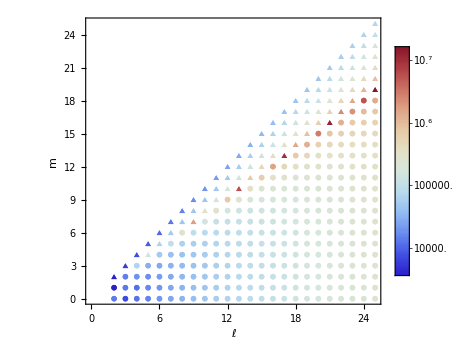

```mathematica
list3Dplotposition=posvalues;
list3Dplot=Abs[posvalues];

lplot=Length[list3Dplot];

tabaux=Table[list3Dplot[[i,3]],{i,lplot}];

tablogaux=Log10[tabaux/Max[tabaux]]-Min[Log10[tabaux/Max[tabaux]]];

tablog=tablogaux/Max[tablogaux];

markerlist=Table[{If[list3Dplotposition[[i,3]]>=0,Graphics[Disk[]],Graphics[t]],1.25/lmax (0tablog[[i]]+0.7)},{i,lplot}];

listcolor=Table[{ColorData["ThermometerColors"][tablog[[i]]],PointSize[1.25/lmax tablog[[i]]]},{i,lplot}];

posvaluesplot=ListPlot[Table[{list3Dplot[[i,{1,2}]]},{i,lplot}],PlotMarkers->markerlist,AspectRatio->0.9,Frame->True,BaseStyle->{FontFamily-> "Times New Roman",FontSize-> 13},ImageSize->400,FrameLabel->{Style["ℓ",25],Style[m,25]}  ,PlotStyle->listcolor,Epilog->Inset[BarLegend[{"ThermometerColors",{Floor[Min[tabaux]],Floor[Max[tabaux]]}},ScalingFunctions->"Log"],{7(lmax/50),33 (lmax/50)}]]
```

plot for (Δ^-)_(l m)

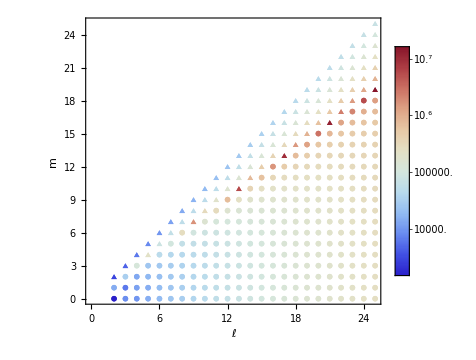

```mathematica
list3Dplotposition=negvalues;
list3Dplot=Abs[negvalues];

lplot=Length[list3Dplot];

tabaux=Table[list3Dplot[[i,3]],{i,lplot}];

tablogaux=Log10[tabaux/Max[tabaux]]-Min[Log10[tabaux/Max[tabaux]]];

tablog=tablogaux/Max[tablogaux];

markerlist=Table[{If[list3Dplotposition[[i,3]]>=0,Graphics[Disk[]],Graphics[t]],1.25/lmax (0tablog[[i]]+0.7)},{i,lplot}];

listcolor=Table[{ColorData["ThermometerColors"][tablog[[i]]],PointSize[1.25/lmax tablog[[i]]]},{i,lplot}];

negvaluesplot=ListPlot[Table[{list3Dplot[[i,{1,2}]]},{i,lplot}],PlotMarkers->markerlist,AspectRatio->0.9,Frame->True,BaseStyle->{FontFamily-> "Times New Roman",FontSize-> 13},ImageSize->400,FrameLabel->{Style["ℓ",25],Style[m,25]},PlotStyle->listcolor,Epilog->Inset[BarLegend[{"ThermometerColors",{Floor[Min[tabaux]],Floor[Max[tabaux]]}},ScalingFunctions->"Log"],{7(lmax/50),33 (lmax/50)}]]
```